```mathematica
ClearAll["Global`*"];
```

# Gravitational wave memory calculation

## Constants

```mathematica
θ = (−11831)/9240;
λ = −1987/3080;
```

## Parameter definitions (Spin variables: Eq. (5.1) of BBF (gr-qc/0605140))

```mathematica
m1= m/2(1+δ);
m2= m/2(1-δ);
Sl =Simplify[ m1^2 (χsdL+χadL) + m2^2 (χsdL-χadL)];
Sl = Simplify[Sl/.δ^2-> (1-4η)];
Σl =Simplify[ m(m2 (χsdL-χadL)-m1 (χsdL+χadL)),Assumptions->{m> 0,η>0} ];
sl = Sl/m^2;
σl = Σl/m^2;
```

## Energy function : Eq. (6.6) of BBF (gr - qc/0605140) and Eq.(C4) of ABFO (0810.5336);

```mathematica
En[0] = 1;
En[1] = 0;
En[2] = -3/4-η/12;
En[3]=(8/3 -4/3 η)χsdL+8/3 δ χadL;
En[4]= -27/8+(19 η)/8-η^2/24+η((χsSqr - χaSqr)-3(χsdL^2-χadL^2))+(1/2-η)(χsSqr + χaSqr-3(χsdL^2+χadL^2))+δ(χsdχa-3(χsdL  χadL));
En[5]=(8 -121/9 η + 2/9 η^2)χsdL + (8 - 31/9 η)δ χadL;
En[6]=-675/64+(34445/576-(205 π^2)/96)η-155/96 η^2-35/5184 η^3;
En[7]= 0;
Energy[n_]:= -(η v^2 M)/2(Collect[Expand[Sum[En[k]*v^k,{k,0,n}]]/.δ^2-> 1-4η,v])
dEnergy[n_]:=(-v η)Collect[Expand[D[Energy[n],v]/(-v η)],{v,η}]
```

```mathematica
Energy[7]/.{v-> √x, χaSqr-> 0, χsSqr-> 0,χsdχa-> 0,χadL-> 0,χsdL-> 0}
```

-1/2 M x η (1+x (-3/4-η/12)+x^2 (-27/8+(19 η)/8-η^2/24)+x^3 (-675/64+(34445 η)/576-(205 π^2 η)/96-(155 η^2)/96-(35 η^3)/5184))

## Flux function : Eq. (6.4) of BBF (gr - qc/0605140) and Eq.(C10) of ABFO (0810.5336);

```mathematica
FN = (32 η^2)/5;
F[0] = 1;
F[1]=0;
F[2]=-1247/336-(35 η)/12;
F[3]=4 π - ((11/4-3 η)χsdL + 11/4 δ χadL);
F[4]=(−44711)/9072+(9271 η)/504+(65 η^2)/18+(287/96+η/24)χsdL^2-(89/96+(7 η)/24)χsSqr+(287/96-12 η)χadL^2+(-89/96+4 η)χaSqr +287/48 δ  χsdL  χadL-89/48 δ  χsdχa;
F[5]=π ((−8191)/672-(583 η)/24) + ((-59/16+227/9 η - 157/9 η^2)χsdL + (-59/16 + 701/36 η)δ χadL);
F[6]=6643739519/69854400+(16 π^2)/3-(1712 γE)/105-856/105 Log[16 x]+((- 134543)/7776 + 41/48 π^2) η-(94403  η^2)/3024- (775 η^3)/324 ;
F[7]=π(-16285/504+ (214745 η)/1728+(193385 η^2)/3024);
Flux[n_] := FN v^10 Collect[Expand[(Sum[F[k] v^k,{k,0,n}])]/.δ^2-> 1-4η,{v,η}]
```

```mathematica
Flux[7]/.{v-> √x, χaSqr-> 0, χsSqr-> 0,χsdχa-> 0,χadL-> 0,χsdL-> 0}
```

32/5 x^5 η^2 (1+4 π x^(3/2)+x (-1247/336-(35 η)/12)+x^(5/2) (-(8191 π)/672-(583 π η)/24)+x^2 (-44711/9072+(9271 η)/504+(65 η^2)/18)+x^(7/2) (-(16285 π)/504+(214745 π η)/1728+(193385 π η^2)/3024)+x^3 (6643739519/69854400+(16 π^2)/3-(1712 γE)/105+(-134543/7776+(41 π^2)/48) η-(94403 η^2)/3024-(775 η^3)/324-856/105 Log[16 x]))

## dx/dt expression from equation 3.19 (https://arxiv.org/pdf/0812.0069.pdf)

```mathematica
FbydE[n_] := Collect[Expand[Normal[Series[(Flux[n]/dEnergy[n]),{v,0,n+9}]]/((-32 η v^9)/(5 M))],{v,χsSqr,χaSqr,χsdL, χadL,χsdχa,δ, η}]((-32 η v^9)/(5 M))
(* Ẋ[n_]:=-2 v FbydE[n]/.{v-> √x, χaSqr-> 0, χsSqr-> 0,χsdχa-> 0,χadL-> 0,χsdL-> 0}*)
Ẋ[n_]:=-2 v FbydE[n]/.{v-> √x,χsdL-> Subscript[χz, s], χadL-> Subscript[χz, a],χsSqr->  Subscript[χz, s]^2,χaSqr->  Subscript[χz, a]^2,χsdχa-> Subscript[χz, s] Subscript[χz, a]}
```

```mathematica
Ẋ[6]
```

1/(5 M)64 x^5 η (1+x (-743/336-(11 η)/4)+x^(3/2) (4 π-(113 δ χz_a)/12+(-113/12+(19 η)/3) χz_s)+x^(5/2) (-(4159 π)/672-(189 π η)/8+δ (-31319/1008+(1159 η)/24) χz_a+(-31319/1008+(22975 η)/252-(79 η^2)/3) χz_s)+x^2 (34103/18144+(13661 η)/2016+(59 η^2)/18+(719/96-30 η) χz_a^2+(-233/96+10 η) χz_a^2+81/8 δ χz_a χz_s+(-233/96-(7 η)/24) χz_s^2+(719/96+η/24) χz_s^2)+x^3 (16447322263/139708800+(16 π^2)/3-(1712 γE)/105+(-56198689/217728+(451 π^2)/48) η+(541 η^2)/896-(5605 η^3)/2592-856/105 Log[16 x]-80/3 π δ χz_a+(-145/448+(21985 η)/4032-(89 η^2)/6) χz_a^2+(575/448+(565 δ^2)/9-(65815 η)/4032+(89 η^2)/2) χz_a^2+δ (-145/224+(2143 η)/288) χz_a χz_s+(-(80 π)/3+(40 π η)/3+δ (258295/2016-(9203 η)/96) χz_a) χz_s+(-145/448+(1891 η)/576-(7 η^2)/144) χz_s^2+(258295/4032-(48773 η)/576+(3041 η^2)/144) χz_s^2))

## ϕ(x) expression from equation B3 (https://arxiv.org/pdf/0812.0069.pdf)

```mathematica
ϕ[0]=1;
ϕ[1]=0;
ϕ[2]=(3715/1008+55/12 η);
ϕ[3]=-10 π + 565/24((1-(76η)/113)χsdL + δ  χadL);
ϕ[4]=(15293365/1016064+ 27145/1008 η + 3085/144 η^2+(-3595/96-(5η)/24)χsdL^2+(1165/96+(35 η)/24)χsSqr+(150 η-3595/96)χadL^2+(1165/96-50 η)χaSqr -3595/48 δ  χsdL  χadL+1165/48 δ  χsdχa);
ϕ[5] =  (Log[x]- (11/18- (2γE)/3 -4/3 Log[2] + 2/3 Log[M/r0]))((38645π)/1344- (65π)/16 η + χadL/2((-35δ η)/2- (732985 δ)/2016 ) +   χsdL/2((85 η^2)/2+ (6065η)/18 - 732985/2016));
ϕ[6]= (12348611926451/18776862720-160/3 π^2 - 856/21(2γE + Log[16x]) + (-15737765635/12192768+ 2255/48 π^2)η+76055/6912 η^2- 127825/5184 η^3);
ϕ[7]=π(77096675/2032128+378515/12096 η- 74045/6048 η^2);
φ[n_]:= -1/(32η x^(5/2))(Collect[Expand[Sum[ϕ[k]*x^(k/2),{k,0,n}]],{x,χsSqr,χaSqr,χsdL, χadL,χsdχa,δ, η}]);
ψ[n_]:=φ[n] - 3 x^(3/2)(1-η/2 x)(Log[x]- (11/18- (2γE)/3 -4/3 Log[2] + 2/3 Log[M/r0]));
```

```mathematica
φ[6]/.{v-> √x, χaSqr-> 0, χsSqr-> 0,χsdχa-> 0,χadL-> 0,χsdL-> 0}
```

-1/(32 x^(5/2) η)(1-10 π x^(3/2)+x (3715/1008+(55 η)/12)+x^2 (15293365/1016064+(27145 η)/1008+(3085 η^2)/144)+x^(5/2) (-(425095 π)/24192+(38645 π γE)/2016+(38645 π Log[2])/1008-(38645 π Log[M/r0])/2016+(38645 π Log[x])/1344+η ((715 π)/288-(65 π γE)/24-65/12 π Log[2]+65/24 π Log[M/r0]-65/16 π Log[x]))+x^3 (12348611926451/18776862720-(160 π^2)/3-(1712 γE)/21+(-15737765635/12192768+(2255 π^2)/48) η+(76055 η^2)/6912-(127825 η^3)/5184-856/21 Log[16 x]))

## h_lm expressions from Blanchet arXiv:0802.1249v2 , Class. Quantum Grav. 25, 165003 (2008)(Spin terms from https://arxiv.org/pdf/0810.5336.pdf)

```mathematica
(*This section contains expression from equation 9.4 in the above mentioned paper. These expressions can be used to contruct Subscript[h, lm] using equation 9.3a. The results for negative H^lm can be obtained by using the relation (Ĥ)^(l,-m)=(-1)^l(Ĥ)^(*lm)*)
Subscript[OverHat[Hp], 22][0] =1;
Subscript[OverHat[Hp], 22][1] = 0;
Subscript[OverHat[Hp], 22][2] = (-107/42+ (55η)/42);
Subscript[OverHat[Hp], 22][3]=  (2 π- (4δ Subscript[χz, a])/3 + 4/3(-1 +η )Subscript[χz, s]);
Subscript[OverHat[Hp], 22][4]=(-2173/1512- (1069η)/216 + (2047 η^2)/1512);
Subscript[OverHat[Hp], 22][5]=(-(107π)/21-24I η + (34π η)/21);
Subscript[OverHat[Hp], 22][6] = (27027409/646800-(856γE)/105+ (428I π)/105+(2 π^2)/3+(-278185/33264+(41 π^2)/96)η -(20261 η^2)/2772 + (114635 η^3)/99792-428/105 Log[16x]);
Subscript[Ĥ, 22][n_]:= (Collect[Expand[Sum[Subscript[OverHat[Hp], 22][k]*x^(k/2),{k,0,n}]],x]);

Subscript[OverHat[Hp], C22][0] =1;
Subscript[OverHat[Hp], C22][1] = 0;
Subscript[OverHat[Hp], C22][2] = (-107/42+ (55η)/42);
Subscript[OverHat[Hp], C22][3]=  (2 π- (4δ Subscript[χz, a])/3 + 4/3(-1 +η )Subscript[χz, s]);
Subscript[OverHat[Hp], C22][4]=(-2173/1512- (1069η)/216 + (2047 η^2)/1512);
Subscript[OverHat[Hp], C22][5]=(-(107π)/21+24I η + (34π η)/21);
Subscript[OverHat[Hp], C22][6] = (27027409/646800-(856γE)/105- (428I π)/105+(2 π^2)/3+(-278185/33264+(41 π^2)/96)η -(20261 η^2)/2772 + (114635 η^3)/99792-428/105 Log[16x]);
Subscript[Ĥ, C22][n_]:= (Collect[Expand[Sum[Subscript[OverHat[Hp], C22][k]*x^(k/2),{k,0,n}]],x]);

Subscript[OverHat[HNp], 21] =I δ/3 ;
Subscript[OverHat[Hp], 21][0]= 0;
Subscript[OverHat[Hp], 21][1]= 1;
Subscript[OverHat[Hp], 21][2]= -3/2(Subscript[χz, a] + δ Subscript[χz, s]);
Subscript[OverHat[Hp], 21][3]= (-17/28+ 5/7 η);
Subscript[OverHat[Hp], 21][4]= π+ I(-1/2-2 Log[2]);
Subscript[OverHat[Hp], 21][5]= (-43/126- 509/126 η + 79/168 η^2);
Subscript[OverHat[Hp], 21][6]= (-(17π)/28 + (3π η)/14 + I(17/56 + η(-995/84- (3 Log[2])/7) + (17 Log[2])/14));
Subscript[Ĥ, 21][n_]:= Subscript[OverHat[HNp], 21](Collect[Expand[Sum[Subscript[OverHat[Hp], 21][k]*x^(k/2),{k,0,n}]],x]);

Subscript[OverHat[HNp], C21] =-I δ/3 ;
Subscript[OverHat[Hp], C21][0]= 0;
Subscript[OverHat[Hp], C21][1]= 1;
Subscript[OverHat[Hp], C21][2]= -3/2(Subscript[χz, a] + δ Subscript[χz, s]);
Subscript[OverHat[Hp], C21][3]= (-17/28+ 5/7 η);
Subscript[OverHat[Hp], C21][4]= π- I(-1/2-2 Log[2]);
Subscript[OverHat[Hp], C21][5]= (-43/126- 509/126 η + 79/168 η^2);
Subscript[OverHat[Hp], C21][6]= (-(17π)/28 + (3π η)/14 - I(17/56 + η(-995/84- (3 Log[2])/7) + (17 Log[2])/14));
Subscript[Ĥ, C21][n_]:= Subscript[OverHat[HNp], C21](Collect[Expand[Sum[Subscript[OverHat[Hp], C21][k]*x^(k/2),{k,0,n}]],x]);


Subscript[OverHat[HNp], 20] =  -5/(14 √6);
Subscript[OverHat[Hp], 20][0]= 1;
Subscript[OverHat[Hp], 20][1]= 0;
Subscript[OverHat[Hp], 20][2]= 0;
Subscript[OverHat[Hp], 20][3]= 0;
Subscript[OverHat[Hp], 20][4]= 0;
Subscript[OverHat[Hp], 20][5]= 0;
Subscript[OverHat[Hp], 20][6]= 0;
Subscript[Ĥ, 20][n_]:= Subscript[OverHat[HNp], 20](Collect[Expand[Sum[Subscript[OverHat[Hp], 20][k]*x^(k/2),{k,0,n}]],x]);

Subscript[OverHat[HNp], C20] =  -5/(14 √6);
Subscript[OverHat[Hp], C20][0]= 1;
Subscript[OverHat[Hp], C20][1]= 0;
Subscript[OverHat[Hp], C20][2]= 0;
Subscript[OverHat[Hp], C20][3]= 0;
Subscript[OverHat[Hp], C20][4]= 0;
Subscript[OverHat[Hp], C20][5]= 0;
Subscript[OverHat[Hp], C20][6]= 0;
Subscript[Ĥ, C20][n_]:= Subscript[OverHat[HNp], C20](Collect[Expand[Sum[Subscript[OverHat[Hp], C20][k]*x^(k/2),{k,0,n}]],x]);

Subscript[OverHat[HNp], 33] = -3/4 I √(15/14)δ;
Subscript[OverHat[Hp], 33][0]= 0;
Subscript[OverHat[Hp], 33][1]= 1;
Subscript[OverHat[Hp], 33][2]= 0;
Subscript[OverHat[Hp], 33][3]= (-4 + 2 η);
Subscript[OverHat[Hp], 33][4]= (3 π + I(-21/5 + 6 Log[3/2]));
Subscript[OverHat[Hp], 33][5]= (123/110- (1838η)/165+ (887 η^2)/330);
Subscript[OverHat[Hp], 33][6]= (-12 π + (9 π η)/2 + I(84/5-24 Log[3/2] + η(-48103/1215+ 9 Log[3/2])));
Subscript[Ĥ, 33][n_]:= Subscript[OverHat[HNp], 33](Collect[Expand[Sum[Subscript[OverHat[Hp], 33][k]*x^(k/2),{k,0,n}]],x]);

Subscript[OverHat[HNp], C33] = 3/4 I √(15/14)δ;
Subscript[OverHat[Hp], C33][0]= 0;
Subscript[OverHat[Hp], C33][1]= 1;
Subscript[OverHat[Hp], C33][2]= 0;
Subscript[OverHat[Hp], C33][3]= (-4 + 2 η);
Subscript[OverHat[Hp], C33][4]= (3 π - I(-21/5 + 6 Log[3/2]));
Subscript[OverHat[Hp], C33][5]= (123/110- (1838η)/165+ (887 η^2)/330);
Subscript[OverHat[Hp], C33][6]= (-12 π + (9 π η)/2 - I(84/5-24 Log[3/2] + η(-48103/1215+ 9 Log[3/2])));
Subscript[Ĥ, C33][n_]:= Subscript[OverHat[HNp], C33](Collect[Expand[Sum[Subscript[OverHat[Hp], C33][k]*x^(k/2),{k,0,n}]],x]);

Subscript[OverHat[HNp], 32] = 1/3 √(5/7);
Subscript[OverHat[Hp], 32][0]= 0;
Subscript[OverHat[Hp], 32][1]= 0;
Subscript[OverHat[Hp], 32][2]= (1 - 3 η);
Subscript[OverHat[Hp], 32][3]= 4 η Subscript[χz, s];
Subscript[OverHat[Hp], 32][4]= (-193/90+ (145η)/18- (73 η^2)/18);
Subscript[OverHat[Hp], 32][5]= (2 π - 6 π η + I (-3 + (66η)/5));
Subscript[OverHat[Hp], 32][6]= (-1451/3960-(17387η)/3960+ (5557 η^2)/220- (5341 η^3)/1320);
Subscript[Ĥ, 32][n_]:= Subscript[OverHat[HNp], 32](Collect[Expand[Sum[Subscript[OverHat[Hp], 32][k]*x^(k/2),{k,0,n}]],x]);

Subscript[OverHat[HNp], C32] = 1/3 √(5/7);
Subscript[OverHat[Hp], C32][0]= 0;
Subscript[OverHat[Hp], C32][1]= 0;
Subscript[OverHat[Hp], C32][2]= (1 - 3 η);
Subscript[OverHat[Hp], C32][3]= 4 η Subscript[χz, s];
Subscript[OverHat[Hp], C32][4]= (-193/90+ (145η)/18- (73 η^2)/18);
Subscript[OverHat[Hp], C32][5]= (2 π - 6 π η - I (-3 + (66η)/5));
Subscript[OverHat[Hp], C32][6]= (-1451/3960-(17387η)/3960+ (5557 η^2)/220- (5341 η^3)/1320);
Subscript[Ĥ, C32][n_]:= Subscript[OverHat[HNp], C32](Collect[Expand[Sum[Subscript[OverHat[Hp], C32][k]*x^(k/2),{k,0,n}]],x]);


Subscript[OverHat[HNp], 31] = I δ/(12 √14);
Subscript[OverHat[Hp], 31][0]= 0;
Subscript[OverHat[Hp], 31][1]= 1;
Subscript[OverHat[Hp], 31][2]= 0;
Subscript[OverHat[Hp], 31][3]= (-8/3 - 2/3 η);
Subscript[OverHat[Hp], 31][4]= ( π + I(-7/5 - 2 Log[2]));
Subscript[OverHat[Hp], 31][5]= (607/198- (136η)/99- (247 η^2)/198);
Subscript[OverHat[Hp], 31][6]= ((-8π)/3- (7 π η)/6 + I(56/15+(16 Log[2])/3+ η(-1/15+ (7 Log[2])/3)));
Subscript[Ĥ, 31][n_]:= Subscript[OverHat[HNp], 31](Collect[Expand[Sum[Subscript[OverHat[Hp], 31][k]*x^(k/2),{k,0,n}]],x]);

Subscript[OverHat[HNp], C31] =- I δ/(12 √14);
Subscript[OverHat[Hp], C31][0]= 0;
Subscript[OverHat[Hp], C31][1]= 1;
Subscript[OverHat[Hp], C31][2]= 0;
Subscript[OverHat[Hp], C31][3]= (-8/3 - 2/3 η);
Subscript[OverHat[Hp], C31][4]= ( π - I(-7/5 - 2 Log[2]));
Subscript[OverHat[Hp], C31][5]= (607/198- (136η)/99- (247 η^2)/198);
Subscript[OverHat[Hp], C31][6]= ((-8π)/3- (7 π η)/6 - I(56/15+(16 Log[2])/3+ η(-1/15+ (7 Log[2])/3)));
Subscript[Ĥ, C31][n_]:= Subscript[OverHat[HNp], C31](Collect[Expand[Sum[Subscript[OverHat[Hp], C31][k]*x^(k/2),{k,0,n}]],x]);


Subscript[OverHat[HNp], 30] = -2/5 I √(6/7)η;
Subscript[OverHat[Hp], 30][0]= 0;
Subscript[OverHat[Hp], 30][1]= 0;
Subscript[OverHat[Hp], 30][2]= 0;
Subscript[OverHat[Hp], 30][3]= 0;
Subscript[OverHat[Hp], 30][4]= 0;
Subscript[OverHat[Hp], 30][5]= 1;
Subscript[OverHat[Hp], 30][6]= 0;
Subscript[Ĥ, 30][n_]:= Subscript[OverHat[HNp], 30](Collect[Expand[Sum[Subscript[OverHat[Hp], 30][k]*x^(k/2),{k,0,n}]],x]);

Subscript[OverHat[HNp], C30] = 2/5 I √(6/7)η;
Subscript[OverHat[Hp], C30][0]= 0;
Subscript[OverHat[Hp], C30][1]= 0;
Subscript[OverHat[Hp], C30][2]= 0;
Subscript[OverHat[Hp], C30][3]= 0;
Subscript[OverHat[Hp], C30][4]= 0;
Subscript[OverHat[Hp], C30][5]= 1;
Subscript[OverHat[Hp], C30][6]= 0;
Subscript[Ĥ, C30][n_]:= Subscript[OverHat[HNp], C30](Collect[Expand[Sum[Subscript[OverHat[Hp], C30][k]*x^(k/2),{k,0,n}]],x]);


Subscript[OverHat[HNp], 44] = -8/9 √(5/7);
Subscript[OverHat[Hp], 44][0]= 0;
Subscript[OverHat[Hp], 44][1]= 0;
Subscript[OverHat[Hp], 44][2]= (1-3 η);
Subscript[OverHat[Hp], 44][3]= 0;
Subscript[OverHat[Hp], 44][4]= (-593/110 + 1273/66 η -  175/22 η^2);
Subscript[OverHat[Hp], 44][5]= (4 π -12 π η  + I (-42/5 + η (1193/40- 24 Log[2]) + 8 Log[2]));
Subscript[OverHat[Hp], 44][6]= (1068671/200200- 1088119/28600 η + 146879/2340 η^2 - 226097/17160 η^3);
Subscript[Ĥ, 44][n_]:= Subscript[OverHat[HNp], 44](Collect[Expand[Sum[Subscript[OverHat[Hp], 44][k]*x^(k/2),{k,0,n}]],x]);

Subscript[OverHat[HNp], C44] = -8/9 √(5/7);
Subscript[OverHat[Hp], C44][0]= 0;
Subscript[OverHat[Hp], C44][1]= 0;
Subscript[OverHat[Hp], C44][2]= (1-3 η);
Subscript[OverHat[Hp], C44][3]= 0;
Subscript[OverHat[Hp], C44][4]= (-593/110 + 1273/66 η -  175/22 η^2);
Subscript[OverHat[Hp], C44][5]= (4 π -12 π η  - I (-42/5 + η (1193/40- 24 Log[2]) + 8 Log[2]));
Subscript[OverHat[Hp], C44][6]= (1068671/200200- 1088119/28600 η + 146879/2340 η^2 - 226097/17160 η^3);
Subscript[Ĥ, C44][n_]:= Subscript[OverHat[HNp], C44](Collect[Expand[Sum[Subscript[OverHat[Hp], C44][k]*x^(k/2),{k,0,n}]],x]);

Subscript[OverHat[HNp], 43] =  -(9 I δ)/(4 √70);
Subscript[OverHat[Hp], 43][0]= 0;
Subscript[OverHat[Hp], 43][1]= 0;
Subscript[OverHat[Hp], 43][2]= 0;
Subscript[OverHat[Hp], 43][3]= (1-2 η);
Subscript[OverHat[Hp], 43][4]= 0;
Subscript[OverHat[Hp], 43][5]= (-39/11 + 1267/132 η - 131/33 η^2);
Subscript[OverHat[Hp], 43][6]= (3π -6 π η  + I (-32/5 + η (16301/810- 12 Log[3/2]) + 6 Log[3/2]));
Subscript[Ĥ, 43][n_]:= Subscript[OverHat[HNp], 43](Collect[Expand[Sum[Subscript[OverHat[Hp], 43][k]*x^(k/2),{k,0,n}]],x]);

Subscript[OverHat[HNp], C43] =  (9 I δ)/(4 √70);
Subscript[OverHat[Hp], C43][0]= 0;
Subscript[OverHat[Hp], C43][1]= 0;
Subscript[OverHat[Hp], C43][2]= 0;
Subscript[OverHat[Hp], C43][3]= (1-2 η);
Subscript[OverHat[Hp], C43][4]= 0;
Subscript[OverHat[Hp], C43][5]= (-39/11 + 1267/132 η - 131/33 η^2);
Subscript[OverHat[Hp], C43][6]= (3π -6 π η  - I (-32/5 + η (16301/810- 12 Log[3/2]) + 6 Log[3/2]));
Subscript[Ĥ, C43][n_]:= Subscript[OverHat[HNp], C43](Collect[Expand[Sum[Subscript[OverHat[Hp], C43][k]*x^(k/2),{k,0,n}]],x]);

Subscript[OverHat[HNp], 42] =  (√5)/63;
Subscript[OverHat[Hp], 42][0]= 0;
Subscript[OverHat[Hp], 42][1]= 0;
Subscript[OverHat[Hp], 42][2]= (1-3 η);
Subscript[OverHat[Hp], 42][3]= 0;
Subscript[OverHat[Hp], 42][4]= (-437/110 + 805/66 η - 19/22 η^2);
Subscript[OverHat[Hp], 42][5]= (2 π - 6 π η + I (-21/5 + 84/5 η));
Subscript[OverHat[Hp], 42][6]= (1038039/200200 - 606751/28600 η + 400453/25740 η^2 + 25783/17160 η^3);
Subscript[Ĥ, 42][n_]:= Subscript[OverHat[HNp], 42](Collect[Expand[Sum[Subscript[OverHat[Hp], 42][k]*x^(k/2),{k,0,n}]],x]);

Subscript[OverHat[HNp], C42] =  (√5)/63;
Subscript[OverHat[Hp], C42][0]= 0;
Subscript[OverHat[Hp], C42][1]= 0;
Subscript[OverHat[Hp], C42][2]= (1-3 η);
Subscript[OverHat[Hp], C42][3]= 0;
Subscript[OverHat[Hp], C42][4]=(-437/110 + 805/66 η - 19/22 η^2);
Subscript[OverHat[Hp], C42][5]= (2 π - 6 π η - I (-21/5 + 84/5 η));
Subscript[OverHat[Hp], C42][6]= (1038039/200200 - 606751/28600 η + 400453/25740 η^2 + 25783/17160 η^3);
Subscript[Ĥ, C42][n_]:= Subscript[OverHat[HNp], C42](Collect[Expand[Sum[Subscript[OverHat[Hp], C42][k]*x^(k/2),{k,0,n}]],x]);


Subscript[OverHat[HNp], 41] =  (I δ)/(84 √10);
Subscript[OverHat[Hp], 41][0]= 0;
Subscript[OverHat[Hp], 41][1]= 0;
Subscript[OverHat[Hp], 41][2]= 0;
Subscript[OverHat[Hp], 41][3]=(1-2 η);
Subscript[OverHat[Hp], 41][4]= 0;
Subscript[OverHat[Hp], 41][5]= (-101/33+ 337/44 η - 83/33 η^2);
Subscript[OverHat[Hp], 41][6]= (π - 2 π η + I (-32/15 - 2 Log[2] + η (1661/30 + 4 Log[2])));
Subscript[Ĥ, 41][n_]:= Subscript[OverHat[HNp], 41](Collect[Expand[Sum[Subscript[OverHat[Hp], 41][k]*x^(k/2),{k,0,n}]],x]);

Subscript[OverHat[HNp], C41] =  -(I δ)/(84 √10);
Subscript[OverHat[Hp], C41][0]= 0;
Subscript[OverHat[Hp], C41][1]= 0;
Subscript[OverHat[Hp], C41][2]= 0;
Subscript[OverHat[Hp], C41][3]=(1-2 η);
Subscript[OverHat[Hp], C41][4]= 0;
Subscript[OverHat[Hp], C41][5]= (-101/33+ 337/44 η - 83/33 η^2);
Subscript[OverHat[Hp], C41][6]= (π - 2 π η - I (-32/15 - 2 Log[2] + η (1661/30 + 4 Log[2])));
Subscript[Ĥ, C41][n_]:= Subscript[OverHat[HNp], C41](Collect[Expand[Sum[Subscript[OverHat[Hp], C41][k]*x^(k/2),{k,0,n}]],x]);


Subscript[OverHat[HNp], 40] =  -1/(504 √2);
Subscript[OverHat[Hp], 40][0]= 1;
Subscript[OverHat[Hp], 40][1]= 0;
Subscript[OverHat[Hp], 40][2]= 0;
Subscript[OverHat[Hp], 40][3]=0;
Subscript[OverHat[Hp], 40][4]= 0;
Subscript[OverHat[Hp], 40][5]= 0;
Subscript[OverHat[Hp], 40][6]= 0;
Subscript[Ĥ, 40][n_]:= Subscript[OverHat[HNp], 40](Collect[Expand[Sum[Subscript[OverHat[Hp], 40][k]*x^(k/2),{k,0,n}]],x]);

Subscript[OverHat[HNp], C40] =  -1/(504 √2);
Subscript[OverHat[Hp], C40][0]= 1;
Subscript[OverHat[Hp], C40][1]= 0;
Subscript[OverHat[Hp], C40][2]= 0;
Subscript[OverHat[Hp], C40][3]=0;
Subscript[OverHat[Hp], C40][4]= 0;
Subscript[OverHat[Hp], C40][5]= 0;
Subscript[OverHat[Hp], C40][6]= 0;
Subscript[Ĥ, C40][n_]:= Subscript[OverHat[HNp], C40](Collect[Expand[Sum[Subscript[OverHat[Hp], C40][k]*x^(k/2),{k,0,n}]],x]);

Subscript[OverHat[HNp], 55] =  (625 I δ)/(96 √66);
Subscript[OverHat[Hp], 55][0]= 0;
Subscript[OverHat[Hp], 55][1]= 0;
Subscript[OverHat[Hp], 55][2]= 0;
Subscript[OverHat[Hp], 55][3]=(1-2 η);
Subscript[OverHat[Hp], 55][4]= 0;
Subscript[OverHat[Hp], 55][5]= (-263/39 + 688/39 η - 256/39 η^2);
Subscript[OverHat[Hp], 55][6]= (5 π - 10 π η + I(-181/14 + η (105834/3125 - 20 Log[5/2]) + 10 Log[5/2]));
Subscript[Ĥ, 55][n_]:= Subscript[OverHat[HNp], 55](Collect[Expand[Sum[Subscript[OverHat[Hp], 55][k]*x^(k/2),{k,0,n}]],x]);

Subscript[OverHat[HNp], C55] =  -(625 I δ)/(96 √66);
Subscript[OverHat[Hp], C55][0]= 0;
Subscript[OverHat[Hp], C55][1]= 0;
Subscript[OverHat[Hp], C55][2]= 0;
Subscript[OverHat[Hp], C55][3]=(1-2 η);
Subscript[OverHat[Hp], C55][4]= 0;
Subscript[OverHat[Hp], C55][5]= (-263/39 + 688/39 η - 256/39 η^2);
Subscript[OverHat[Hp], C55][6]= (5 π - 10 π η - I(-181/14 + η (105834/3125 - 20 Log[5/2]) + 10 Log[5/2]));
Subscript[Ĥ, C55][n_]:= Subscript[OverHat[HNp], C55](Collect[Expand[Sum[Subscript[OverHat[Hp], C55][k]*x^(k/2),{k,0,n}]],x]);

Subscript[OverHat[HNp], 54] = - 32/(9 √165);
Subscript[OverHat[Hp], 54][0]= 0;
Subscript[OverHat[Hp], 54][1]= 0;
Subscript[OverHat[Hp], 54][2]= 0;
Subscript[OverHat[Hp], 54][3]= 0;
Subscript[OverHat[Hp], 54][4]= (1- 5 η + 5 η^2);
Subscript[OverHat[Hp], 54][5]=0;
Subscript[OverHat[Hp], 54][6]=  (-4451/910 + 3619/130 η - 521/13 η^2 + 339/26 η^3);
Subscript[Ĥ, 54][n_]:= Subscript[OverHat[HNp], 54](Collect[Expand[Sum[Subscript[OverHat[Hp], 54][k]*x^(k/2),{k,0,n}]],x]);

Subscript[OverHat[HNp], C54] = - 32/(9 √165);
Subscript[OverHat[Hp], C54][0]= 0;
Subscript[OverHat[Hp], C54][1]= 0;
Subscript[OverHat[Hp], C54][2]= 0;
Subscript[OverHat[Hp], C54][3]= 0;
Subscript[OverHat[Hp], C54][4]= (1- 5 η + 5 η^2);
Subscript[OverHat[Hp], C54][5]=0;
Subscript[OverHat[Hp], C54][6]=  (-4451/910 + 3619/130 η - 521/13 η^2 + 339/26 η^3);
Subscript[Ĥ, C54][n_]:= Subscript[OverHat[HNp], C54](Collect[Expand[Sum[Subscript[OverHat[Hp], C54][k]*x^(k/2),{k,0,n}]],x]);

Subscript[OverHat[HNp], 53] = -9/32 I √(3/110) δ;
Subscript[OverHat[Hp], 53][0]= 0;
Subscript[OverHat[Hp], 53][1]= 0;
Subscript[OverHat[Hp], 53][2]= 0;
Subscript[OverHat[Hp], 53][3]= (1-2 η);
Subscript[OverHat[Hp], 53][4]= 0;
Subscript[OverHat[Hp], 53][5]=(-69/13+ 464/39 η - 88/39 η^2);
Subscript[OverHat[Hp], 53][6]=  (3 π - 6 π η + I (-543/70 + η (83702/3645- 12 Log[3/2])+ 6 Log[3/2]));
Subscript[Ĥ, 53][n_]:= Subscript[OverHat[HNp], 53](Collect[Expand[Sum[Subscript[OverHat[Hp], 53][k]*x^(k/2),{k,0,n}]],x]);

Subscript[OverHat[HNp], C53] = 9/32 I √(3/110) δ;
Subscript[OverHat[Hp], C53][0]= 0;
Subscript[OverHat[Hp], C53][1]= 0;
Subscript[OverHat[Hp], C53][2]= 0;
Subscript[OverHat[Hp], C53][3]= (1-2 η);
Subscript[OverHat[Hp], C53][4]= 0;
Subscript[OverHat[Hp], C53][5]=(-69/13+ 464/39 η - 88/39 η^2);
Subscript[OverHat[Hp], C53][6]=  (3 π - 6 π η - I (-543/70 + η (83702/3645- 12 Log[3/2])+ 6 Log[3/2]));
Subscript[Ĥ, C53][n_]:= Subscript[OverHat[HNp], C53](Collect[Expand[Sum[Subscript[OverHat[Hp], C53][k]*x^(k/2),{k,0,n}]],x]);


Subscript[OverHat[HNp], 52] = 2/(27 √55) ;
Subscript[OverHat[Hp], 52][0]= 0;
Subscript[OverHat[Hp], 52][1]= 0;
Subscript[OverHat[Hp], 52][2]= 0;
Subscript[OverHat[Hp], 52][3]= 0;
Subscript[OverHat[Hp], 52][4]= (1- 5 η + 5 η^2);
Subscript[OverHat[Hp], 52][5]=0;
Subscript[OverHat[Hp], 52][6]=  (-3911/910 + 3079/130 η - 413/13 η^2 + 231/26 η^3);
Subscript[Ĥ, 52][n_]:= Subscript[OverHat[HNp], 52](Collect[Expand[Sum[Subscript[OverHat[Hp], 52][k]*x^(k/2),{k,0,n}]],x]);

Subscript[OverHat[HNp], C52] = 2/(27 √55) ;
Subscript[OverHat[Hp], C52][0]= 0;
Subscript[OverHat[Hp], C52][1]= 0;
Subscript[OverHat[Hp], C52][2]= 0;
Subscript[OverHat[Hp], C52][3]= 0;
Subscript[OverHat[Hp], C52][4]= (1- 5 η + 5 η^2);
Subscript[OverHat[Hp], C52][5]=0;
Subscript[OverHat[Hp], C52][6]=  (-3911/910 + 3079/130 η - 413/13 η^2 + 231/26 η^3);
Subscript[Ĥ, C52][n_]:= Subscript[OverHat[HNp], C52](Collect[Expand[Sum[Subscript[OverHat[Hp], C52][k]*x^(k/2),{k,0,n}]],x]);

Subscript[OverHat[HNp], 51] =(I δ)/(288 √385) ;
Subscript[OverHat[Hp], 51][0]= 0;
Subscript[OverHat[Hp], 51][1]= 0;
Subscript[OverHat[Hp], 51][2]= 0;
Subscript[OverHat[Hp], 51][3]= (1- 2 η);
Subscript[OverHat[Hp], 51][4]= 0;
Subscript[OverHat[Hp], 51][5]=(-179/39 + 352/39 η - 4/39 η^2);
Subscript[OverHat[Hp], 51][6]=  (π - 2 π η + I (-181/70 - 2 Log[2] + η (626/5 + 4 Log[2])));
Subscript[Ĥ, 51][n_]:= Subscript[OverHat[HNp], 51](Collect[Expand[Sum[Subscript[OverHat[Hp], 51][k]*x^(k/2),{k,0,n}]],x]);

Subscript[OverHat[HNp], C51] =-(I δ)/(288 √385) ;
Subscript[OverHat[Hp], C51][0]= 0;
Subscript[OverHat[Hp], C51][1]= 0;
Subscript[OverHat[Hp], C51][2]= 0;
Subscript[OverHat[Hp], C51][3]= (1- 2 η);
Subscript[OverHat[Hp], C51][4]= 0;
Subscript[OverHat[Hp], C51][5]=(-179/39 + 352/39 η - 4/39 η^2);
Subscript[OverHat[Hp], C51][6]=  (π - 2 π η - I (-181/70 - 2 Log[2] + η (626/5 + 4 Log[2])));
Subscript[Ĥ, C51][n_]:= Subscript[OverHat[HNp], C51](Collect[Expand[Sum[Subscript[OverHat[Hp], C51][k]*x^(k/2),{k,0,n}]],x]);

Subscript[OverHat[HNp], 50] =0 ;
Subscript[OverHat[Hp], 50][0]= 0;
Subscript[OverHat[Hp], 50][1]= 0;
Subscript[OverHat[Hp], 50][2]= 0;
Subscript[OverHat[Hp], 50][3]= 0;
Subscript[OverHat[Hp], 50][4]= 0;
Subscript[OverHat[Hp], 50][5]=0;
Subscript[OverHat[Hp], 50][6]= 0;
Subscript[Ĥ, 50][n_]:= Subscript[OverHat[HNp], 50](Collect[Expand[Sum[Subscript[OverHat[Hp], 50][k]*x^(k/2),{k,0,n}]],x]);

Subscript[OverHat[HNp], C50] =0 ;
Subscript[OverHat[Hp], C50][0]= 0;
Subscript[OverHat[Hp], C50][1]= 0;
Subscript[OverHat[Hp], C50][2]= 0;
Subscript[OverHat[Hp], C50][3]= 0;
Subscript[OverHat[Hp], C50][4]= 0;
Subscript[OverHat[Hp], C50][5]=0;
Subscript[OverHat[Hp], C50][6]= 0;
Subscript[Ĥ, C50][n_]:= Subscript[OverHat[HNp], C50](Collect[Expand[Sum[Subscript[OverHat[Hp], C50][k]*x^(k/2),{k,0,n}]],x]);

Subscript[OverHat[HNp], 66] =54/(5 √143);
Subscript[OverHat[Hp], 66][0]= 0;
Subscript[OverHat[Hp], 66][1]= 0;
Subscript[OverHat[Hp], 66][2]= 0;
Subscript[OverHat[Hp], 66][3]= 0;
Subscript[OverHat[Hp], 66][4]=(1- 5 η + 5 η^2);
Subscript[OverHat[Hp], 66][5]=0;
Subscript[OverHat[Hp], 66][6]= (-113/14 + 91/2 η - 64 η^2 + 39/2 η^3);
Subscript[Ĥ, 66][n_]:= Subscript[OverHat[HNp], 66](Collect[Expand[Sum[Subscript[OverHat[Hp], 66][k]*x^(k/2),{k,0,n}]],x]);

Subscript[OverHat[HNp], C66] =54/(5 √143);
Subscript[OverHat[Hp], C66][0]= 0;
Subscript[OverHat[Hp], C66][1]= 0;
Subscript[OverHat[Hp], C66][2]= 0;
Subscript[OverHat[Hp], C66][3]= 0;
Subscript[OverHat[Hp], C66][4]=(1- 5 η + 5 η^2);
Subscript[OverHat[Hp], C66][5]=0;
Subscript[OverHat[Hp], C66][6]= (-113/14 + 91/2 η - 64 η^2 + 39/2 η^3);
Subscript[Ĥ, C66][n_]:= Subscript[OverHat[HNp], C66](Collect[Expand[Sum[Subscript[OverHat[Hp], C66][k]*x^(k/2),{k,0,n}]],x]);


Subscript[OverHat[HNp], 65] =(3125 I δ)/(504 √429);
Subscript[OverHat[Hp], 65][0]= 0;
Subscript[OverHat[Hp], 65][1]= 0;
Subscript[OverHat[Hp], 65][2]= 0;
Subscript[OverHat[Hp], 65][3]= 0;
Subscript[OverHat[Hp], 65][4]=0;
Subscript[OverHat[Hp], 65][5]=(1- 4η + 3 η^2);
Subscript[OverHat[Hp], 65][6]=0;
Subscript[Ĥ, 65][n_]:= Subscript[OverHat[HNp], 65](Collect[Expand[Sum[Subscript[OverHat[Hp], 65][k]*x^(k/2),{k,0,n}]],x]);


Subscript[OverHat[HNp], C65] =-(3125 I δ)/(504 √429);
Subscript[OverHat[Hp], C65][0]= 0;
Subscript[OverHat[Hp], C65][1]= 0;
Subscript[OverHat[Hp], C65][2]= 0;
Subscript[OverHat[Hp], C65][3]= 0;
Subscript[OverHat[Hp], C65][4]=0;
Subscript[OverHat[Hp], C65][5]=(1- 4η + 3 η^2);
Subscript[OverHat[Hp], C65][6]=0;
Subscript[Ĥ, C65][n_]:= Subscript[OverHat[HNp], C65](Collect[Expand[Sum[Subscript[OverHat[Hp], C65][k]*x^(k/2),{k,0,n}]],x]);

Subscript[OverHat[HNp], 64] =-128/495 √(2/39);
Subscript[OverHat[Hp], 64][0]= 0;
Subscript[OverHat[Hp], 64][1]= 0;
Subscript[OverHat[Hp], 64][2]= 0;
Subscript[OverHat[Hp], 64][3]= 0;
Subscript[OverHat[Hp], 64][4]=(1- 5 η + 5 η^2);
Subscript[OverHat[Hp], 64][5]=0;
Subscript[OverHat[Hp], 64][6]=(-93/14 + (71η)/2- 44 η^2+ 19/2 η^3);
Subscript[Ĥ, 64][n_]:= Subscript[OverHat[HNp], 64](Collect[Expand[Sum[Subscript[OverHat[Hp], 64][k]*x^(k/2),{k,0,n}]],x]);

Subscript[OverHat[HNp], C64] =-128/495 √(2/39);
Subscript[OverHat[Hp], C64][0]= 0;
Subscript[OverHat[Hp], C64][1]= 0;
Subscript[OverHat[Hp], C64][2]= 0;
Subscript[OverHat[Hp], C64][3]= 0;
Subscript[OverHat[Hp], C64][4]=(1- 5 η + 5 η^2);
Subscript[OverHat[Hp], C64][5]=0;
Subscript[OverHat[Hp], C64][6]=(-93/14 + (71η)/2- 44 η^2+ 19/2 η^3);
Subscript[Ĥ, C64][n_]:= Subscript[OverHat[HNp], C64](Collect[Expand[Sum[Subscript[OverHat[Hp], C64][k]*x^(k/2),{k,0,n}]],x]);

Subscript[OverHat[HNp], 63] =-(81 I δ)/(616 √65);
Subscript[OverHat[Hp], 63][0]= 0;
Subscript[OverHat[Hp], 63][1]= 0;
Subscript[OverHat[Hp], 63][2]= 0;
Subscript[OverHat[Hp], 63][3]= 0;
Subscript[OverHat[Hp], 63][4]=0;
Subscript[OverHat[Hp], 63][5]=(1- 4η + 3 η^2);
Subscript[OverHat[Hp], 63][6]=0;
Subscript[Ĥ, 63][n_]:= Subscript[OverHat[HNp], 63](Collect[Expand[Sum[Subscript[OverHat[Hp], 63][k]*x^(k/2),{k,0,n}]],x]);

Subscript[OverHat[HNp], C63] =(81 I δ)/(616 √65);
Subscript[OverHat[Hp], C63][0]= 0;
Subscript[OverHat[Hp], C63][1]= 0;
Subscript[OverHat[Hp], C63][2]= 0;
Subscript[OverHat[Hp], C63][3]= 0;
Subscript[OverHat[Hp], C63][4]=0;
Subscript[OverHat[Hp], C63][5]=(1- 4η + 3 η^2);
Subscript[OverHat[Hp], C63][6]=0;
Subscript[Ĥ, C63][n_]:= Subscript[OverHat[HNp], C63](Collect[Expand[Sum[Subscript[OverHat[Hp], C63][k]*x^(k/2),{k,0,n}]],x]);

Subscript[OverHat[HNp], 62] =2/(297 √65);
Subscript[OverHat[Hp], 62][0]= 0;
Subscript[OverHat[Hp], 62][1]= 0;
Subscript[OverHat[Hp], 62][2]= 0;
Subscript[OverHat[Hp], 62][3]= 0;
Subscript[OverHat[Hp], 62][4]=(1- 5 η + 5 η^2);
Subscript[OverHat[Hp], 62][5]=0;
Subscript[OverHat[Hp], 62][6]=(-81/14 + 59/2 η - 32 η^2 + 7/2 η^3);
Subscript[Ĥ, 62][n_]:= Subscript[OverHat[HNp], 62](Collect[Expand[Sum[Subscript[OverHat[Hp], 62][k]*x^(k/2),{k,0,n}]],x]);

Subscript[OverHat[HNp], C62] =2/(297 √65);
Subscript[OverHat[Hp], C62][0]= 0;
Subscript[OverHat[Hp], C62][1]= 0;
Subscript[OverHat[Hp], C62][2]= 0;
Subscript[OverHat[Hp], C62][3]= 0;
Subscript[OverHat[Hp], C62][4]=(1- 5 η + 5 η^2);
Subscript[OverHat[Hp], C62][5]=0;
Subscript[OverHat[Hp], C62][6]=(-81/14 + 59/2 η - 32 η^2 + 7/2 η^3);
Subscript[Ĥ, C62][n_]:= Subscript[OverHat[HNp], C62](Collect[Expand[Sum[Subscript[OverHat[Hp], C62][k]*x^(k/2),{k,0,n}]],x]);


Subscript[OverHat[HNp], 61] =-(I δ)/(8316 √26);
Subscript[OverHat[Hp], 61][0]= 0;
Subscript[OverHat[Hp], 61][1]= 0;
Subscript[OverHat[Hp], 61][2]= 0;
Subscript[OverHat[Hp], 61][3]= 0;
Subscript[OverHat[Hp], 61][4]=0;
Subscript[OverHat[Hp], 61][5]=(1- 4 η + 3 η^2);
Subscript[OverHat[Hp], 61][6]=0;
Subscript[Ĥ, 61][n_]:= Subscript[OverHat[HNp], 61](Collect[Expand[Sum[Subscript[OverHat[Hp], 61][k]*x^(k/2),{k,0,n}]],x]);

Subscript[OverHat[HNp], C61] =(I δ)/(8316 √26);
Subscript[OverHat[Hp], C61][0]= 0;
Subscript[OverHat[Hp], C61][1]= 0;
Subscript[OverHat[Hp], C61][2]= 0;
Subscript[OverHat[Hp], C61][3]= 0;
Subscript[OverHat[Hp], C61][4]=0;
Subscript[OverHat[Hp], C61][5]=(1- 4 η + 3 η^2);
Subscript[OverHat[Hp], C61][6]=0;
Subscript[Ĥ, C61][n_]:= Subscript[OverHat[HNp], C61](Collect[Expand[Sum[Subscript[OverHat[Hp], C61][k]*x^(k/2),{k,0,n}]],x]);

Subscript[OverHat[HNp], 60] =0;
Subscript[OverHat[Hp], 60][0]= 0;
Subscript[OverHat[Hp], 60][1]= 0;
Subscript[OverHat[Hp], 60][2]= 0;
Subscript[OverHat[Hp], 60][3]= 0;
Subscript[OverHat[Hp], 60][4]=0;
Subscript[OverHat[Hp], 60][5]=0;
Subscript[OverHat[Hp], 60][6]=0;
Subscript[Ĥ, 60][n_]:= Subscript[OverHat[HNp], 60](Collect[Expand[Sum[Subscript[OverHat[Hp], 60][k]*x^(k/2),{k,0,n}]],x]);

Subscript[OverHat[HNp], C60] =0;
Subscript[OverHat[Hp], C60][0]= 0;
Subscript[OverHat[Hp], C60][1]= 0;
Subscript[OverHat[Hp], C60][2]= 0;
Subscript[OverHat[Hp], C60][3]= 0;
Subscript[OverHat[Hp], C60][4]=0;
Subscript[OverHat[Hp], C60][5]=0;
Subscript[OverHat[Hp], C60][6]=0;
Subscript[Ĥ, C60][n_]:= Subscript[OverHat[HNp], C60](Collect[Expand[Sum[Subscript[OverHat[Hp], C60][k]*x^(k/2),{k,0,n}]],x]);

Subscript[OverHat[HNp], 77] =-(16807 I δ)/1440 √(7/858);
Subscript[OverHat[Hp], 77][0]= 0;
Subscript[OverHat[Hp], 77][1]= 0;
Subscript[OverHat[Hp], 77][2]= 0;
Subscript[OverHat[Hp], 77][3]= 0;
Subscript[OverHat[Hp], 77][4]=0;
Subscript[OverHat[Hp], 77][5]=(1- 4 η + 3 η^2);
Subscript[OverHat[Hp], 77][6]=0;
Subscript[Ĥ, 77][n_]:= Subscript[OverHat[HNp], 77](Collect[Expand[Sum[Subscript[OverHat[Hp], 77][k]*x^(k/2),{k,0,n}]],x]);


Subscript[OverHat[HNp], C77] =(16807 I δ)/1440 √(7/858);
Subscript[OverHat[Hp], C77][0]= 0;
Subscript[OverHat[Hp], C77][1]= 0;
Subscript[OverHat[Hp], C77][2]= 0;
Subscript[OverHat[Hp], C77][3]= 0;
Subscript[OverHat[Hp], C77][4]=0;
Subscript[OverHat[Hp], C77][5]=(1- 4 η + 3 η^2);
Subscript[OverHat[Hp], C77][6]=0;
Subscript[Ĥ, C77][n_]:= Subscript[OverHat[HNp], C77](Collect[Expand[Sum[Subscript[OverHat[Hp], C77][k]*x^(k/2),{k,0,n}]],x]);

Subscript[OverHat[HNp], 76] =81/35 √(3/143);
Subscript[OverHat[Hp], 76][0]= 0;
Subscript[OverHat[Hp], 76][1]= 0;
Subscript[OverHat[Hp], 76][2]= 0;
Subscript[OverHat[Hp], 76][3]= 0;
Subscript[OverHat[Hp], 76][4]=0;
Subscript[OverHat[Hp], 76][5]=0;
Subscript[OverHat[Hp], 76][6]=(1 - 7 η + 14 η^2 - 7 η^3);
Subscript[Ĥ, 76][n_]:= Subscript[OverHat[HNp], 76](Collect[Expand[Sum[Subscript[OverHat[Hp], 76][k]*x^(k/2),{k,0,n}]],x]);


Subscript[OverHat[HNp], C76] =81/35 √(3/143);
Subscript[OverHat[Hp], C76][0]= 0;
Subscript[OverHat[Hp], C76][1]= 0;
Subscript[OverHat[Hp], C76][2]= 0;
Subscript[OverHat[Hp], C76][3]= 0;
Subscript[OverHat[Hp], C76][4]=0;
Subscript[OverHat[Hp], C76][5]=0;
Subscript[OverHat[Hp], C76][6]=(1 - 7 η + 14 η^2 - 7 η^3);
Subscript[Ĥ, C76][n_]:= Subscript[OverHat[HNp], C76](Collect[Expand[Sum[Subscript[OverHat[Hp], C76][k]*x^(k/2),{k,0,n}]],x]);

Subscript[OverHat[HNp], 75] =(15625 I δ)/26208 √(1/66);
Subscript[OverHat[Hp], 75][0]= 0;
Subscript[OverHat[Hp], 75][1]= 0;
Subscript[OverHat[Hp], 75][2]= 0;
Subscript[OverHat[Hp], 75][3]= 0;
Subscript[OverHat[Hp], 75][4]=0;
Subscript[OverHat[Hp], 75][5]=(1- 4 η + 3 η^2);
Subscript[OverHat[Hp], 75][6]=0;
Subscript[Ĥ, 75][n_]:= Subscript[OverHat[HNp], 75](Collect[Expand[Sum[Subscript[OverHat[Hp], 75][k]*x^(k/2),{k,0,n}]],x]);

Subscript[OverHat[HNp], C75] =-(15625 I δ)/26208 √(1/66);
Subscript[OverHat[Hp], C75][0]= 0;
Subscript[OverHat[Hp], C75][1]= 0;
Subscript[OverHat[Hp], C75][2]= 0;
Subscript[OverHat[Hp], C75][3]= 0;
Subscript[OverHat[Hp], C75][4]=0;
Subscript[OverHat[Hp], C75][5]=(1- 4 η + 3 η^2);
Subscript[OverHat[Hp], C75][6]=0;
Subscript[Ĥ, C75][n_]:= Subscript[OverHat[HNp], C75](Collect[Expand[Sum[Subscript[OverHat[Hp], C75][k]*x^(k/2),{k,0,n}]],x]);


Subscript[OverHat[HNp], 74] =-128/1365 √(2/33);
Subscript[OverHat[Hp], 74][0]= 0;
Subscript[OverHat[Hp], 74][1]= 0;
Subscript[OverHat[Hp], 74][2]= 0;
Subscript[OverHat[Hp], 74][3]= 0;
Subscript[OverHat[Hp], 74][4]=0;
Subscript[OverHat[Hp], 74][5]=0;
Subscript[OverHat[Hp], 74][6]=(1- 7 η + 14 η^2- 7 η^3);
Subscript[Ĥ, 74][n_]:= Subscript[OverHat[HNp], 74](Collect[Expand[Sum[Subscript[OverHat[Hp], 74][k]*x^(k/2),{k,0,n}]],x]);


Subscript[OverHat[HNp], C74] =-128/1365 √(2/33);
Subscript[OverHat[Hp], C74][0]= 0;
Subscript[OverHat[Hp], C74][1]= 0;
Subscript[OverHat[Hp], C74][2]= 0;
Subscript[OverHat[Hp], C74][3]= 0;
Subscript[OverHat[Hp], C74][4]=0;
Subscript[OverHat[Hp], C74][5]=0;
Subscript[OverHat[Hp], C74][6]=(1- 7 η + 14 η^2- 7 η^3);
Subscript[Ĥ, C74][n_]:= Subscript[OverHat[HNp], C74](Collect[Expand[Sum[Subscript[OverHat[Hp], C74][k]*x^(k/2),{k,0,n}]],x]);

Subscript[OverHat[HNp], 73] =-(243 I δ)/160160 √(3/2);
Subscript[OverHat[Hp], 73][0]= 0;
Subscript[OverHat[Hp], 73][1]= 0;
Subscript[OverHat[Hp], 73][2]= 0;
Subscript[OverHat[Hp], 73][3]= 0;
Subscript[OverHat[Hp], 73][4]=0;
Subscript[OverHat[Hp], 73][5]=(1- 4 η + 3 η^2);
Subscript[OverHat[Hp], 73][6]=0;
Subscript[Ĥ, 73][n_]:= Subscript[OverHat[HNp], 73](Collect[Expand[Sum[Subscript[OverHat[Hp], 73][k]*x^(k/2),{k,0,n}]],x]);

Subscript[OverHat[HNp], C73] =(243 I δ)/160160 √(3/2);
Subscript[OverHat[Hp], C73][0]= 0;
Subscript[OverHat[Hp], C73][1]= 0;
Subscript[OverHat[Hp], C73][2]= 0;
Subscript[OverHat[Hp], C73][3]= 0;
Subscript[OverHat[Hp], C73][4]=0;
Subscript[OverHat[Hp], C73][5]=(1- 4 η + 3 η^2);
Subscript[OverHat[Hp], C73][6]=0;
Subscript[Ĥ, C73][n_]:= Subscript[OverHat[HNp], C73](Collect[Expand[Sum[Subscript[OverHat[Hp], C73][k]*x^(k/2),{k,0,n}]],x]);

Subscript[OverHat[HNp], 72] =1/3003 √(1/3);
Subscript[OverHat[Hp], 72][0]= 0;
Subscript[OverHat[Hp], 72][1]= 0;
Subscript[OverHat[Hp], 72][2]= 0;
Subscript[OverHat[Hp], 72][3]= 0;
Subscript[OverHat[Hp], 72][4]=0;
Subscript[OverHat[Hp], 72][5]=0;
Subscript[OverHat[Hp], 72][6]=(1 - 7 η + 14 η^2 - 7 η^3);
Subscript[Ĥ, 72][n_]:= Subscript[OverHat[HNp], 72](Collect[Expand[Sum[Subscript[OverHat[Hp], 72][k]*x^(k/2),{k,0,n}]],x]);

Subscript[OverHat[HNp], C72] =1/3003 √(1/3);
Subscript[OverHat[Hp], C72][0]= 0;
Subscript[OverHat[Hp], C72][1]= 0;
Subscript[OverHat[Hp], C72][2]= 0;
Subscript[OverHat[Hp], C72][3]= 0;
Subscript[OverHat[Hp], C72][4]=0;
Subscript[OverHat[Hp], C72][5]=0;
Subscript[OverHat[Hp], C72][6]=(1 - 7 η + 14 η^2 - 7 η^3);
Subscript[Ĥ, C72][n_]:= Subscript[OverHat[HNp], C72](Collect[Expand[Sum[Subscript[OverHat[Hp], C72][k]*x^(k/2),{k,0,n}]],x]);

Subscript[OverHat[HNp], 71] =(I δ)/864864 √(1/2);
Subscript[OverHat[Hp], 71][0]= 0;
Subscript[OverHat[Hp], 71][1]= 0;
Subscript[OverHat[Hp], 71][2]= 0;
Subscript[OverHat[Hp], 71][3]= 0;
Subscript[OverHat[Hp], 71][4]=0;
Subscript[OverHat[Hp], 71][5]=(1- 4 η + 3 η^2);
Subscript[OverHat[Hp], 71][6]=0;
Subscript[Ĥ, 71][n_]:= Subscript[OverHat[HNp], 71](Collect[Expand[Sum[Subscript[OverHat[Hp], 71][k]*x^(k/2),{k,0,n}]],x]);


Subscript[OverHat[HNp], C71] =-(I δ)/864864 √(1/2);
Subscript[OverHat[Hp], C71][0]= 0;
Subscript[OverHat[Hp], C71][1]= 0;
Subscript[OverHat[Hp], C71][2]= 0;
Subscript[OverHat[Hp], C71][3]= 0;
Subscript[OverHat[Hp], C71][4]=0;
Subscript[OverHat[Hp], C71][5]=(1- 4 η + 3 η^2);
Subscript[OverHat[Hp], C71][6]=0;
Subscript[Ĥ, C71][n_]:= Subscript[OverHat[HNp], C71](Collect[Expand[Sum[Subscript[OverHat[Hp], C71][k]*x^(k/2),{k,0,n}]],x]);

Subscript[OverHat[HNp], 70] =0;
Subscript[OverHat[Hp], 70][0]= 0;
Subscript[OverHat[Hp], 70][1]= 0;
Subscript[OverHat[Hp], 70][2]= 0;
Subscript[OverHat[Hp], 70][3]= 0;
Subscript[OverHat[Hp], 70][4]=0;
Subscript[OverHat[Hp], 70][5]=0;
Subscript[OverHat[Hp], 70][6]=0;
Subscript[Ĥ, 70][n_]:= Subscript[OverHat[HNp], 70](Collect[Expand[Sum[Subscript[OverHat[Hp], 70][k]*x^(k/2),{k,0,n}]],x]);


Subscript[OverHat[HNp], C70] =0;
Subscript[OverHat[Hp], C70][0]= 0;
Subscript[OverHat[Hp], C70][1]= 0;
Subscript[OverHat[Hp], C70][2]= 0;
Subscript[OverHat[Hp], C70][3]= 0;
Subscript[OverHat[Hp], C70][4]=0;
Subscript[OverHat[Hp], C70][5]=0;
Subscript[OverHat[Hp], C70][6]=0;
Subscript[Ĥ, C70][n_]:= Subscript[OverHat[HNp], C70](Collect[Expand[Sum[Subscript[OverHat[Hp], C70][k]*x^(k/2),{k,0,n}]],x]);

Subscript[OverHat[HNp], 88] =-16384/63 √(2/85085);
Subscript[OverHat[Hp], 88][0]= 0;
Subscript[OverHat[Hp], 88][1]= 0;
Subscript[OverHat[Hp], 88][2]= 0;
Subscript[OverHat[Hp], 88][3]= 0;
Subscript[OverHat[Hp], 88][4]=0;
Subscript[OverHat[Hp], 88][5]=0;
Subscript[OverHat[Hp], 88][6]=(1- 7 η + 14 η^2- 7 η^3);
Subscript[Ĥ, 88][n_]:= Subscript[OverHat[HNp], 88](Collect[Expand[Sum[Subscript[OverHat[Hp], 88][k]*x^(k/2),{k,0,n}]],x]);

Subscript[OverHat[HNp], C88] =-16384/63 √(2/85085);
Subscript[OverHat[Hp], C88][0]= 0;
Subscript[OverHat[Hp], C88][1]= 0;
Subscript[OverHat[Hp], C88][2]= 0;
Subscript[OverHat[Hp], C88][3]= 0;
Subscript[OverHat[Hp], C88][4]=0;
Subscript[OverHat[Hp], C88][5]=0;
Subscript[OverHat[Hp], C88][6]=(1- 7 η + 14 η^2- 7 η^3);
Subscript[Ĥ, C88][n_]:= Subscript[OverHat[HNp], C88](Collect[Expand[Sum[Subscript[OverHat[Hp], C88][k]*x^(k/2),{k,0,n}]],x]);

Subscript[OverHat[HNp], 87] =0;
Subscript[OverHat[Hp], 87][0]= 0;
Subscript[OverHat[Hp], 87][1]= 0;
Subscript[OverHat[Hp], 87][2]= 0;
Subscript[OverHat[Hp], 87][3]= 0;
Subscript[OverHat[Hp], 87][4]=0;
Subscript[OverHat[Hp], 87][5]=0;
Subscript[OverHat[Hp], 87][6]=0;
Subscript[Ĥ, 87][n_]:= Subscript[OverHat[HNp], 87](Collect[Expand[Sum[Subscript[OverHat[Hp], 87][k]*x^(k/2),{k,0,n}]],x]);

Subscript[OverHat[HNp], C87] =0;
Subscript[OverHat[Hp], C87][0]= 0;
Subscript[OverHat[Hp], C87][1]= 0;
Subscript[OverHat[Hp], C87][2]= 0;
Subscript[OverHat[Hp], C87][3]= 0;
Subscript[OverHat[Hp], C87][4]=0;
Subscript[OverHat[Hp], C87][5]=0;
Subscript[OverHat[Hp], C87][6]=0;
Subscript[Ĥ, C87][n_]:= Subscript[OverHat[HNp], C87](Collect[Expand[Sum[Subscript[OverHat[Hp], C87][k]*x^(k/2),{k,0,n}]],x]);


Subscript[OverHat[HNp], 86] =243/35 √(3/17017);
Subscript[OverHat[Hp], 86][0]= 0;
Subscript[OverHat[Hp], 86][1]= 0;
Subscript[OverHat[Hp], 86][2]= 0;
Subscript[OverHat[Hp], 86][3]= 0;
Subscript[OverHat[Hp], 86][4]=0;
Subscript[OverHat[Hp], 86][5]=0;
Subscript[OverHat[Hp], 86][6]=(1- 7 η + 14 η^2- 7 η^3);
Subscript[Ĥ, 86][n_]:= Subscript[OverHat[HNp], 86](Collect[Expand[Sum[Subscript[OverHat[Hp], 86][k]*x^(k/2),{k,0,n}]],x]);

Subscript[OverHat[HNp], C86] =243/35 √(3/17017);
Subscript[OverHat[Hp], C86][0]= 0;
Subscript[OverHat[Hp], C86][1]= 0;
Subscript[OverHat[Hp], C86][2]= 0;
Subscript[OverHat[Hp], C86][3]= 0;
Subscript[OverHat[Hp], C86][4]=0;
Subscript[OverHat[Hp], C86][5]=0;
Subscript[OverHat[Hp], C86][6]=(1- 7 η + 14 η^2- 7 η^3);
Subscript[Ĥ, C86][n_]:= Subscript[OverHat[HNp], C86](Collect[Expand[Sum[Subscript[OverHat[Hp], C86][k]*x^(k/2),{k,0,n}]],x]);


Subscript[OverHat[HNp], 85] =0;
Subscript[OverHat[Hp], 85][0]= 0;
Subscript[OverHat[Hp], 85][1]= 0;
Subscript[OverHat[Hp], 85][2]= 0;
Subscript[OverHat[Hp], 85][3]= 0;
Subscript[OverHat[Hp], 85][4]=0;
Subscript[OverHat[Hp], 85][5]=0;
Subscript[OverHat[Hp], 85][6]=0;
Subscript[Ĥ, 85][n_]:= Subscript[OverHat[HNp], 85](Collect[Expand[Sum[Subscript[OverHat[Hp], 85][k]*x^(k/2),{k,0,n}]],x]);

Subscript[OverHat[HNp], C85] =0;
Subscript[OverHat[Hp], C85][0]= 0;
Subscript[OverHat[Hp], C85][1]= 0;
Subscript[OverHat[Hp], C85][2]= 0;
Subscript[OverHat[Hp], C85][3]= 0;
Subscript[OverHat[Hp], C85][4]=0;
Subscript[OverHat[Hp], C85][5]=0;
Subscript[OverHat[Hp], C85][6]=0;
Subscript[Ĥ, C85][n_]:= Subscript[OverHat[HNp], C85](Collect[Expand[Sum[Subscript[OverHat[Hp], C85][k]*x^(k/2),{k,0,n}]],x]);

Subscript[OverHat[HNp], 84] =-128/4095 √(2/187);
Subscript[OverHat[Hp], 84][0]= 0;
Subscript[OverHat[Hp], 84][1]= 0;
Subscript[OverHat[Hp], 84][2]= 0;
Subscript[OverHat[Hp], 84][3]= 0;
Subscript[OverHat[Hp], 84][4]=0;
Subscript[OverHat[Hp], 84][5]=0;
Subscript[OverHat[Hp], 84][6]=(1- 7 η + 14 η^2- 7 η^3);
Subscript[Ĥ, 84][n_]:= Subscript[OverHat[HNp], 84](Collect[Expand[Sum[Subscript[OverHat[Hp], 84][k]*x^(k/2),{k,0,n}]],x]);

Subscript[OverHat[HNp], C84] =-128/4095 √(2/187);
Subscript[OverHat[Hp], C84][0]= 0;
Subscript[OverHat[Hp], C84][1]= 0;
Subscript[OverHat[Hp], C84][2]= 0;
Subscript[OverHat[Hp], C84][3]= 0;
Subscript[OverHat[Hp], C84][4]=0;
Subscript[OverHat[Hp], C84][5]=0;
Subscript[OverHat[Hp], C84][6]=(1- 7 η + 14 η^2- 7 η^3);
Subscript[Ĥ, C84][n_]:= Subscript[OverHat[HNp], C84](Collect[Expand[Sum[Subscript[OverHat[Hp], C84][k]*x^(k/2),{k,0,n}]],x]);


Subscript[OverHat[HNp], 83] =0;
Subscript[OverHat[Hp], 83][0]= 0;
Subscript[OverHat[Hp], 83][1]= 0;
Subscript[OverHat[Hp], 83][2]= 0;
Subscript[OverHat[Hp], 83][3]= 0;
Subscript[OverHat[Hp], 83][4]=0;
Subscript[OverHat[Hp], 83][5]=0;
Subscript[OverHat[Hp], 83][6]=0;
Subscript[Ĥ, 83][n_]:= Subscript[OverHat[HNp], 83](Collect[Expand[Sum[Subscript[OverHat[Hp], 83][k]*x^(k/2),{k,0,n}]],x]);


Subscript[OverHat[HNp], C83] =0;
Subscript[OverHat[Hp], C83][0]= 0;
Subscript[OverHat[Hp], C83][1]= 0;
Subscript[OverHat[Hp], C83][2]= 0;
Subscript[OverHat[Hp], C83][3]= 0;
Subscript[OverHat[Hp], C83][4]=0;
Subscript[OverHat[Hp], C83][5]=0;
Subscript[OverHat[Hp], C83][6]=0;
Subscript[Ĥ, C83][n_]:= Subscript[OverHat[HNp], C83](Collect[Expand[Sum[Subscript[OverHat[Hp], C83][k]*x^(k/2),{k,0,n}]],x]);

Subscript[OverHat[HNp], 82] =1/9009 √(1/85);
Subscript[OverHat[Hp], 82][0]= 0;
Subscript[OverHat[Hp], 82][1]= 0;
Subscript[OverHat[Hp], 82][2]= 0;
Subscript[OverHat[Hp], 82][3]= 0;
Subscript[OverHat[Hp], 82][4]=0;
Subscript[OverHat[Hp], 82][5]=0;
Subscript[OverHat[Hp], 82][6]=(1- 7 η + 14 η^2- 7 η^3);
Subscript[Ĥ, 82][n_]:= Subscript[OverHat[HNp], 82](Collect[Expand[Sum[Subscript[OverHat[Hp], 82][k]*x^(k/2),{k,0,n}]],x]);

Subscript[OverHat[HNp], C82] =1/9009 √(1/85);
Subscript[OverHat[Hp], C82][0]= 0;
Subscript[OverHat[Hp], C82][1]= 0;
Subscript[OverHat[Hp], C82][2]= 0;
Subscript[OverHat[Hp], C82][3]= 0;
Subscript[OverHat[Hp], C82][4]=0;
Subscript[OverHat[Hp], C82][5]=0;
Subscript[OverHat[Hp], C82][6]=(1- 7 η + 14 η^2- 7 η^3);
Subscript[Ĥ, C82][n_]:= Subscript[OverHat[HNp], C82](Collect[Expand[Sum[Subscript[OverHat[Hp], C82][k]*x^(k/2),{k,0,n}]],x]);


Subscript[OverHat[HNp], 81] =0;
Subscript[OverHat[Hp], 81][0]= 0;
Subscript[OverHat[Hp], 81][1]= 0;
Subscript[OverHat[Hp], 81][2]= 0;
Subscript[OverHat[Hp], 81][3]= 0;
Subscript[OverHat[Hp], 81][4]=0;
Subscript[OverHat[Hp], 81][5]=0;
Subscript[OverHat[Hp], 81][6]=0;
Subscript[Ĥ, 81][n_]:= Subscript[OverHat[HNp], 81](Collect[Expand[Sum[Subscript[OverHat[Hp], 81][k]*x^(k/2),{k,0,n}]],x]);

Subscript[OverHat[HNp], C81] =0;
Subscript[OverHat[Hp], C81][0]= 0;
Subscript[OverHat[Hp], C81][1]= 0;
Subscript[OverHat[Hp], C81][2]= 0;
Subscript[OverHat[Hp], C81][3]= 0;
Subscript[OverHat[Hp], C81][4]=0;
Subscript[OverHat[Hp], C81][5]=0;
Subscript[OverHat[Hp], C81][6]=0;
Subscript[Ĥ, C81][n_]:= Subscript[OverHat[HNp], C81](Collect[Expand[Sum[Subscript[OverHat[Hp], C81][k]*x^(k/2),{k,0,n}]],x]);


Subscript[OverHat[HNp], 80] =0;
Subscript[OverHat[Hp], 80][0]= 0;
Subscript[OverHat[Hp], 80][1]= 0;
Subscript[OverHat[Hp], 80][2]= 0;
Subscript[OverHat[Hp], 80][3]= 0;
Subscript[OverHat[Hp], 80][4]=0;
Subscript[OverHat[Hp], 80][5]=0;
Subscript[OverHat[Hp], 80][6]=0;
Subscript[Ĥ, 80][n_]:= Subscript[OverHat[HNp], 80](Collect[Expand[Sum[Subscript[OverHat[Hp], 80][k]*x^(k/2),{k,0,n}]],x]);

Subscript[OverHat[HNp], C80] =0;
Subscript[OverHat[Hp], C80][0]= 0;
Subscript[OverHat[Hp], C80][1]= 0;
Subscript[OverHat[Hp], C80][2]= 0;
Subscript[OverHat[Hp], C80][3]= 0;
Subscript[OverHat[Hp], C80][4]=0;
Subscript[OverHat[Hp], C80][5]=0;
Subscript[OverHat[Hp], C80][6]=0;
Subscript[Ĥ, C80][n_]:= Subscript[OverHat[HNp], C80](Collect[Expand[Sum[Subscript[OverHat[Hp], C80][k]*x^(k/2),{k,0,n}]],x]);
```

```mathematica
Subscript[dhbydt, 22][n_]:=(8 √(π/5)(η M)/R Exp[-I 2ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, 22][n],x ]- I 2 D[ψ[n],x] x Subscript[Ĥ, 22][n]));
Subscript[dhbydt, 21][n_]:=(8 √(π/5)(η M)/R Exp[-I 1ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, 21][n],x ]- I 1 D[ψ[n],x] x Subscript[Ĥ, 21][n]));
Subscript[dhbydt, 20][n_]:=(8 √(π/5)(η M)/R Exp[-I 0ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, 20][n],x ]- I 0 D[ψ[n],x] x Subscript[Ĥ, 20][n]));
Subscript[dhbydt, 33][n_]:=(8 √(π/5)(η M)/R Exp[-I 3ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, 33][n],x ]- I 3 D[ψ[n],x] x Subscript[Ĥ, 33][n]));
Subscript[dhbydt, 32][n_]:=(8 √(π/5)(η M)/R Exp[-I 2ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, 32][n],x ]- I 2 D[ψ[n],x] x Subscript[Ĥ, 32][n]));
Subscript[dhbydt, 31][n_]:=(8 √(π/5)(η M)/R Exp[-I 1ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, 31][n],x ]- I 1 D[ψ[n],x] x Subscript[Ĥ, 31][n]));
Subscript[dhbydt, 30][n_]:=(8 √(π/5)(η M)/R Exp[-I 0ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, 30][n],x ]- I 0 D[ψ[n],x] x Subscript[Ĥ, 30][n]));
Subscript[dhbydt, 44][n_]:=(8 √(π/5)(η M)/R Exp[-I 4ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, 44][n],x ]- I 4 D[ψ[n],x] x Subscript[Ĥ, 44][n]));
Subscript[dhbydt, 43][n_]:=(8 √(π/5)(η M)/R Exp[-I 3ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, 43][n],x ]- I 3 D[ψ[n],x] x Subscript[Ĥ, 43][n]));
Subscript[dhbydt, 42][n_]:=(8 √(π/5)(η M)/R Exp[-I 2ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, 42][n],x ]- I 2 D[ψ[n],x] x Subscript[Ĥ, 42][n]));
Subscript[dhbydt, 41][n_]:=(8 √(π/5)(η M)/R Exp[-I 1ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, 41][n],x ]- I 1 D[ψ[n],x] x Subscript[Ĥ, 41][n]));
Subscript[dhbydt, 40][n_]:=(8 √(π/5)(η M)/R Exp[-I 0ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, 40][n],x ]- I 0  D[ψ[n],x] x Subscript[Ĥ, 40][n]));
Subscript[dhbydt, 55][n_]:=(8 √(π/5)(η M)/R Exp[-I 5ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, 55][n],x ]- I 5 D[ψ[n],x] x Subscript[Ĥ, 55][n]));
Subscript[dhbydt, 54][n_]:=(8 √(π/5)(η M)/R Exp[-I 4ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, 54][n],x ]- I 4 D[ψ[n],x] x Subscript[Ĥ, 54][n]));
Subscript[dhbydt, 53][n_]:=(8 √(π/5)(η M)/R Exp[-I 3ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, 53][n],x ]- I 3 D[ψ[n],x] x Subscript[Ĥ, 53][n]));
Subscript[dhbydt, 52][n_]:=(8 √(π/5)(η M)/R Exp[-I 2ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, 52][n],x ]- I 2 D[ψ[n],x] x Subscript[Ĥ, 52][n]));
Subscript[dhbydt, 51][n_]:=(8 √(π/5)(η M)/R Exp[-I 1ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, 51][n],x ]- I 1 D[ψ[n],x] x Subscript[Ĥ, 51][n]));
Subscript[dhbydt, 50][n_]:=(8 √(π/5)(η M)/R Exp[-I 0ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, 50][n],x ]- I 0 D[ψ[n],x] x Subscript[Ĥ, 50][n]));
Subscript[dhbydt, 66][n_]:=(8 √(π/5)(η M)/R Exp[-I 6ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, 66][n],x ]- I 6 D[ψ[n],x] x Subscript[Ĥ, 66][n]));
Subscript[dhbydt, 65][n_]:=(8 √(π/5)(η M)/R Exp[-I 5ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, 65][n],x ]- I 5 D[ψ[n],x] x Subscript[Ĥ, 65][n]));
Subscript[dhbydt, 64][n_]:=(8 √(π/5)(η M)/R Exp[-I 4ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, 64][n],x ]- I 4 D[ψ[n],x] x Subscript[Ĥ, 64][n]));
Subscript[dhbydt, 63][n_]:=(8 √(π/5)(η M)/R Exp[-I 3ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, 63][n],x ]- I 3 D[ψ[n],x] x Subscript[Ĥ, 63][n]));
Subscript[dhbydt, 62][n_]:=(8 √(π/5)(η M)/R Exp[-I 2ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, 62][n],x ]- I 2 D[ψ[n],x] x Subscript[Ĥ, 62][n]));
Subscript[dhbydt, 61][n_]:=(8 √(π/5)(η M)/R Exp[-I 1ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, 61][n],x ]- I 1 D[ψ[n],x] x Subscript[Ĥ, 61][n]));
Subscript[dhbydt, 60][n_]:=(8 √(π/5)(η M)/R Exp[-I 0ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, 60][n],x ]- I 0 D[ψ[n],x] x Subscript[Ĥ, 60][n]));
Subscript[dhbydt, 77][n_]:=(8 √(π/5)(η M)/R Exp[-I 7ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, 77][n],x ]- I 7 D[ψ[n],x] x Subscript[Ĥ, 77][n]));
Subscript[dhbydt, 76][n_]:=(8 √(π/5)(η M)/R Exp[-I 6ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, 76][n],x ]- I 6 D[ψ[n],x] x Subscript[Ĥ, 76][n]));
Subscript[dhbydt, 75][n_]:=(8 √(π/5)(η M)/R Exp[-I 5ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, 75][n],x ]- I 5 D[ψ[n],x] x Subscript[Ĥ, 75][n]));
Subscript[dhbydt, 74][n_]:=(8 √(π/5)(η M)/R Exp[-I 4ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, 74][n],x ]- I 4 D[ψ[n],x] x Subscript[Ĥ, 74][n]));
Subscript[dhbydt, 73][n_]:=(8 √(π/5)(η M)/R Exp[-I 3ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, 73][n],x ]- I 3 D[ψ[n],x] x Subscript[Ĥ, 73][n]));
Subscript[dhbydt, 72][n_]:=(8 √(π/5)(η M)/R Exp[-I 2ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, 72][n],x ]- I 2 D[ψ[n],x] x Subscript[Ĥ, 72][n]));
Subscript[dhbydt, 71][n_]:=(8 √(π/5)(η M)/R Exp[-I 1ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, 71][n],x ]- I 1 D[ψ[n],x] x Subscript[Ĥ, 71][n]));
Subscript[dhbydt, 70][n_]:=(8 √(π/5)(η M)/R Exp[-I 0ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, 70][n],x ]- I 0 D[ψ[n],x] x Subscript[Ĥ, 70][n]));
Subscript[dhbydt, 88][n_]:=(8 √(π/5)(η M)/R Exp[-I 8ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, 88][n],x ]- I 8 D[ψ[n],x] x Subscript[Ĥ, 88][n]));
Subscript[dhbydt, 87][n_]:=(8 √(π/5)(η M)/R Exp[-I 7ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, 87][n],x ]- I 7 D[ψ[n],x] x Subscript[Ĥ, 87][n]));
Subscript[dhbydt, 86][n_]:=(8 √(π/5)(η M)/R Exp[-I 6ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, 86][n],x ]- I 6 D[ψ[n],x] x Subscript[Ĥ, 86][n]));
Subscript[dhbydt, 85][n_]:=(8 √(π/5)(η M)/R Exp[-I 5ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, 85][n],x ]- I 5 D[ψ[n],x] x Subscript[Ĥ, 85][n]));
Subscript[dhbydt, 84][n_]:=(8 √(π/5)(η M)/R Exp[-I 4ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, 84][n],x ]- I 4 D[ψ[n],x] x Subscript[Ĥ, 84][n]));
Subscript[dhbydt, 83][n_]:=(8 √(π/5)(η M)/R Exp[-I 3ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, 83][n],x ]- I 3 D[ψ[n],x] x Subscript[Ĥ, 83][n]));
Subscript[dhbydt, 82][n_]:=(8 √(π/5)(η M)/R Exp[-I 2ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, 82][n],x ]- I 2 D[ψ[n],x] x Subscript[Ĥ, 82][n]));
Subscript[dhbydt, 81][n_]:=(8 √(π/5)(η M)/R Exp[-I 1ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, 81][n],x ]- I 1 D[ψ[n],x] x Subscript[Ĥ, 81][n]));
Subscript[dhbydt, 80][n_]:=(8 √(π/5)(η M)/R Exp[-I 0ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, 80][n],x ]- I 0 D[ψ[n],x] x Subscript[Ĥ, 80][n]));


(*NEGATIVE m values*)
Subscript[dhbydt, m22][n_]:=(8 √(π/5)(η M)/R (-1)^2 Exp[I 2ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, C22][n],x ]+ I 2 D[ψ[n],x] x Subscript[Ĥ, C22][n]));
Subscript[dhbydt, m21][n_]:=(8 √(π/5)(η M)/R (-1)^2 Exp[I 1ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, C21][n],x ]+ I 1 D[ψ[n],x] x Subscript[Ĥ, C21][n]));
Subscript[dhbydt, m20][n_]:=(8 √(π/5)(η M)/R (-1)^2 Exp[I 0ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, C20][n],x ]+ I 0 D[ψ[n],x] x Subscript[Ĥ, C20][n]));
Subscript[dhbydt, m33][n_]:=(8 √(π/5)(η M)/R (-1)^3 Exp[I 3ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, C33][n],x ]+ I 3 D[ψ[n],x] x Subscript[Ĥ, C33][n]));
Subscript[dhbydt, m32][n_]:=(8 √(π/5)(η M)/R (-1)^3 Exp[I 2ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, C32][n],x ]+ I 2 D[ψ[n],x] x Subscript[Ĥ, C32][n]));
Subscript[dhbydt, m31][n_]:=(8 √(π/5)(η M)/R (-1)^3 Exp[I 1ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, C31][n],x ]+ I 1 D[ψ[n],x] x Subscript[Ĥ, C31][n]));
Subscript[dhbydt, m30][n_]:=(8 √(π/5)(η M)/R (-1)^3 Exp[I 0ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, C30][n],x ]+ I 0 D[ψ[n],x] x Subscript[Ĥ, C30][n]));
Subscript[dhbydt, m44][n_]:=(8 √(π/5)(η M)/R (-1)^4 Exp[I 4ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, C44][n],x ]+ I 4 D[ψ[n],x] x Subscript[Ĥ, C44][n]));
Subscript[dhbydt, m43][n_]:=(8 √(π/5)(η M)/R (-1)^4 Exp[I 3ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, C43][n],x ]+ I 3 D[ψ[n],x] x Subscript[Ĥ, C43][n]));
Subscript[dhbydt, m42][n_]:=(8 √(π/5)(η M)/R(-1)^4 Exp[I 2ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, C42][n],x ]+ I 2 D[ψ[n],x] x Subscript[Ĥ, C42][n]));
Subscript[dhbydt, m41][n_]:=(8 √(π/5)(η M)/R (-1)^4 Exp[I 1ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, C41][n],x ]+ I 1 D[ψ[n],x] x Subscript[Ĥ, C41][n]));
Subscript[dhbydt, m40][n_]:=(8 √(π/5)(η M)/R (-1)^4 Exp[I 0ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, C40][n],x ]+ I 0 D[ψ[n],x] x Subscript[Ĥ, C40][n]));
Subscript[dhbydt, m55][n_]:=(8 √(π/5)(η M)/R (-1)^5 Exp[I 5ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, C55][n],x ]+ I 5 D[ψ[n],x] x Subscript[Ĥ, C55][n]));
Subscript[dhbydt, m54][n_]:=(8 √(π/5)(η M)/R (-1)^5 Exp[I 4ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, C54][n],x ]+ I 4 D[ψ[n],x] x Subscript[Ĥ, C54][n]));
Subscript[dhbydt, m53][n_]:=(8 √(π/5)(η M)/R (-1)^5 Exp[I 3ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, C53][n],x ]+ I 3 D[ψ[n],x] x Subscript[Ĥ, C53][n]));
Subscript[dhbydt, m52][n_]:=(8 √(π/5)(η M)/R (-1)^5 Exp[I 2ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, C52][n],x ]+ I 2 D[ψ[n],x] x Subscript[Ĥ, C52][n]));
Subscript[dhbydt, m51][n_]:=(8 √(π/5)(η M)/R (-1)^5 Exp[I 1ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, C51][n],x ]+ I 1 D[ψ[n],x] x Subscript[Ĥ, C51][n]));
Subscript[dhbydt, m50][n_]:=(8 √(π/5)(η M)/R (-1)^5 Exp[I 0ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, C50][n],x ]+ I 0 D[ψ[n],x] x Subscript[Ĥ, C50][n]));
Subscript[dhbydt, m66][n_]:=(8 √(π/5)(η M)/R (-1)^6 Exp[I 6ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, C66][n],x ]+ I 6 D[ψ[n],x] x Subscript[Ĥ, C66][n]));
Subscript[dhbydt, m65][n_]:=(8 √(π/5)(η M)/R (-1)^6 Exp[I 5ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, C65][n],x ]+ I 5 D[ψ[n],x] x Subscript[Ĥ, C65][n]));
Subscript[dhbydt, m64][n_]:=(8 √(π/5)(η M)/R (-1)^6 Exp[I 4ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, C64][n],x ]+I 4 D[ψ[n],x] x Subscript[Ĥ, C64][n]));
Subscript[dhbydt, m63][n_]:=(8 √(π/5)(η M)/R (-1)^6 Exp[I 3ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, C63][n],x ]+I 3 D[ψ[n],x] x Subscript[Ĥ, C63][n]));
Subscript[dhbydt, m62][n_]:=(8 √(π/5)(η M)/R (-1)^6 Exp[I 2ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, C62][n],x ]+ I 2 D[ψ[n],x] x Subscript[Ĥ, C62][n]));
Subscript[dhbydt, m61][n_]:=(8 √(π/5)(η M)/R (-1)^6 Exp[I 1ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, C61][n],x ]+ I 1 D[ψ[n],x] x Subscript[Ĥ, C61][n]));
Subscript[dhbydt, m60][n_]:=(8 √(π/5)(η M)/R (-1)^6 Exp[I 0ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, C60][n],x ]+I 0 D[ψ[n],x] x Subscript[Ĥ, C60][n]));
Subscript[dhbydt, m77][n_]:=(8 √(π/5)(η M)/R (-1)^7 Exp[I 7ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, C77][n],x ]+ I 7 D[ψ[n],x] x Subscript[Ĥ, C77][n]));
Subscript[dhbydt, m76][n_]:=(8 √(π/5)(η M)/R (-1)^7 Exp[I 6ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, C76][n],x ]+ I 6 D[ψ[n],x] x Subscript[Ĥ, C76][n]));
Subscript[dhbydt, m75][n_]:=(8 √(π/5)(η M)/R (-1)^7 Exp[I 5ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, C75][n],x ]+ I 5 D[ψ[n],x] x Subscript[Ĥ, C75][n]));
Subscript[dhbydt, m74][n_]:=(8 √(π/5)(η M)/R (-1)^7 Exp[I 4ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, C74][n],x ]+ I 4 D[ψ[n],x] x Subscript[Ĥ, C74][n]));
Subscript[dhbydt, m73][n_]:=(8 √(π/5)(η M)/R (-1)^7 Exp[I 3ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, C73][n],x ]+ I 3 D[ψ[n],x] x Subscript[Ĥ, C73][n]));
Subscript[dhbydt, m72][n_]:=(8 √(π/5)(η M)/R (-1)^7 Exp[I 2ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, C72][n],x ]+ I 2 D[ψ[n],x] x Subscript[Ĥ, C72][n]));
Subscript[dhbydt, m71][n_]:=(8 √(π/5)(η M)/R (-1)^7 Exp[I 1ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, C71][n],x ]+ I 1 D[ψ[n],x] x Subscript[Ĥ, C71][n]));
Subscript[dhbydt, m70][n_]:=(8 √(π/5)(η M)/R (-1)^7 Exp[I 0ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, C70][n],x ]+ I 0 D[ψ[n],x] x Subscript[Ĥ, C70][n]));
Subscript[dhbydt, m88][n_]:=(8 √(π/5)(η M)/R (-1)^8 Exp[I 8ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, C88][n],x ]+ I 8 D[ψ[n],x] x Subscript[Ĥ, C88][n]));
Subscript[dhbydt, m87][n_]:=(8 √(π/5)(η M)/R (-1)^8 Exp[I 7ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, C87][n],x ]+ I 7 D[ψ[n],x] x Subscript[Ĥ, C87][n]));
Subscript[dhbydt, m86][n_]:=(8 √(π/5)(η M)/R (-1)^8 Exp[I 6ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, C86][n],x ]+ I 6 D[ψ[n],x] x Subscript[Ĥ, C86][n]));
Subscript[dhbydt, m85][n_]:=(8 √(π/5)(η M)/R (-1)^8 Exp[I 5ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, C85][n],x ]+ I 5 D[ψ[n],x] x Subscript[Ĥ, C85][n]));
Subscript[dhbydt, m84][n_]:=(8 √(π/5)(η M)/R (-1)^8 Exp[I 4ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, C84][n],x ]+ I 4 D[ψ[n],x] x Subscript[Ĥ, C84][n]));
Subscript[dhbydt, m83][n_]:=(8 √(π/5)(η M)/R (-1)^8 Exp[I 3ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, C83][n],x ]+ I 3 D[ψ[n],x] x Subscript[Ĥ, C83][n]));
Subscript[dhbydt, m82][n_]:=(8 √(π/5)(η M)/R (-1)^8 Exp[I 2ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, C82][n],x ]+ I 2 D[ψ[n],x] x Subscript[Ĥ, C82][n]));
Subscript[dhbydt, m81][n_]:=(8 √(π/5)(η M)/R (-1)^8 Exp[I 1ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, C81][n],x ]+ I 1 D[ψ[n],x] x Subscript[Ĥ, C81][n]));
Subscript[dhbydt, m80][n_]:=(8 √(π/5)(η M)/R (-1)^8 Exp[I 0ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, C80][n],x ]+ I 0 D[ψ[n],x] x Subscript[Ĥ, C80][n]));

(*Comples and positive m values*)
Subscript[dhbydtc, 22][n_]:=(8 √(π/5)(η M)/R Exp[I 2ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, C22][n],x ]+ I 2 D[ψ[n],x] x Subscript[Ĥ, C22][n]));
Subscript[dhbydtc, 21][n_]:=(8 √(π/5)(η M)/R Exp[I 1ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, C21][n],x ]+ I 1 D[ψ[n],x] x Subscript[Ĥ, C21][n]));
Subscript[dhbydtc, 20][n_]:=(8 √(π/5)(η M)/R Exp[I 0ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, C20][n],x ]+ I 0 D[ψ[n],x] x Subscript[Ĥ, C20][n]));
Subscript[dhbydtc, 33][n_]:=(8 √(π/5)(η M)/R Exp[I 3ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, C33][n],x ]+ I 3 D[ψ[n],x] x Subscript[Ĥ, C33][n]));
Subscript[dhbydtc, 32][n_]:=(8 √(π/5)(η M)/R Exp[I 2ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, C32][n],x ]+ I 2 D[ψ[n],x] x Subscript[Ĥ, C32][n]));
Subscript[dhbydtc, 31][n_]:=(8 √(π/5)(η M)/R Exp[I 1ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, C31][n],x ]+ I 1 D[ψ[n],x] x Subscript[Ĥ, C31][n]));
Subscript[dhbydtc, 30][n_]:=(8 √(π/5)(η M)/R Exp[I 0ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, C30][n],x ]+ I 0 D[ψ[n],x] x Subscript[Ĥ, C30][n]));
Subscript[dhbydtc, 44][n_]:=(8 √(π/5)(η M)/R Exp[I 4ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, C44][n],x ]+ I 4 D[ψ[n],x] x Subscript[Ĥ, C44][n]));
Subscript[dhbydtc, 43][n_]:=(8 √(π/5)(η M)/R Exp[I 3ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, C43][n],x ]+ I 3 D[ψ[n],x] x Subscript[Ĥ, C43][n]));
Subscript[dhbydtc, 42][n_]:=(8 √(π/5)(η M)/R Exp[I 2ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, C42][n],x ]+ I 2 D[ψ[n],x] x Subscript[Ĥ, C42][n]));
Subscript[dhbydtc, 41][n_]:=(8 √(π/5)(η M)/R Exp[I 1ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, C41][n],x ]+ I 1 D[ψ[n],x] x Subscript[Ĥ, C41][n]));
Subscript[dhbydtc, 40][n_]:=(8 √(π/5)(η M)/R Exp[I 0ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, C40][n],x ]+ I 0 D[ψ[n],x] x Subscript[Ĥ, C40][n]));
Subscript[dhbydtc, 55][n_]:=(8 √(π/5)(η M)/R Exp[I 5ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, C55][n],x ]+ I 5 D[ψ[n],x] x Subscript[Ĥ, C55][n]));
Subscript[dhbydtc, 54][n_]:=(8 √(π/5)(η M)/R Exp[I 4ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, C54][n],x ]+ I 4D[ψ[n],x] x Subscript[Ĥ, C54][n]));
Subscript[dhbydtc, 53][n_]:=(8 √(π/5)(η M)/R Exp[I 3ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, C53][n],x ]+ I 3 D[ψ[n],x] x Subscript[Ĥ, C53][n]));
Subscript[dhbydtc, 52][n_]:=(8 √(π/5)(η M)/R Exp[I 2ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, C52][n],x ]+ I 2 D[ψ[n],x] x Subscript[Ĥ, C52][n]));
Subscript[dhbydtc, 51][n_]:=(8 √(π/5)(η M)/R Exp[I 1ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, C51][n],x ]+ I 1 D[ψ[n],x] x Subscript[Ĥ, C51][n]));
Subscript[dhbydtc, 50][n_]:=(8 √(π/5)(η M)/R Exp[I 0ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, C50][n],x ]+ I 0 D[ψ[n],x] x Subscript[Ĥ, C50][n]));
Subscript[dhbydtc, 66][n_]:=(8 √(π/5)(η M)/R Exp[I 6ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, C66][n],x ]+ I 6 D[ψ[n],x] x Subscript[Ĥ, C66][n]));
Subscript[dhbydtc, 65][n_]:=(8 √(π/5)(η M)/R Exp[I 5ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, C65][n],x ]+ I 5 D[ψ[n],x] x Subscript[Ĥ, C65][n]));
Subscript[dhbydtc, 64][n_]:=(8 √(π/5)(η M)/R Exp[I 4ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, C64][n],x ]+I 4 D[ψ[n],x] x Subscript[Ĥ, C64][n]));
Subscript[dhbydtc, 63][n_]:=(8 √(π/5)(η M)/R Exp[I 3ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, C63][n],x ]+I 3 D[ψ[n],x] x Subscript[Ĥ, C63][n]));
Subscript[dhbydtc, 62][n_]:=(8 √(π/5)(η M)/R Exp[I 2ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, C62][n],x ]+ I 2 D[ψ[n],x] x Subscript[Ĥ, C62][n]));
Subscript[dhbydtc, 61][n_]:=(8 √(π/5)(η M)/R Exp[I 1ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, C61][n],x ]+ I 1 D[ψ[n],x] x Subscript[Ĥ, C61][n]));
Subscript[dhbydtc, 60][n_]:=(8 √(π/5)(η M)/R Exp[I 0ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, C60][n],x ]+I 0 D[ψ[n],x] x Subscript[Ĥ, C60][n]));
Subscript[dhbydtc, 77][n_]:=(8 √(π/5)(η M)/R Exp[I 7ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, C77][n],x ]+ I 7 D[ψ[n],x] x Subscript[Ĥ, C77][n]));
Subscript[dhbydtc, 76][n_]:=(8 √(π/5)(η M)/R Exp[I 6ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, C76][n],x ]+ I 6 D[ψ[n],x] x Subscript[Ĥ, C76][n]));
Subscript[dhbydtc, 75][n_]:=(8 √(π/5)(η M)/R Exp[I 5ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, C75][n],x ]+ I 5 D[ψ[n],x] x Subscript[Ĥ, C75][n]));
Subscript[dhbydtc, 74][n_]:=(8 √(π/5)(η M)/R Exp[I 4ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, C74][n],x ]+ I 4 D[ψ[n],x] x Subscript[Ĥ, C74][n]));
Subscript[dhbydtc, 73][n_]:=(8 √(π/5)(η M)/R Exp[I 3ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, C73][n],x ]+ I 3 D[ψ[n],x] x Subscript[Ĥ, C73][n]));
Subscript[dhbydtc, 72][n_]:=(8 √(π/5)(η M)/R Exp[I 2ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, C72][n],x ]+ I 2 D[ψ[n],x] x Subscript[Ĥ, C72][n]));
Subscript[dhbydtc, 71][n_]:=(8 √(π/5)(η M)/R Exp[I 1ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, C71][n],x ]+ I 1 D[ψ[n],x] x Subscript[Ĥ, C71][n]));
Subscript[dhbydtc, 70][n_]:=(8 √(π/5)(η M)/R Exp[I 0ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, C70][n],x ]+ I 0 D[ψ[n],x] x Subscript[Ĥ, C70][n]));
Subscript[dhbydtc, 88][n_]:=(8 √(π/5)(η M)/R Exp[I 8ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, C88][n],x ]+ I 8 D[ψ[n],x] x Subscript[Ĥ, C88][n]));
Subscript[dhbydtc, 87][n_]:=(8 √(π/5)(η M)/R Exp[I 7ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, C87][n],x ]+ I 7 D[ψ[n],x] x Subscript[Ĥ, C87][n]));
Subscript[dhbydtc, 86][n_]:=(8 √(π/5)(η M)/R Exp[I 6ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, C86][n],x ]+ I 6 D[ψ[n],x] x Subscript[Ĥ, C86][n]));
Subscript[dhbydtc, 85][n_]:=(8 √(π/5)(η M)/R Exp[I 5ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, C85][n],x ]+ I 5 D[ψ[n],x] x Subscript[Ĥ, C85][n]));
Subscript[dhbydtc, 84][n_]:=(8 √(π/5)(η M)/R Exp[I 4ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, C84][n],x ]+ I 4 D[ψ[n],x] x Subscript[Ĥ, C84][n]));
Subscript[dhbydtc, 83][n_]:=(8 √(π/5)(η M)/R Exp[I 3ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, C83][n],x ]+ I 3 D[ψ[n],x] x Subscript[Ĥ, C83][n]));
Subscript[dhbydtc, 82][n_]:=(8 √(π/5)(η M)/R Exp[I 2ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, C82][n],x ]+ I 2 D[ψ[n],x] x Subscript[Ĥ, C82][n]));
Subscript[dhbydtc, 81][n_]:=(8 √(π/5)(η M)/R Exp[I 1ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, C81][n],x ]+ I 1 D[ψ[n],x] x Subscript[Ĥ, C81][n]));
Subscript[dhbydtc, 80][n_]:=(8 √(π/5)(η M)/R Exp[I 0ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, C80][n],x ]+ I 0 D[ψ[n],x] x Subscript[Ĥ, C80][n]));

(*Comple negative m*)

Subscript[dhbydtc, m22][n_]:=(8 √(π/5)(η M)/R (-1)^2 Exp[-I 2ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, 22][n],x ]- I 2 D[ψ[n],x] x Subscript[Ĥ, 22][n]));
Subscript[dhbydtc, m21][n_]:=(8 √(π/5)(η M)/R (-1)^2 Exp[-I 1ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, 21][n],x ]- I 1 D[ψ[n],x] x Subscript[Ĥ, 21][n]));
Subscript[dhbydtc, m20][n_]:=(8 √(π/5)(η M)/R (-1)^2 Exp[-I 0ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, 20][n],x ]- I 0 D[ψ[n],x] x Subscript[Ĥ, 20][n]));
Subscript[dhbydtc, m33][n_]:=(8 √(π/5)(η M)/R (-1)^3 Exp[-I 3ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, 33][n],x ]- I 3 D[ψ[n],x] x Subscript[Ĥ, 33][n]));
Subscript[dhbydtc, m32][n_]:=(8 √(π/5)(η M)/R (-1)^3 Exp[-I 2ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, 32][n],x ]- I 2 D[ψ[n],x] x Subscript[Ĥ, 32][n]));
Subscript[dhbydtc, m31][n_]:=(8 √(π/5)(η M)/R (-1)^3 Exp[-I 1ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, 31][n],x ]- I 1 D[ψ[n],x] x Subscript[Ĥ, 31][n]));
Subscript[dhbydtc, m30][n_]:=(8 √(π/5)(η M)/R (-1)^3 Exp[-I 0ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, 30][n],x ]- I 0 D[ψ[n],x] x Subscript[Ĥ, 30][n]));
Subscript[dhbydtc, m44][n_]:=(8 √(π/5)(η M)/R(-1)^4 Exp[-I 4ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, 44][n],x ]- I 4 D[ψ[n],x] x Subscript[Ĥ, 44][n]));
Subscript[dhbydtc, m43][n_]:=(8 √(π/5)(η M)/R (-1)^4 Exp[-I 3ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, 43][n],x ]- I 3 D[ψ[n],x] x Subscript[Ĥ, 43][n]));
Subscript[dhbydtc, m42][n_]:=(8 √(π/5)(η M)/R (-1)^4 Exp[-I 2ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, 42][n],x ]- I 2 D[ψ[n],x] x Subscript[Ĥ, 42][n]));
Subscript[dhbydtc, m41][n_]:=(8 √(π/5)(η M)/R (-1)^4 Exp[-I 1ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, 41][n],x ]- I 1 D[ψ[n],x] x Subscript[Ĥ, 41][n]));
Subscript[dhbydtc, m40][n_]:=(8 √(π/5)(η M)/R (-1)^4 Exp[-I 0ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, 40][n],x ]- I 0 D[ψ[n],x] x Subscript[Ĥ, 40][n]));
Subscript[dhbydtc, m55][n_]:=(8 √(π/5)(η M)/R (-1)^5 Exp[-I 5ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, 55][n],x ]- I 5 D[ψ[n],x] x Subscript[Ĥ, 55][n]));
Subscript[dhbydtc, m54][n_]:=(8 √(π/5)(η M)/R (-1)^5 Exp[-I 4ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, 54][n],x ]- I 4 D[ψ[n],x] x Subscript[Ĥ, 54][n]));
Subscript[dhbydtc, m53][n_]:=(8 √(π/5)(η M)/R (-1)^5 Exp[-I 3ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, 53][n],x ]- I 3D[ψ[n],x] x Subscript[Ĥ, 53][n]));
Subscript[dhbydtc, m52][n_]:=(8 √(π/5)(η M)/R (-1)^5 Exp[-I 2ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, 52][n],x ]- I 2 D[ψ[n],x] x Subscript[Ĥ, 52][n]));
Subscript[dhbydtc, m51][n_]:=(8 √(π/5)(η M)/R (-1)^5 Exp[-I 1ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, 51][n],x ]- I 1 D[ψ[n],x] x Subscript[Ĥ, 51][n]));
Subscript[dhbydtc, m50][n_]:=(8 √(π/5)(η M)/R (-1)^5 Exp[-I 0ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, 50][n],x ]- I 0 D[ψ[n],x] x Subscript[Ĥ, 50][n]));
Subscript[dhbydtc, m66][n_]:=(8 √(π/5)(η M)/R (-1)^6 Exp[-I 6ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, 66][n],x ]- I 6 D[ψ[n],x] x Subscript[Ĥ, 66][n]));
Subscript[dhbydtc, m65][n_]:=(8 √(π/5)(η M)/R (-1)^6 Exp[-I 5ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, 65][n],x ]- I 5 D[ψ[n],x] x Subscript[Ĥ, 65][n]));
Subscript[dhbydtc, m64][n_]:=(8 √(π/5)(η M)/R(-1)^6 Exp[-I 4ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, 64][n],x ]- I 4 D[ψ[n],x] x Subscript[Ĥ, 64][n]));
Subscript[dhbydtc, m63][n_]:=(8 √(π/5)(η M)/R (-1)^6 Exp[-I 3ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, 63][n],x ]- I 3 D[ψ[n],x] x Subscript[Ĥ, 63][n]));
Subscript[dhbydtc, m62][n_]:=(8 √(π/5)(η M)/R (-1)^6 Exp[-I 2ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, 62][n],x ]- I 2 D[ψ[n],x] x Subscript[Ĥ, 62][n]));
Subscript[dhbydtc, m61][n_]:=(8 √(π/5)(η M)/R (-1)^6 Exp[-I 1ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, 61][n],x ]- I 1 D[ψ[n],x] x Subscript[Ĥ, 61][n]));
Subscript[dhbydtc, m60][n_]:=(8 √(π/5)(η M)/R (-1)^6 Exp[-I 0ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, 60][n],x ]- I 0 D[ψ[n],x] x Subscript[Ĥ, 60][n]));
Subscript[dhbydtc, m77][n_]:=(8 √(π/5)(η M)/R (-1)^7 Exp[-I 7ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, 77][n],x ]- I 7 D[ψ[n],x] x Subscript[Ĥ, 77][n]));
Subscript[dhbydtc, m76][n_]:=(8 √(π/5)(η M)/R (-1)^7 Exp[-I 6ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, 76][n],x ]- I 6 D[ψ[n],x] x Subscript[Ĥ, 76][n]));
Subscript[dhbydtc, m75][n_]:=(8 √(π/5)(η M)/R (-1)^7 Exp[-I 5ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, 75][n],x ]- I 5 D[ψ[n],x] x Subscript[Ĥ, 75][n]));
Subscript[dhbydtc, m74][n_]:=(8 √(π/5)(η M)/R (-1)^7 Exp[-I 4ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, 74][n],x ]- I 4 D[ψ[n],x] x Subscript[Ĥ, 74][n]));
Subscript[dhbydtc, m73][n_]:=(8 √(π/5)(η M)/R (-1)^7 Exp[-I 3ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, 73][n],x ]- I 3 D[ψ[n],x] x Subscript[Ĥ, 73][n]));
Subscript[dhbydtc, m72][n_]:=(8 √(π/5)(η M)/R (-1)^7 Exp[-I 2ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, 72][n],x ]- I 2 D[ψ[n],x] x Subscript[Ĥ, 72][n]));
Subscript[dhbydtc, m71][n_]:=(8 √(π/5)(η M)/R (-1)^7 Exp[-I 1ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, 71][n],x ]- I 1 D[ψ[n],x] x Subscript[Ĥ, 71][n]));
Subscript[dhbydtc, m70][n_]:=(8 √(π/5)(η M)/R (-1)^7 Exp[-I 0ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, 70][n],x ]- I 0 D[ψ[n],x] x Subscript[Ĥ, 70][n]));
Subscript[dhbydtc, m88][n_]:=(8 √(π/5)(η M)/R (-1)^8 Exp[-I 8ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, 88][n],x ]- I 8 D[ψ[n],x] x Subscript[Ĥ, 88][n]));
Subscript[dhbydtc, m87][n_]:=(8 √(π/5)(η M)/R (-1)^8 Exp[-I 7ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, 87][n],x ]- I 7 D[ψ[n],x] x Subscript[Ĥ, 87][n]));
Subscript[dhbydtc, m86][n_]:=(8 √(π/5)(η M)/R (-1)^8 Exp[-I 6ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, 86][n],x ]- I 6 D[ψ[n],x] x Subscript[Ĥ, 86][n]));
Subscript[dhbydtc, m85][n_]:=(8 √(π/5)(η M)/R (-1)^8 Exp[-I 5ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, 85][n],x ]- I 5 D[ψ[n],x] x Subscript[Ĥ, 85][n]));
Subscript[dhbydtc, m84][n_]:=(8 √(π/5)(η M)/R (-1)^8 Exp[-I 4ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, 84][n],x ]- I 4 D[ψ[n],x] x Subscript[Ĥ, 84][n]));
Subscript[dhbydtc, m83][n_]:=(8 √(π/5)(η M)/R (-1)^8 Exp[-I 3ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, 83][n],x ]- I 3 D[ψ[n],x] x Subscript[Ĥ, 83][n]));
Subscript[dhbydtc, m82][n_]:=(8 √(π/5)(η M)/R (-1)^8 Exp[-I 2ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, 82][n],x ]- I 2 D[ψ[n],x] x Subscript[Ĥ, 82][n]));
Subscript[dhbydtc, m81][n_]:=(8 √(π/5)(η M)/R (-1)^8 Exp[-I 1ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, 81][n],x ]- I 1 D[ψ[n],x] x Subscript[Ĥ, 81][n]));
Subscript[dhbydtc, m80][n_]:=(8 √(π/5)(η M)/R (-1)^8 Exp[-I 0ψ[n]]Ẋ[n](D[x  Subscript[Ĥ, 80][n],x ]- I 0 D[ψ[n],x] x Subscript[Ĥ, 80][n]));
```

```mathematica
PNodr =6;

Subscript[dhbydt, m0]={0, Subscript[dhbydt, 20][PNodr],Subscript[dhbydt, 30][PNodr], Subscript[dhbydt, 40][PNodr], Subscript[dhbydt, 50][PNodr] ,Subscript[dhbydt, 60][PNodr], Subscript[dhbydt, 70][PNodr], Subscript[dhbydt, 80][PNodr]};

Subscript[dhbydtComplexConjugate, m0]={0, Subscript[dhbydtc, 20][PNodr],Subscript[dhbydtc, 30][PNodr], Subscript[dhbydtc, 40][PNodr], Subscript[dhbydtc, 50][PNodr] ,Subscript[dhbydtc, 60][PNodr], Subscript[dhbydtc, 70][PNodr], Subscript[dhbydtc, 80][PNodr]};

Subscript[dhbydt, mPositive]={{0},{ Subscript[dhbydt, 21][PNodr], Subscript[dhbydt, 22][PNodr]},{Subscript[dhbydt, 31][PNodr], Subscript[dhbydt, 32][PNodr], Subscript[dhbydt, 33][PNodr]}, {Subscript[dhbydt, 41][PNodr],Subscript[dhbydt, 42][PNodr], Subscript[dhbydt, 43][PNodr], Subscript[dhbydt, 44][PNodr]}, {Subscript[dhbydt, 51][PNodr], Subscript[dhbydt, 52][PNodr], Subscript[dhbydt, 53][PNodr], Subscript[dhbydt, 54][PNodr],Subscript[dhbydt, 55][PNodr]} ,{ Subscript[dhbydt, 61][PNodr],Subscript[dhbydt, 62][PNodr],Subscript[dhbydt, 63][PNodr],Subscript[dhbydt, 64][PNodr],Subscript[dhbydt, 65][PNodr],Subscript[dhbydt, 66][PNodr]}, {Subscript[dhbydt, 71][PNodr], Subscript[dhbydt, 72][PNodr], Subscript[dhbydt, 73][PNodr], Subscript[dhbydt, 74][PNodr],Subscript[dhbydt, 75][PNodr],Subscript[dhbydt, 76][PNodr],Subscript[dhbydt, 77][PNodr]}, {Subscript[dhbydt, 81][PNodr], Subscript[dhbydt, 82][PNodr], Subscript[dhbydt, 83][PNodr], Subscript[dhbydt, 84][PNodr],Subscript[dhbydt, 85][PNodr], Subscript[dhbydt, 86][PNodr],Subscript[dhbydt, 87][PNodr],Subscript[dhbydt, 88][PNodr]}};

Subscript[dhbydt, mNegative]={{0},{ Subscript[dhbydt, m21][PNodr], Subscript[dhbydt, m22][PNodr]},{Subscript[dhbydt, m31][PNodr], Subscript[dhbydt, m32][PNodr], Subscript[dhbydt, m33][PNodr]}, {Subscript[dhbydt, m41][PNodr],Subscript[dhbydt, m42][PNodr], Subscript[dhbydt, m43][PNodr], Subscript[dhbydt, m44][PNodr]}, {Subscript[dhbydt, m51][PNodr], Subscript[dhbydt, m52][PNodr], Subscript[dhbydt, m53][PNodr], Subscript[dhbydt, m54][PNodr],Subscript[dhbydt, m55][PNodr]} ,{ Subscript[dhbydt, m61][PNodr],Subscript[dhbydt, m62][PNodr],Subscript[dhbydt, m63][PNodr],Subscript[dhbydt, m64][PNodr],Subscript[dhbydt, m65][PNodr],Subscript[dhbydt, m66][PNodr]}, {Subscript[dhbydt, m71][PNodr], Subscript[dhbydt, m72][PNodr], Subscript[dhbydt, m73][PNodr], Subscript[dhbydt, m74][PNodr],Subscript[dhbydt, m75][PNodr],Subscript[dhbydt, m76][PNodr],Subscript[dhbydt, m77][PNodr]}, {Subscript[dhbydt, m81][PNodr], Subscript[dhbydt, m82][PNodr], Subscript[dhbydt, m83][PNodr], Subscript[dhbydt, m84][PNodr],Subscript[dhbydt, m85][PNodr], Subscript[dhbydt, m86][PNodr],Subscript[dhbydt, m87][PNodr],Subscript[dhbydt, m88][PNodr]}};

Subscript[dhbydtComplexConjugate, mPositive]={{0},{ Subscript[dhbydtc, 21][PNodr], Subscript[dhbydtc, 22][PNodr]},{Subscript[dhbydtc, 31][PNodr], Subscript[dhbydtc, 32][PNodr], Subscript[dhbydtc, 33][PNodr]}, {Subscript[dhbydtc, 41][PNodr],Subscript[dhbydtc, 42][PNodr], Subscript[dhbydtc, 43][PNodr], Subscript[dhbydtc, 44][PNodr]}, {Subscript[dhbydtc, 51][PNodr], Subscript[dhbydtc, 52][PNodr], Subscript[dhbydtc, 53][PNodr], Subscript[dhbydtc, 54][PNodr],Subscript[dhbydtc, 55][PNodr]} ,{ Subscript[dhbydtc, 61][PNodr],Subscript[dhbydtc, 62][PNodr],Subscript[dhbydtc, 63][PNodr],Subscript[dhbydtc, 64][PNodr],Subscript[dhbydtc, 65][PNodr],Subscript[dhbydtc, 66][PNodr]}, {Subscript[dhbydtc, 71][PNodr], Subscript[dhbydtc, 72][PNodr], Subscript[dhbydtc, 73][PNodr], Subscript[dhbydtc, 74][PNodr],Subscript[dhbydtc, 75][PNodr],Subscript[dhbydtc, 76][PNodr],Subscript[dhbydtc, 77][PNodr]}, {Subscript[dhbydtc, 81][PNodr], Subscript[dhbydtc, 82][PNodr], Subscript[dhbydtc, 83][PNodr], Subscript[dhbydtc, 84][PNodr],Subscript[dhbydtc, 85][PNodr], Subscript[dhbydtc, 86][PNodr],Subscript[dhbydtc, 87][PNodr],Subscript[dhbydtc, 88][PNodr]}};

Subscript[dhbydtComplexConjugate, mNegative]={{0},{ Subscript[dhbydtc, m21][PNodr], Subscript[dhbydtc, m22][PNodr]},{Subscript[dhbydtc, m31][PNodr], Subscript[dhbydtc, m32][PNodr], Subscript[dhbydtc, m33][PNodr]}, {Subscript[dhbydtc, m41][PNodr],Subscript[dhbydtc, m42][PNodr], Subscript[dhbydtc, m43][PNodr], Subscript[dhbydtc, m44][PNodr]}, {Subscript[dhbydtc, m51][PNodr], Subscript[dhbydtc, m52][PNodr], Subscript[dhbydtc, m53][PNodr], Subscript[dhbydtc, m54][PNodr],Subscript[dhbydtc, m55][PNodr]} ,{ Subscript[dhbydtc, m61][PNodr],Subscript[dhbydtc, m62][PNodr],Subscript[dhbydtc, m63][PNodr],Subscript[dhbydtc, m64][PNodr],Subscript[dhbydtc, m65][PNodr],Subscript[dhbydtc, m66][PNodr]}, {Subscript[dhbydtc, m71][PNodr], Subscript[dhbydtc, m72][PNodr], Subscript[dhbydtc, m73][PNodr], Subscript[dhbydtc, m74][PNodr],Subscript[dhbydtc, m75][PNodr],Subscript[dhbydtc, m76][PNodr],Subscript[dhbydtc, m77][PNodr]}, {Subscript[dhbydtc, m81][PNodr], Subscript[dhbydtc, m82][PNodr], Subscript[dhbydtc, m83][PNodr], Subscript[dhbydtc, m84][PNodr],Subscript[dhbydtc, m85][PNodr], Subscript[dhbydtc, m86][PNodr],Subscript[dhbydtc, m87][PNodr],Subscript[dhbydtc, m88][PNodr]}};
```

## Angular integral of the triple product of spin-weighted spherical harmonics

```mathematica
(*This section evaluates the angular intergral appearing in equation 3.3. Details of calculations are given in Appendix A of https://arxiv.org/pdf/0812.0069.pdf *)
g[l_, m_, s_, k_]:= ((-1)^k((l+m)! (l-m)!(l+s)!(l-s)!)^(1/2))/((k)!(l+m-k)!(l-s-k)!(s-m+k)!);
B[a_, b_]:=(Gamma[a]Gamma[b])/Gamma[a+b];
Bab[s1_, s2_, s3_, l1_, l2_, l3_, m1_, m2_, m3_, k1_, k2_, k3_]:=B[1+ (2(k1+k2+k3)+(s1+s2+s3)-(m1+m2+m3))/2, 1+l1+l2+l3-(2(k1+k2+k3)+(s1+s2+s3)-(m1+m2+m3))/2 ];

(*Integrand in equation A5*)
g1g2g3B[s1_, s2_, s3_, l1_, l2_, l3_, m1_, m2_, m3_, k1_, k2_, k3_]:=g[l1, m1, s1, k1]g[l2, m2, s2, k2]g[l3, m3, s3, k3]Bab[s1, s2, s3, l1, l2, l3, m1, m2, m3, k1, k2, k3];
Subscript[Φ, intg][s1_, s2_, s3_, l1_, l2_, l3_, m1_, m2_, m3_]:=2 π KroneckerDelta[-m1, m2+m3] ;

Subscript[Θ, intg][s1_, s2_, s3_, l1_, l2_, l3_, m1_, m2_, m3_]:=2Sum[g1g2g3B[s1, s2, s3, l1, l2, l3, m1, m2, m3, k1, k2, k3],{k1, Max[0, m1-s1], Min[l1+m1, l1-s1]}, {k2, Max[0, m2-s2], Min[l2+m2, l2-s2]},{k3, Max[0, m3-s3], Min[l3+m3, l3-s3]}];

G[s1_, s2_, s3_, l1_, l2_, l3_, m1_, m2_, m3_]:=(-1)^(s1+s2+s3) ((2l1+1)(2l2+1)(2l3+1))^(1/2)/(4π)^(3/2)Subscript[Φ, intg][s1, s2, s3, l1, l2, l3, m1, m2, m3]Subscript[Θ, intg][s1, s2, s3, l1, l2, l3, m1, m2, m3];
```

## Evaluating the memory contribution to the radiative mass multipole

```mathematica
Subscript[dUdT^R, lm][s1_, s2_, s3_,l_,m_]:= √((2(l-2)!)/((l+2)!))( Sum[(-1)^m G[s1, s2, s3, l1, l2, l, 0, 0, -m]Subscript[dhbydt, m0][[l1]]Subscript[dhbydtComplexConjugate, m0][[l2]],{l1, 2, 8}, {l2, 2, 8}]+ Sum[(-1)^(m+m2) G[s1, s2, s3, l1, l2, l, m1, -m2,- m]Subscript[dhbydt, mPositive][[l1, m1]]Subscript[dhbydtComplexConjugate, mPositive][[l2, m2]],{l1, 2, 8}, {l2, 2, 8}, {m1, 1, l1}, {m2, 1, l2}] + Sum[(-1)^(m+m2)G[s1, s2, s3, l1, l2, l, -m1, -m2,- m]Subscript[dhbydt, mNegative][[l1, m1]]Subscript[dhbydtComplexConjugate, mPositive][[l2, m2]],{l1, 2, 8}, {l2, 2, 8}, {m1, 1, l1}, {m2, 1, l2}] +  Sum[(-1)^(m-m2)G[s1, s2, s3, l1, l2, l, m1, m2, -m]Subscript[dhbydt, mPositive][[l1, m1]]Subscript[dhbydtComplexConjugate, mNegative][[l2, m2]],{l1, 2, 8}, {l2, 2, 8}, {m1, 1, l1}, {m2, 1, l2}]+ Sum[(-1)^(m-m2)G[s1, s2, s3, l1, l2, l, -m1, m2, -m]Subscript[dhbydt, mNegative][[l1, m1]]Subscript[dhbydtComplexConjugate, mNegative][[l2, m2]],{l1, 2, 8}, {l2, 2, 8}, {m1, 1, l1}, {m2, 1, l2}]+ Sum[(-1)^(m-m2)G[s1, s2, s3, l1, l2, l, 0, m2, -m]Subscript[dhbydt, m0][[l1]]Subscript[dhbydtComplexConjugate, mNegative][[l2, m2]],{l1, 2, 8}, {l2, 2, 8},  {m2,1, l2}] + Sum[(-1)^(m+m2)G[s1, s2, s3, l1, l2, l, 0, -m2,- m]Subscript[dhbydt, m0][[l1]]Subscript[dhbydtComplexConjugate, mPositive][[l2, m2]],{l1, 2, 8}, {l2, 2, 8},  {m2, 1, l2}] + Sum[(-1)^m G[s1, s2, s3, l1, l2, l, -m1, 0, -m]Subscript[dhbydt, mNegative][[l1, m1]]Subscript[dhbydtComplexConjugate, m0][[l2]],{l1, 2, 8}, {l2, 2, 8},  {m1, 1, l1}] + Sum[(-1)^m G[s1, s2, s3, l1, l2, l, m1, 0, -m]Subscript[dhbydt, mPositive][[l1, m1]]Subscript[dhbydtComplexConjugate, m0][[l2]],{l1, 2, 8}, {l2, 2, 8},  {m1, 1, l1}]);

Subscript[dUdT3PN^R, lm][s1_, s2_, s3_,l_,m_]:= √((2(l-2)!)/((l+2)!))( Sum[If[l1+l2 <11,(-1)^m G[s1, s2, s3, l1, l2, l, 0, 0, -m]Subscript[dhbydt, m0][[l1]]Subscript[dhbydtComplexConjugate, m0][[l2]],0],{l1, 2, 8}, {l2, 2, 8}]+ Sum[If[l1+l2 <11,(-1)^(m+m2) G[s1, s2, s3, l1, l2, l, m1, -m2,- m]Subscript[dhbydt, mPositive][[l1, m1]]Subscript[dhbydtComplexConjugate, mPositive][[l2, m2]],0],{l1, 2, 8}, {l2, 2, 8}, {m1, 1, l1}, {m2, 1, l2}] + Sum[If[l1+l2 <11,(-1)^(m+m2)G[s1, s2, s3, l1, l2, l, -m1, -m2,- m]Subscript[dhbydt, mNegative][[l1, m1]]Subscript[dhbydtComplexConjugate, mPositive][[l2, m2]],0],{l1, 2, 8}, {l2, 2, 8}, {m1, 1, l1}, {m2, 1, l2}] +  Sum[If[l1+l2 <11,(-1)^(m-m2)G[s1, s2, s3, l1, l2, l, m1, m2, -m]Subscript[dhbydt, mPositive][[l1, m1]]Subscript[dhbydtComplexConjugate, mNegative][[l2, m2]],0],{l1, 2, 8}, {l2, 2, 8}, {m1, 1, l1}, {m2, 1, l2}]+ Sum[If[l1+l2 <11,(-1)^(m-m2)G[s1, s2, s3, l1, l2, l, -m1, m2, -m]Subscript[dhbydt, mNegative][[l1, m1]]Subscript[dhbydtComplexConjugate, mNegative][[l2, m2]],0],{l1, 2, 8}, {l2, 2, 8}, {m1, 1, l1}, {m2, 1, l2}]+ Sum[If[l1+l2 <11,(-1)^(m-m2)G[s1, s2, s3, l1, l2, l, 0, m2, -m]Subscript[dhbydt, m0][[l1]]Subscript[dhbydtComplexConjugate, mNegative][[l2, m2]],0],{l1, 2, 8}, {l2, 2, 8},  {m2,1, l2}] + Sum[If[l1+l2 <11,(-1)^(m+m2)G[s1, s2, s3, l1, l2, l, 0, -m2,- m]Subscript[dhbydt, m0][[l1]]Subscript[dhbydtComplexConjugate, mPositive][[l2, m2]],0],{l1, 2, 8}, {l2, 2, 8},  {m2, 1, l2}] + Sum[If[l1+l2 <11,(-1)^m G[s1, s2, s3, l1, l2, l, -m1, 0, -m]Subscript[dhbydt, mNegative][[l1, m1]]Subscript[dhbydtComplexConjugate, m0][[l2]],0],{l1, 2, 8}, {l2, 2, 8},  {m1, 1, l1}] + Sum[If[l1+l2 <11,(-1)^m G[s1, s2, s3, l1, l2, l, m1, 0, -m]Subscript[dhbydt, mPositive][[l1, m1]]Subscript[dhbydtComplexConjugate, m0][[l2]],0],{l1, 2, 8}, {l2, 2, 8},  {m1, 1, l1}]);
```

## Results for memory contribution to first time derivative of mass quadrupole moment.

```mathematica
(*Simplify[Collect[Expand[Coefficient[Subscript[dUdT3PN^R, lm][2,-2,0,2,0], x,5]]/.δ^2-> 1- 4 η, {η}]]
Simplify[Collect[Expand[Coefficient[Subscript[dUdT3PN^R, lm][2,-2,0,2,0], x,6]]/.δ^2-> 1- 4 η, {η}]]
Simplify[Collect[Expand[Coefficient[Subscript[dUdT3PN^R, lm][2,-2,0,2,0], x,13/2]]/.δ^2-> 1- 4 η, {η}]]
Simplify[Collect[Expand[Coefficient[Subscript[dUdT3PN^R, lm][2,-2,0,2,0], x,7]]/.δ^2-> 1- 4 η, {η}]]
Simplify[Collect[Expand[Coefficient[Subscript[dUdT3PN^R, lm][2,-2,0,2,0], x,15/2]]/.δ^2-> 1- 4 η, {η}]]
Simplify[Collect[Expand[Coefficient[Subscript[dUdT3PN^R, lm][2,-2,0,2,0], x,8]]/.δ^2-> 1- 4 η, {η}]]
Simplify[Collect[Expand[Coefficient[Subscript[dUdT3PN^R, lm][2,-2,0,4,0], x,5]]/.δ^2-> 1- 4 η, {η}]]
Simplify[Collect[Expand[Coefficient[Subscript[dUdT3PN^R, lm][2,-2,0,4,0], x,6]]/.δ^2-> 1- 4 η, {η}]]
Simplify[Collect[Expand[Coefficient[Subscript[dUdT3PN^R, lm][2,-2,0,4,0], x,13/2]]/.δ^2-> 1- 4 η, {η}]]
Simplify[Collect[Expand[Coefficient[Subscript[dUdT3PN^R, lm][2,-2,0,4,0], x,7]]/.δ^2-> 1- 4 η, {η}]]
Simplify[Collect[Expand[Coefficient[Subscript[dUdT3PN^R, lm][2,-2,0,4,0], x,15/2]]/.δ^2-> 1- 4 η, {η}]]
Simplify[Collect[Expand[Coefficient[Subscript[dUdT3PN^R, lm][2,-2,0,4,0], x,8]]/.δ^2-> 1- 4 η, {η}]]
Simplify[Collect[Expand[Coefficient[Subscript[dUdT3PN^R, lm][2,-2,0,6,0], x,6]]/.δ^2-> 1- 4 η, {η}]]
Simplify[Collect[Expand[Coefficient[Subscript[dUdT3PN^R, lm][2,-2,0,6,0], x,7]]/.δ^2-> 1- 4 η, {η}]]
Simplify[Collect[Expand[Coefficient[Subscript[dUdT3PN^R, lm][2,-2,0,6,0], x,15/2]]/.δ^2-> 1- 4 η, {η}]]
Simplify[Collect[Expand[Coefficient[Subscript[dUdT3PN^R, lm][2,-2,0,6,0], x,8]]/.δ^2-> 1- 4 η, {η}]]
Simplify[Collect[Expand[Coefficient[Subscript[dUdT3PN^R, lm][2,-2,0,8,0], x,7]]/.δ^2-> 1- 4 η, {η}]]
Simplify[Collect[Expand[Coefficient[Subscript[dUdT3PN^R, lm][2,-2,0,8,0], x,8]]/.δ^2-> 1- 4 η, {η}]]
Simplify[Collect[Expand[Coefficient[Subscript[dUdT3PN^R, lm][2,-2,0,10,0], x,8]]/.δ^2-> 1- 4 η, {η}]]*)
```

```mathematica
Subscript[uN, 20] = (256 √((3π)/5) η^2)/(21 R^2);
Subscript[u, 20][0]=Expand[(256 √(π/15) η^2)/(7 R^2)/Subscript[uN, 20]];
Subscript[u, 20][1]=0;
Subscript[u, 20][2]=Expand[(8 √(π/15) η^2 (-1219+12 η))/(63 R^2)/Subscript[uN, 20]];
Subscript[u, 20][3]=Expand[(4 √(π/15) η^2 (768 π+(7-512 δ-28 η) Subscript[χz, a]+(-512+7 δ^3+1152 η) Subscript[χz, s]))/(21 R^2)/Subscript[uN, 20]];
Subscript[u, 20][4]=Expand[-(4 √(π/15) η^2 (25376+126207 η+151236 η^2-1782 (-1+4 η) Subscript[χz, a]^2+3564 δ^3 Subscript[χz, a] Subscript[χz, s]+1782 δ^4 Subscript[χz, s]^2))/(6237 R^2)/Subscript[uN, 20]];
Subscript[u, 20][5]=Expand[-(4 √(π/15) η^2 (12 π (2435+276 η)+(-9728 δ+3 (7-48 η+80 η^2)) Subscript[χz, a]+(δ^3 (21-60 η)-64 (152-379 η+111 η^2)) Subscript[χz, s]))/(189 R^2)/Subscript[uN, 20]];

Subscript[u, 20][6]=Expand[1/(297972675 R^2)2 √(π/15) η^2 (522641848317+29059430400 π^2-88838830080 γE-155225494025 η+4654049400 π^2 η+183825513900 η^2+16754589600 η^3+530334604800 π δ χadL+92749231575 χadL^2-46048602600 η χadL^2-1313123011200 η^2 χadL^2-120499203825 χaSqr+395896901400 η χaSqr+437707670400 η^2 χaSqr+530334604800 π χsdL-406832025600 π η χsdL+185498463150 δ χadL χsdL+1152917766000 δ η χadL χsdL+92749231575 χsdL^2+827969442300 η χsdL^2-204475471200 η^2 χsdL^2-240998407650 δ χsdχa-209848438800 δ η χsdχa-120499203825 χsSqr-123748524900 η χsSqr-18010792800 η^2 χsSqr-44419415040 Log[16 x]-9686476800 (-1+4 η) Subscript[χz, a]^2+28378350 π (7 δ^3+256 (-4+9 η)) Subscript[χz, s]+4843238400 (2-9 η+7 η^2) Subscript[χz, s]^2-9459450 Subscript[χz, a] (3 π (-7+1024 δ+28 η)+512 δ (-4+9 η) Subscript[χz, s]))/Subscript[uN, 20]];


Subscript[uN, 40] = (64 √(π/5) η^2)/(315 R^2);
Subscript[u, 40][0]=Expand[(64 √(π/5) η^2)/(315 R^2)/Subscript[uN, 40]];
Subscript[u, 40][1]=0;
Subscript[u, 40][2]=Expand[(√(π/5) η^2 (-30399+103100 η))/(10395 R^2)/Subscript[uN, 40]];
Subscript[u, 40][3]=Expand[(4 √(π/5) η^2 (192 π+(21-128 δ-84 η) Subscript[χz, a]+(-128+21 δ^3+1408 η) Subscript[χz, s]))/(945 R^2)/Subscript[uN, 40]];
Subscript[u, 40][4]=Expand[-(2 √(π/5) η^2 (-2902797+12988674 η+1902920 η^2-10296 (-1+4 η) Subscript[χz, a]^2+20592 δ^3 Subscript[χz, a] Subscript[χz, s]+10296 δ^4 Subscript[χz, s]^2))/(405405 R^2)/Subscript[uN, 40]];
Subscript[u, 40][5]=Expand[(√(π/5) η^2 (384 π (-1542+5557 η)+(256 δ (-129+805 η)-33 (91-394 η+120 η^2)) Subscript[χz, a]+(33 δ^3 (-91+30 η)-256 (129+236 η+1475 η^2)) Subscript[χz, s]))/(31185 R^2)/Subscript[uN, 40]];


Subscript[u, 40][6]=Expand[1/(196661965500 R^2)√(π/5) η^2 (3226000621443+213102489600 π^2-651484753920 γE+1132717459650 η+34129695600 π^2 η+12702282230400 η^2-493966060000 η^3+3889120435200 π δ χadL+680161031550 χadL^2-337689752400 η χadL^2-9629568748800 η^2 χadL^2-883660828050 χaSqr+2903243943600 η χaSqr+3209856249600 η^2 χaSqr+3889120435200 π χsdL-2983434854400 π η χsdL+1360322063100 δ χadL χsdL+8454730284000 δ η χadL χsdL+680161031550 χsdL^2+6071775910200 η χsdL^2-1499486788800 η^2 χsdL^2-1767321656100 δ χsdχa-1538888551200 δ η χsdχa-883660828050 χsSqr-907489182600 η χsSqr-132079147200 η^2 χsSqr-325742376960 Log[16 x]-71034163200 (-1+4 η) Subscript[χz, a]^2+832431600 π (-256+21 δ^3+2816 η) Subscript[χz, s]+6457651200 (11-242 η+476 η^2) Subscript[χz, s]^2-277477200 Subscript[χz, a] (3 π (-21+256 δ+84 η)+512 δ (-1+11 η) Subscript[χz, s]))/Subscript[uN, 40]];


Subscript[uN, 60] =-(839 √(π/2730) η^2)/(693 R^2);
Subscript[u, 60][0]=Expand[(√(π/2730) η^2 (-839+3612 η))/(693 R^2)/Subscript[uN, 60]];
Subscript[u, 60][1]=0;
Subscript[u, 60][2]=Expand[(√(π/2730) η^2 (982361-5074830 η+5601960 η^2))/(62370 R^2)/Subscript[uN, 60]];
Subscript[u, 60][3]=Expand[(√(π/2730) η^2 (12 π (-1385+5796 η)+(1024 δ (-1+3 η)+33 (1-6 η+8 η^2)) Subscript[χz, a]+(δ^3 (33-66 η)-1024 (1-20 η+51 η^2)) Subscript[χz, s]))/(2079 R^2)/Subscript[uN, 60]];
Subscript[u, 60][4]=Expand[-(√(π/2730) η^2 (19964413332-116767102753 η+189728238462 η^2+23012025624 η^3-2171473920 η^2 Subscript[χz, s]^2))/(244926990 R^2)/Subscript[uN, 60]];
Subscript[u, 60][5]=0;
Subscript[u, 60][6]=0;

Subscript[uN, 80] =(75601 √(π/1190) η^2)/(347490 R^2);
Subscript[u, 80][0]=Expand[(√(π/1190) η^2 (75601-452070 η+733320 η^2))/(347490 R^2)/Subscript[uN, 80]];
Subscript[u, 80][1]=0;

Subscript[u, 80][2]= Expand[(√(π/1190) η^2 (-3054495537+20704654168 η-41667734832 η^2+22825892736 η^3))/(1109188080 R^2)/Subscript[uN, 80]];
Subscript[u, 80][3]=0;
Subscript[u, 80][4]=0;
Subscript[u, 80][5]=0;
Subscript[u, 80][6]=0;

Subscript[uN, 100] =(525221 √(π/385) η^2)/(15752880 R^2);

Subscript[u, 100][0]=Expand[(√(π/385) η^2 (-9979199+79841784 η-198570240 η^2+172307520 η^3))/(299304720 R^2)/Subscript[uN, 100]];
Subscript[u, 100][1]=0;
Subscript[u, 100][2]=0;
Subscript[u, 100][3]=0;
Subscript[u, 100][4]=0;
Subscript[u, 100][5]=0;
Subscript[u, 100][6]=0;
Subscript[dUbydt, 20][n_]:=Subscript[uN, 20] x^5(Collect[Expand[Sum[Subscript[u, 20][k]*x^(k/2),{k,0,n}]],x])/.{χsdL-> Subscript[χz, s], χadL-> Subscript[χz, a],χsSqr->  Subscript[χz, s]^2,χaSqr->  Subscript[χz, a]^2,χsdχa-> Subscript[χz, s] Subscript[χz, a]};
Subscript[dUbydt, 40][n_]:=Subscript[uN, 40] x^5(Collect[Expand[Sum[Subscript[u, 40][k]*x^(k/2),{k,0,n}]],x])/.{χsdL-> Subscript[χz, s], χadL-> Subscript[χz, a],χsSqr->  Subscript[χz, s]^2,χaSqr->  Subscript[χz, a]^2,χsdχa-> Subscript[χz, s] Subscript[χz, a]};
Subscript[dUbydt, 60][n_]:=Subscript[uN, 60] x^6(Collect[Expand[Sum[Subscript[u, 60][k]*x^(k/2),{k,0,n}]],x])/.{χsdL-> Subscript[χz, s], χadL-> Subscript[χz, a],χsSqr->  Subscript[χz, s]^2,χaSqr->  Subscript[χz, a]^2,χsdχa-> Subscript[χz, s] Subscript[χz, a]};
Subscript[dUbydt, 80][n_]:=Subscript[uN, 80] x^7(Collect[Expand[Sum[Subscript[u, 80][k]*x^(k/2),{k,0,n}]],x])/.{χsdL-> Subscript[χz, s], χadL-> Subscript[χz, a],χsSqr->  Subscript[χz, s]^2,χaSqr->  Subscript[χz, a]^2,χsdχa-> Subscript[χz, s] Subscript[χz, a]};
Subscript[dUbydt, 100][n_]:=Subscript[uN, 100] x^8(Collect[Expand[Sum[Subscript[u, 100][k]*x^(k/2),{k,0,n}]],x])/.{χsdL-> Subscript[χz, s], χadL-> Subscript[χz, a],χsSqr->  Subscript[χz, s]^2,χaSqr->  Subscript[χz, a]^2,χsdχa-> Subscript[χz, s] Subscript[χz, a]};
```

```mathematica
Collect[Subscript[dUbydt, 60][6], {x^6 Subscript[uN, 60],x,Subscript[χz, s], Subscript[χz, a],η}]/.{ Subscript[χz, a]-> 0 , Subscript[χz, s]-> 0}
```

-(839 √(π/2730) x^6 η^2 (1-(3612 η)/839+x^(3/2) ((5540 π)/839-(23184 π η)/839)+x (-982361/75510+(56387 η)/839-(62244 η^2)/839)+x^2 (369711358/5491255-(16681014679 η)/42361110+(4517339011 η^2)/7060185+(182635124 η^3)/2353395)))/(693 R^2)

## Integrating of time derivative of mass quadrupole moment and computing the memory contribution to gravitation waves

```mathematica
Subscript[dUbydtIntegrand, 20][n_]:=Series[Subscript[dUbydt, 20][n]/Ẋ[n], {x, 0, n}]/.{χsdL-> Subscript[χz, s], χadL-> Subscript[χz, a],χsSqr->  Subscript[χz, s]^2,χaSqr->  Subscript[χz, a]^2,χsdχa-> Subscript[χz, s] Subscript[χz, a]}
Subscript[dUbydtIntegrand, 40][n_]:=Series[Subscript[dUbydt, 40][n]/Ẋ[n], {x, 0, n}]/.{χsdL-> Subscript[χz, s], χadL-> Subscript[χz, a],χsSqr->  Subscript[χz, s]^2,χaSqr->  Subscript[χz, a]^2,χsdχa-> Subscript[χz, s] Subscript[χz, a]}
Subscript[dUbydtIntegrand, 60][n_]:=Series[Subscript[dUbydt, 60][n]/Ẋ[n], {x, 0, n}]/.{χsdL-> Subscript[χz, s], χadL-> Subscript[χz, a],χsSqr->  Subscript[χz, s]^2,χaSqr->  Subscript[χz, a]^2,χsdχa-> Subscript[χz, s] Subscript[χz, a]}
Subscript[dUbydtIntegrand, 80][n_]:=Series[Subscript[dUbydt, 80][n]/Ẋ[n], {x, 0, n}]/.{χsdL-> Subscript[χz, s], χadL-> Subscript[χz, a],χsSqr->  Subscript[χz, s]^2,χaSqr->  Subscript[χz, a]^2,χsdχa-> Subscript[χz, s] Subscript[χz, a]}
Subscript[dUbydtIntegrand, 100][n_]:=Series[Subscript[dUbydt, 100][n]/Ẋ[n], {x, 0, n}]/.{χsdL-> Subscript[χz, s], χadL-> Subscript[χz, a],χsSqr->  Subscript[χz, s]^2,χaSqr->  Subscript[χz, a]^2,χsdχa-> Subscript[χz, s] Subscript[χz, a]}
Subscript[U, 20][n_]:= Integrate[Subscript[dUbydtIntegrand, 20][n],x]
Subscript[U, 40][n_]:= Integrate[Subscript[dUbydtIntegrand, 40][n],x]
Subscript[U, 60][n_]:= Integrate[Subscript[dUbydtIntegrand, 60][n],x]
Subscript[U, 80][n_]:= Integrate[Subscript[dUbydtIntegrand, 80][n],x]
Subscript[U, 100][n_]:= Integrate[Subscript[dUbydtIntegrand, 100][n],x]
```

```mathematica
Subscript[H, 20][n_]:=Series[Subscript[U, 20][6](√(5/(2π))1/(8M x η))/(5/(14 √6 R^2)),{x,0, n}]
Subscript[H, 40][n_]:=Series[Subscript[U, 40][6](√(5/(2π))1/(8M x η))/(1/(504 √2 R^2)),{x,0,n}]
Subscript[H, 60][n_]:=Series[Subscript[U, 60][6](√(5/(2π))1/(8M x η))/(-4195/(1419264 √273 R^2)),{x,0,n}]
Subscript[H, 80][n_]:=Series[Subscript[U, 80][6](√(5/(2π))1/(8M x η))/(75601/(213497856 √119 R^2)),{x,0,n}]
Subscript[H, 100][n_]:=Series[Subscript[U, 100][6](√(5/(2π))1/(8M x η))/(-525221/(6452379648 √154 R^2)),{x,0,n}]
```

```mathematica
(*Collect[Expand[Normal[Series[Subscript[H, 20][6], {x, 0,3}]]],x]/.{M-> 1 (*,Subscript[χz, a]-> 0 , Subscript[χz, s]-> 0*)}
Collect[Expand[Normal[Series[Subscript[H, 40][6], {x, 0,3}]]],x]/.{M-> 1 (*,Subscript[χz, a]-> 0 , Subscript[χz, s]-> 0*)}
Collect[Expand[Normal[Series[Subscript[H, 60][6], {x, 0,3}]]],x]/.{M-> 1 (*,Subscript[χz, a]-> 0 , Subscript[χz, s]-> 0*)}
Collect[Expand[Normal[Series[Subscript[H, 80][6], {x, 0,3}]]],x]/.{M-> 1 (*,Subscript[χz, a]-> 0 , Subscript[χz, s]-> 0*)}
Collect[Expand[Normal[Series[Subscript[H, 100][6], {x, 0,3}]]],x]/.{M-> 1 (*,Subscript[χz, a]-> 0 , Subscript[χz, s]-> 0*)}
Collect[Expand[Normal[Series[Subscript[H, 20][6], {x, 0,3}]]],{x,Subscript[χz, a],Subscript[χz, s] ,η}]/.{M-> 1 (*,Subscript[χz, a]-> 0 , Subscript[χz, s]-> 0*)}
*)
Collect[Expand[Normal[Subscript[H, 100][3]/x^3]],{x,Subscript[χz, s], Subscript[χz, a],η}](*/.{M-> 1 ,Subscript[χz, a]-> 0 , Subscript[χz, s]-> 0}*)
```

1-(79841784 η)/9979199+(198570240 η^2)/9979199-(172307520 η^3)/9979199

## Comparison plots for different H_lm nonlinear memory modes

```mathematica
Subscript[Hmem, 20][x_]:=(5/(14 √6))(1+x (-4075/4032+(67 η)/48)+x^(3/2) ((7/480+(27 δ)/10-(7 η)/120) Subscript[χz, a]+(27/10+(7 δ^3)/480-(2 η)/15) Subscript[χz, s])+x^(5/2) (-(253 π)/336+(253 π η)/84+(631/32256+(788471 δ)/84672+(-5/126-(991 δ)/1008) η-(311 η^2)/2016) Subscript[χz, a]+(788471/84672+(631 δ^3)/32256+(-36509/2646+(311 δ^3)/8064) η+(853 η^2)/252) Subscript[χz, s])+x^2 (-151877213/67060224-(123815 η)/44352+(205 η^2)/352+(-163/96+(161 η)/24) Subscript[χz, a]^2+(-(27 δ)/8-δ^3/48) Subscript[χz, a] Subscript[χz, s]+(-27/16-δ^4/96+η/12) Subscript[χz, s]^2)+x^3 (-4397711103307/532580106240+(700464542023/13948526592-(205 π^2)/96) η+(69527951 η^2)/166053888+(1321981 η^3)/5930496+(-(7 π)/256+(275 π δ)/12+(7 π η)/64) Subscript[χz, a]+(-42787/32256+(791 δ)/9216+(113 δ^2)/576+(354035/32256-(791 δ)/2304) η-(2533 η^2)/128) Subscript[χz, a]^2+((275 π)/12-(7 π δ^3)/256-(56 π η)/3+(791/9216-(47869 δ)/21504-(743 δ^3)/21504+(791 δ^4)/9216+(-77/192+(87269 δ)/2304-(11 δ^3)/256) η+(133 η^2)/576) Subscript[χz, a]) Subscript[χz, s]+(-47869/43008+(791 δ^3)/9216-(743 δ^4)/43008+(57677/1792-(133 δ^3)/2304-(11 δ^4)/512) η-(15029 η^2)/1152) Subscript[χz, s]^2))/.δ-> √(1-4η)
Subscript[Hmem, 40][x_]:=(1/(504 √2))(1+x (-180101/29568+(27227 η)/1056)+x^(3/2) ((7/40+(27 δ)/10-(7 η)/10) Subscript[χz, a]+(27/10+(7 δ^3)/40+(46 η)/5) Subscript[χz, s])+x^(5/2) (-(13565 π)/1232+(13565 π η)/308+(379/2688-(1457321 δ)/68992+(-59/336+(3094367 δ)/22176) η-(87 η^2)/56) Subscript[χz, a]+(-1457321/68992+(379 δ^3)/2688+(5892749/38808+(87 δ^3)/224) η-(469813 η^2)/5544) Subscript[χz, s])+x^2 (2201411267/158505984-(34829479 η)/432432+(844951 η^2)/27456+(-85/48+7 η) Subscript[χz, a]^2+(-(27 δ)/8-δ^3/6) Subscript[χz, a] Subscript[χz, s]+(-27/16-δ^4/12+η/12) Subscript[χz, s]^2)+x^3 (167644780815461/8592292380672+(-11327099812895/306867585024-(205 π^2)/96) η-(137763118975 η^2)/1217728512+(2435519695 η^3)/130470912+(-(21 π)/64+(275 π δ)/12+(21 π η)/16) Subscript[χz, a]+(32394371/2838528+(791 δ)/768+(113 δ^2)/576+(-71832779/709632-(791 δ)/192) η+(59317 η^2)/264) Subscript[χz, a]^2+((275 π)/12-(21 π δ^3)/64-(91 π η)/3+(791/768+(11114513 δ)/473088-(743 δ^3)/2688+(791 δ^4)/768+(-77/16-(649327 δ)/16896-(11 δ^3)/32) η+(133 η^2)/48) Subscript[χz, a]) Subscript[χz, s]+(11114513/946176+(791 δ^3)/768-(743 δ^4)/5376+(2007451/118272-(133 δ^3)/192-(11 δ^4)/64) η-(82411 η^2)/2816) Subscript[χz, s]^2))/.δ-> √(1-4η)
Subscript[Hmem, 60][x_]:=-((4195x)/(1419264 √273))(1-(3612 η)/839+x (-45661561/6342840+(101414 η)/2517-(48118 η^2)/839)+x^(3/2) ((1248 π)/839-(4992 π η)/839+(-44/5873+(14129 δ)/2517+(264/5873-(140148 δ)/5873) η-(352 η^2)/5873) Subscript[χz, a]+(14129/2517-(44 δ^3)/5873+(-79120/2517+(88 δ^3)/5873) η+(161136 η^2)/5873) Subscript[χz, s])+x^(5/2) ((66616409 π)/2718360-(874693 π η)/7551+(239134 π η^2)/2517+(-8173/634284-(1240441999 δ)/57085560+(6479/105714+(15116383 δ)/105714) η+(-1100/158571-(2406356 δ)/7551) η^2-(968 η^3)/7551) Subscript[χz, a]+(-1240441999/57085560-(8173 δ^3)/634284+(2016684797/14271390+(3091 δ^3)/317142) η+(-19243010/52857+(242 δ^3)/7551) η^2+(1891144 η^3)/7551) Subscript[χz, s])+x^2 (33133408041593/1594133291520-(912563795039 η)/6325925760+(8054229309 η^2)/25102880-(1363643519 η^3)/18827160+(-81/32+(140263 η)/6712-(36120 η^2)/839) Subscript[χz, a]^2+(-(81 δ)/16+(73143 δ η)/3356) Subscript[χz, a] Subscript[χz, s]+(-81/32+(36991 η)/3356-(7047 η^2)/1678) Subscript[χz, s]^2))/.δ-> √(1-4η)

Subscript[Hmem, 80][x_]:=((75601 x^2)/(213497856 √119))(1-(452070 η)/75601+(733320 η^2)/75601+x (-265354303/33869248+(18177343651 η)/321757856-(5057483259 η^2)/40219732+(1828935981 η^3)/20109866))/.δ-> √(1-4η)

Subscript[Hmem, 100][x_]:=((-525221 x^3)/(6452379648 √154))(1-(79841784 η)/9979199+(198570240 η^2)/9979199-(172307520 η^3)/9979199)/.δ-> √(1-4η)
```

```mathematica
(*Expression from favata's paper*)
Subscript[HmemFavta, 20][x_]:=  (5/(14 √6))(1-x (4075/4032-(67 η)/48)-x^(5/2) ((253 π)/336-(253 π η)/84)-x^2 (151877213/67060224+(123815 η)/44352-(205 η^2)/352)-x^3 (4397711103307/532580106240-(700464542023 η)/13948526592+(205 π^2 η)/96-(69527951 η^2)/166053888-(1321981 η^3)/5930496))
Subscript[HmemFavta, 40][x_]:=  (1/(504 √2))(1-x (180101/29568-(27227 η)/1056)-x^(5/2) ((13565 π)/1232-(13565 π η)/308)-x^2 (-2201411267/158505984+(34829479 η)/432432-(844951 η^2)/27456)+x^3 (15240463356751/781117489152 + (-1029744557245/27897053184- (205 π^2)/96)η -(4174614175 η^2)/36900864 + (221405645 η^3)/11860992))
Subscript[HmemFavta, 60][x_]:= ((-4195x)/(1419264 √273))( (1-(3612 η)/839)+x^(3/2) ((1248 π)/839-(4992 π η)/839)+x (-45661561/6342840+(101414 η)/2517-(48118 η^2)/839)+x^2 (3012132889099/144921208320-(27653500031 η)/191694720+(1317967427 η^2)/4107744-(24793657 η^3)/342312))
Subscript[HmemFavta, 80][x_]:=((75601 x^2)/(213497856 √119))( (1-(452070 η)/75601+(733320 η^2)/75601)+x (-265361599/33869248+(18177898147 η)/321757856-(722521125 η^2)/5745676+(261283995 η^3)/2872838))
Subscript[HmemFavta, 100][x_]:=(-525221/(6452379648 √154))(1-(79841784 η)/9979199+(198570240 η^2)/9979199-(172307520 η^3)/9979199)x^3
```

```mathematica
HmemFavta20 =Subscript[HmemFavta, 20][x]/.{Subscript[χz, a]-> 0 , Subscript[χz, s]-> 0,η-> 0.25, γE-> 0.57721};
Hmem20Spinz0 =Collect[Subscript[Hmem, 20][x]/.δ-> √(1-η^2),x]/.{Subscript[χz, a]-> 0 , Subscript[χz, s]-> 0.0,η-> 0.25, γE-> 0.57721};
Hmem20Spinz0p1 =Collect[Subscript[Hmem, 20][x]/.δ-> √(1-η^2),x]/.{Subscript[χz, a]-> 0 , Subscript[χz, s]-> 0.1,η-> 0.25, γE-> 0.57721};
Hmem20Spinz0p3 =Collect[Subscript[Hmem, 20][x]/.δ-> √(1-η^2),x]/.{Subscript[χz, a]-> 0 , Subscript[χz, s]-> 0.3,η-> 0.25, γE-> 0.57721};
Hmem20Spinz0p5 =Collect[Subscript[Hmem, 20][x]/.δ-> √(1-η^2),x]/.{Subscript[χz, a]-> 0 , Subscript[χz, s]-> 0.5,η-> 0.25, γE-> 0.57721};
Hmem20Spinz0p7 =Collect[Subscript[Hmem, 20][x]/.δ-> √(1-η^2),x]/.{Subscript[χz, a]-> 0 , Subscript[χz, s]-> 0.7,η-> 0.25, γE-> 0.57721};


HmemFavta40 =Subscript[HmemFavta, 40][x]/.{Subscript[χz, a]-> 0 , Subscript[χz, s]-> 0,η-> 0.25, γE-> 0.57721};
Hmem40Spinz0 =Collect[Subscript[Hmem, 40][x]/.δ-> √(1-η^2),x]/.{Subscript[χz, a]-> 0 , Subscript[χz, s]-> 0.0,η-> 0.25, γE-> 0.57721};
Hmem40Spinz0p1 =Collect[Subscript[Hmem, 40][x]/.δ-> √(1-η^2),x]/.{Subscript[χz, a]-> 0 , Subscript[χz, s]-> 0.1,η-> 0.25, γE-> 0.57721};
Hmem40Spinz0p3 =Collect[Subscript[Hmem, 40][x]/.δ-> √(1-η^2),x]/.{Subscript[χz, a]-> 0 , Subscript[χz, s]-> 0.3,η-> 0.25, γE-> 0.57721};
Hmem40Spinz0p5 =Collect[Subscript[Hmem, 40][x]/.δ-> √(1-η^2),x]/.{Subscript[χz, a]-> 0 , Subscript[χz, s]-> 0.5,η-> 0.25, γE-> 0.57721};
Hmem40Spinz0p7 =Collect[Subscript[Hmem, 40][x]/.δ-> √(1-η^2),x]/.{Subscript[χz, a]-> 0 , Subscript[χz, s]-> 0.7,η-> 0.25, γE-> 0.57721};

HmemFavta60 =Subscript[HmemFavta, 20][x]/.{Subscript[χz, a]-> 0 , Subscript[χz, s]-> 0,η-> 0.25, γE-> 0.57721};
Hmem60Spinz0 =Collect[Subscript[Hmem, 60][x]/.δ-> √(1-η^2),x]/.{Subscript[χz, a]-> 0 , Subscript[χz, s]-> 0.0,η-> 0.25, γE-> 0.57721};
Hmem60Spinz0p1 =Collect[Subscript[Hmem, 60][x]/.δ-> √(1-η^2),x]/.{Subscript[χz, a]-> 0 , Subscript[χz, s]-> 0.1,η-> 0.25, γE-> 0.57721};
Hmem60Spinz0p3 =Collect[Subscript[Hmem, 60][x]/.δ-> √(1-η^2),x]/.{Subscript[χz, a]-> 0 , Subscript[χz, s]-> 0.3,η-> 0.25, γE-> 0.57721};
Hmem60Spinz0p5 =Collect[Subscript[Hmem, 60][x]/.δ-> √(1-η^2),x]/.{Subscript[χz, a]-> 0 , Subscript[χz, s]-> 0.5,η-> 0.25, γE-> 0.57721};
Hmem60Spinz0p7 =Collect[Subscript[Hmem, 60][x]/.δ-> √(1-η^2),x]/.{Subscript[χz, a]-> 0 , Subscript[χz, s]-> 0.7,η-> 0.25, γE-> 0.57721};
```

```mathematica
Hmem40Spinz0
Simplify[HmemFavta40//N]
```

0.00140299+0.000497651 x-0.00606637 x^2-0.00247613 x^3

0.00140299+0.000497651 x-0.00606637 x^2-0.00247613 x^3

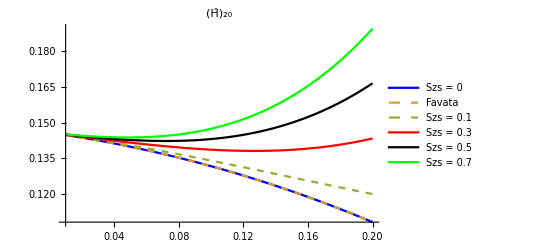

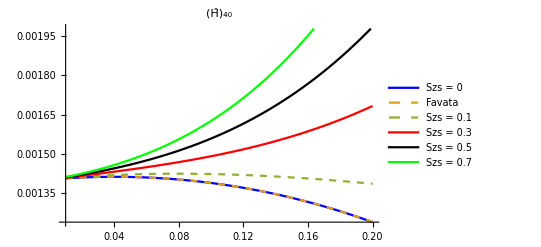

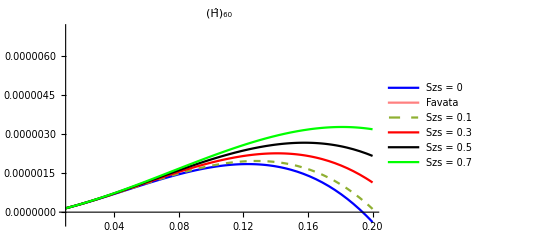

```mathematica
Plot[{Hmem20Spinz0,HmemFavta20 ,Hmem20Spinz0p1,Hmem20Spinz0p3, Hmem20Spinz0p5 , Hmem20Spinz0p7},{x, 0.01,0.2},PlotStyle-> {Blue,Dashed,Dashed,Red,Black, Green},PlotLegends->{"Szs = 0","Favata", "Szs = 0.1","Szs = 0.3","Szs = 0.5","Szs = 0.7"}, PlotLabel->"(Ĥ)_20" ]
Plot[{Hmem40Spinz0,HmemFavta40 ,Hmem40Spinz0p1,Hmem40Spinz0p3, Hmem40Spinz0p5 , Hmem40Spinz0p7},{x, 0.01,0.2},PlotStyle-> {Blue,Dashed,Dashed,Red,Black, Green},PlotLegends->{"Szs = 0","Favata", "Szs = 0.1","Szs = 0.3","Szs = 0.5","Szs = 0.7"}, PlotLabel->"(Ĥ)_40" ]
Plot[{Hmem60Spinz0,HmemFavta60 ,Hmem60Spinz0p1,Hmem60Spinz0p3, Hmem60Spinz0p5 , Hmem60Spinz0p7},{x, 0.01,0.2},PlotStyle-> {Blue,Pink,Dashed,Red,Black, Green},PlotLegends->{"Szs = 0","Favata", "Szs = 0.1","Szs = 0.3","Szs = 0.5","Szs = 0.7"}, PlotLabel->"(Ĥ)_60" ]
```

## Computing the memory contribution to the two polarizations(Comparison with results in https://arxiv.org/pdf/0812.0069.pdf)

```mathematica
(*Spin weighted spherical harmonic expression*)
dlmSum[l_, m_, s_,k_,Θ_]:= ((-1)^k (Sin[Θ/2])^(2 k + s -m) (Cos[Θ/2])^(2l + m -s - 2k))/(k! (l +m-k)! (l-s-k)! (s-m+k)!)

dlms[l_, m_, s_,Θ_]:= √((l+m)! (l-m)! (l + s)! (l-s)!)Sum[dlmSum[l, m, s,k,Θ], {k,Max[0, m-s], Min[l+m, l-s] }]

(*Expression below is for Spin weighted Spherical Subscript[harmonic, -s] Y^lm(Θ, Φ)*)
sYlm[l_, m_, s_,Θ_, Φ_]:= (-1)^s √((2l+ 1)/(4π))dlms[l, m, s,Θ]Exp[I m Φ]

(*Expression below is for nth order x coeffient in nonlinear memory expression (Equation 4.6)*)
Hpmem[xn_]:=FullSimplify[Coefficient[4 √(π/5)(sYlm[2, 0, 2,Θ, Φ]Subscript[HmemFavta, 20][x] + sYlm[4, 0, 2,Θ, Φ]Subscript[HmemFavta, 40][x] + sYlm[6, 0, 2,Θ, Φ]Subscript[HmemFavta, 60][x]+ sYlm[8, 0, 2,Θ, Φ]Subscript[HmemFavta, 80][x] + sYlm[10, 0, 2,Θ, Φ]Subscript[HmemFavta, 100][x]), x,xn] ]
(*Expression below is for nth order x coeffient and mth order η coefficient in nonlinear memory expression (Equation 4.6)*)
HpmemCoeff[xn_, ηn_] :=Expand[Coefficient[TrigExpand[Hpmem[xn]/Sin[Θ]^2]/.Sin[Θ]-> √(1-Cos[Θ]^2),η, ηn]]

Subscript[Hnp, memFavata][xorder_]:= Sin[Θ]^2(HpmemCoeff[xorder, 0] + HpmemCoeff[xorder, 1]η +HpmemCoeff[xorder, 2] η^2 + HpmemCoeff[xorder, 3] η^3 )/.δ-> √(1-η^2)

(*Expression below is for nth order x coeffient in nonlinear memory expression for Spining case*)
HpmemSpin[xn_]:=FullSimplify[Coefficient[4 √(π/5)(sYlm[2, 0, 2,Θ, Φ]Subscript[Hmem, 20][x] + sYlm[4, 0, 2,Θ, Φ]Subscript[Hmem, 40][x] + sYlm[6, 0, 2,Θ, Φ]Subscript[Hmem, 60][x]+ sYlm[8, 0, 2,Θ, Φ]Subscript[Hmem, 80][x] + sYlm[10, 0, 2,Θ, Φ]Subscript[Hmem, 100][x]), x,xn] ]
(*Expression below is for nth order x coeffient and mth order η coefficient in nonlinear memory expression ForSpining case*)
HpmemCoeffSpin[xn_, ηn_] :=Expand[Coefficient[TrigExpand[HpmemSpin[xn]/Sin[Θ]^2]/.Sin[Θ]-> √(1-Cos[Θ]^2),η, ηn]]

Subscript[Hnp, memSpin][xorder_]:= Sin[Θ]^2(HpmemCoeffSpin[xorder, 0] + HpmemCoeffSpin[xorder, 1]η +HpmemCoeffSpin[xorder, 2] η^2 + HpmemCoeffSpin[xorder, 3] η^3 )/.δ-> √(1-η^2)
```

```mathematica
HpmemFavta20= x(Subscript[Hnp, memFavata][0]+ x^(1/2)Subscript[Hnp, memFavata][1/2]+Subscript[Hnp, memFavata][1]x +x^(3/2)Subscript[Hnp, memFavata][3/2]+ Subscript[Hnp, memFavata][2] x^2 + x^(5/2)Subscript[Hnp, memFavata][5/2])/.{Subscript[χz, a]-> 0 , Subscript[χz, s]-> 0.0,η-> 0.25, γE-> 0.57721,Θ -> π/2}
Hpmem20Spinz0 =x(Subscript[Hnp, memSpin][0]+ x^(1/2)Subscript[Hnp, memSpin][1/2]+Subscript[Hnp, memSpin][1]x +x^(3/2)Subscript[Hnp, memSpin][3/2]+ Subscript[Hnp, memSpin][2] x^2 + x^(5/2)Subscript[Hnp, memSpin][5/2])/.{Subscript[χz, a]-> 0 , Subscript[χz, s]-> 0.0,η-> 0.25, γE-> 0.57721,Θ -> π/2}
Hpmem20Spinz0p1 =x(Subscript[Hnp, memSpin][0]+ x^(1/2)Subscript[Hnp, memSpin][1/2]+Subscript[Hnp, memSpin][1]x +x^(3/2)Subscript[Hnp, memSpin][3/2]+ Subscript[Hnp, memSpin][2] x^2 + x^(5/2)Subscript[Hnp, memSpin][5/2])/.{Subscript[χz, a]-> 0 , Subscript[χz, s]-> 0.1,η-> 0.25, γE-> 0.57721,Θ -> π/2}
Hpmem20Spinz0p3 =x(Subscript[Hnp, memSpin][0]+ x^(1/2)Subscript[Hnp, memSpin][1/2]+Subscript[Hnp, memSpin][1]x +x^(3/2)Subscript[Hnp, memSpin][3/2]+ Subscript[Hnp, memSpin][2] x^2 + x^(5/2)Subscript[Hnp, memSpin][5/2])/.{Subscript[χz, a]-> 0 , Subscript[χz, s]-> 0.3,η-> 0.25, γE-> 0.57721,Θ -> π/2}
Hpmem20Spinz0p5 =x(Subscript[Hnp, memSpin][0]+ x^(1/2)Subscript[Hnp, memSpin][1/2]+Subscript[Hnp, memSpin][1]x +x^(3/2)Subscript[Hnp, memSpin][3/2]+ Subscript[Hnp, memSpin][2] x^2 + x^(5/2)Subscript[Hnp, memSpin][5/2])/.{Subscript[χz, a]-> 0 , Subscript[χz, s]-> 0.5,η-> 0.25, γE-> 0.57721,Θ -> π/2}
Hpmem20Spinz0p7 =x(Subscript[Hnp, memSpin][0]+ x^(1/2)Subscript[Hnp, memSpin][1/2]+Subscript[Hnp, memSpin][1]x +x^(3/2)Subscript[Hnp, memSpin][3/2]+ Subscript[Hnp, memSpin][2] x^2 + x^(5/2)Subscript[Hnp, memSpin][5/2])/.{Subscript[χz, a]-> 0 , Subscript[χz, s]-> 0.7,η-> 0.25, γE-> 0.57721,Θ -> π/2}
Hpmem20Spinz0p9 =x(Subscript[Hnp, memSpin][0]+ x^(1/2)Subscript[Hnp, memSpin][1/2]+Subscript[Hnp, memSpin][1]x +x^(3/2)Subscript[Hnp, memSpin][3/2]+ Subscript[Hnp, memSpin][2] x^2 + x^(5/2)Subscript[Hnp, memSpin][5/2])/.{Subscript[χz, a]-> 0 , Subscript[χz, s]-> 0.99,η-> 0.25, γE-> 0.57721,Θ -> π/2}
```

x (0.177083-0.118676 x-0.515992 x^2)

x (0.177083-0.118676 x-0.515992 x^2)

x (17/96-0.118676 x+0.046875 x^(3/2)-0.518943 x^2+0.10676 x^(5/2))

x (17/96-0.118676 x+0.140625 x^(3/2)-0.542554 x^2+0.320279 x^(5/2))

x (17/96-0.118676 x+0.234375 x^(3/2)-0.589776 x^2+0.533798 x^(5/2))

x (17/96-0.118676 x+0.328125 x^(3/2)-0.66061 x^2+0.747317 x^(5/2))

x (17/96-0.118676 x+0.464063 x^(3/2)-0.805257 x^2+1.05692 x^(5/2))

```mathematica
HpmemFavta20PN0= x(Subscript[Hnp, memFavata][0])/.{Subscript[χz, a]-> 0 , Subscript[χz, s]-> 0.0,η-> 0.25, γE-> 0.57721,Θ -> π/2}
```

(17 x)/96

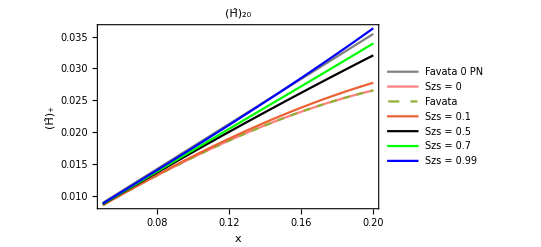

```mathematica
Plot[{HpmemFavta20PN0,Hpmem20Spinz0,HpmemFavta20 ,Hpmem20Spinz0p1, Hpmem20Spinz0p5 , Hpmem20Spinz0p7, Hpmem20Spinz0p9},{x, 0.05,0.2},Frame->True,PlotStyle-> {Gray, Pink,Dashed,Thick,Black, Green, Blue},PlotLegends->{"Favata 0 PN","Szs = 0","Favata", "Szs = 0.1","Szs = 0.5","Szs = 0.7","Szs = 0.99"}, PlotLabel->"(Ĥ)_20",FrameLabel->{"x","(Ĥ)_+"} ]
```

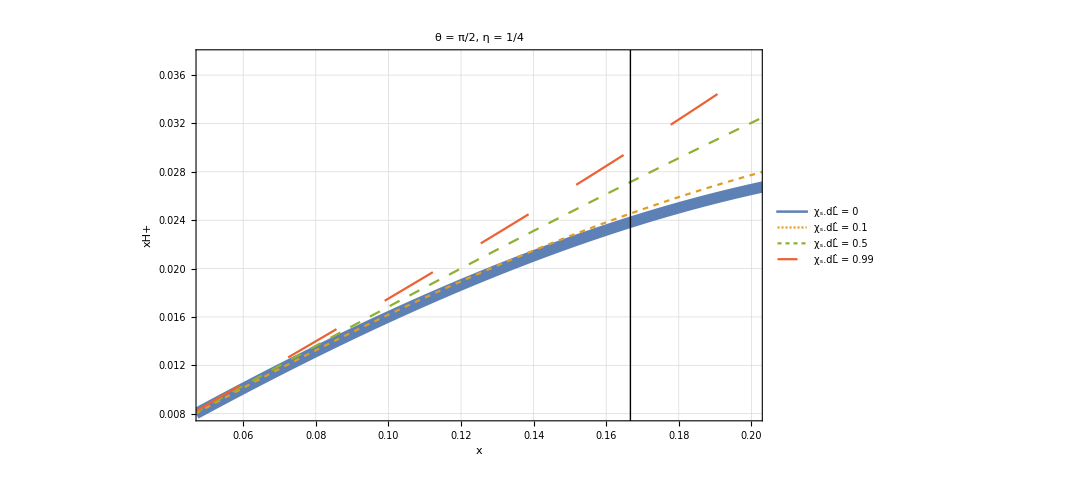

```mathematica
Plot[{Hpmem20Spinz0,Hpmem20Spinz0p1, Hpmem20Spinz0p5 ,  Hpmem20Spinz0p9},{x, 0.04,0.21},Frame->True,PlotStyle-> {Thickness[0.01],Dashing[0.005],Dashing[0.01],  Dashing[0.05]},PlotLegends->Placed[{"χ_s.dL̂ = 0", "χ_s.dL̂ = 0.1","χ_s.dL̂ = 0.5","χ_s.dL̂ = 0.99"},{0.185,0.70}],PlotLabel->"θ = π/2, η = 1/4",FrameLabel->{Style["x", 35],Style["xH+", 35]}, LabelStyle->Black,BaseStyle->{FontFamily->"TeX", FontSize->23.99},PlotRange->{{0.05, 0.20},{0.008, 0.0375}} , GridLines-> Automatic, Epilog->Line[{{1/6,-100},{1/6, 100}}]]
```

```mathematica
HpmemFavta20= x(Subscript[Hnp, memFavata][0]+ x^(1/2)Subscript[Hnp, memFavata][1/2]+Subscript[Hnp, memFavata][1]x +x^(3/2)Subscript[Hnp, memFavata][3/2]+ Subscript[Hnp, memFavata][2] x^2 + x^(5/2)Subscript[Hnp, memFavata][5/2])/.{Subscript[χz, a]-> 0 , Subscript[χz, s]-> 0.0,η-> 0.25, γE-> 0.57721,Θ -> π/2}
Hpmem20Spinz0=x(Subscript[Hnp, memSpin][0]+ x^(1/2)Subscript[Hnp, memSpin][1/2]+Subscript[Hnp, memSpin][1]x +x^(3/2)Subscript[Hnp, memSpin][3/2]+ Subscript[Hnp, memSpin][2] x^2 + x^(5/2)Subscript[Hnp, memSpin][5/2])/.{Subscript[χz, a]-> 0 , Subscript[χz, s]-> 0.0,η-> 0.25, γE-> 0.57721,Θ -> π/2}
Hpmem20Spinzm0p1 =x(Subscript[Hnp, memSpin][0]+ x^(1/2)Subscript[Hnp, memSpin][1/2]+Subscript[Hnp, memSpin][1]x +x^(3/2)Subscript[Hnp, memSpin][3/2]+ Subscript[Hnp, memSpin][2] x^2 + x^(5/2)Subscript[Hnp, memSpin][5/2])/.{Subscript[χz, a]-> 0 , Subscript[χz, s]-> -0.1,η-> 0.25, γE-> 0.57721,Θ -> π/2}
Hpmem20Spinzm0p3 =x(Subscript[Hnp, memSpin][0]+ x^(1/2)Subscript[Hnp, memSpin][1/2]+Subscript[Hnp, memSpin][1]x +x^(3/2)Subscript[Hnp, memSpin][3/2]+ Subscript[Hnp, memSpin][2] x^2 + x^(5/2)Subscript[Hnp, memSpin][5/2])/.{Subscript[χz, a]-> 0 , Subscript[χz, s]-> -0.3,η-> 0.25, γE-> 0.57721,Θ -> π/2}
Hpmem20Spinzm0p5 =x(Subscript[Hnp, memSpin][0]+ x^(1/2)Subscript[Hnp, memSpin][1/2]+Subscript[Hnp, memSpin][1]x +x^(3/2)Subscript[Hnp, memSpin][3/2]+ Subscript[Hnp, memSpin][2] x^2 + x^(5/2)Subscript[Hnp, memSpin][5/2])/.{Subscript[χz, a]-> 0 , Subscript[χz, s]-> -0.5,η-> 0.25, γE-> 0.57721,Θ -> π/2}
Hpmem20Spinzm0p7 =x(Subscript[Hnp, memSpin][0]+ x^(1/2)Subscript[Hnp, memSpin][1/2]+Subscript[Hnp, memSpin][1]x +x^(3/2)Subscript[Hnp, memSpin][3/2]+ Subscript[Hnp, memSpin][2] x^2 + x^(5/2)Subscript[Hnp, memSpin][5/2])/.{Subscript[χz, a]-> 0 , Subscript[χz, s]-> -0.7,η-> 0.25, γE-> 0.57721,Θ -> π/2}
Hpmem20Spinzm0p9 =x(Subscript[Hnp, memSpin][0]+ x^(1/2)Subscript[Hnp, memSpin][1/2]+Subscript[Hnp, memSpin][1]x +x^(3/2)Subscript[Hnp, memSpin][3/2]+ Subscript[Hnp, memSpin][2] x^2 + x^(5/2)Subscript[Hnp, memSpin][5/2])/.{Subscript[χz, a]-> 0 , Subscript[χz, s]-> -0.99,η-> 0.25, γE-> 0.57721,Θ -> π/2}
```

x (0.177083-0.118676 x-0.515992 x^2)

x (0.177083-0.118676 x-0.515992 x^2)

x (17/96-0.118676 x-0.046875 x^(3/2)-0.518943 x^2-0.10676 x^(5/2))

x (17/96-0.118676 x-0.140625 x^(3/2)-0.542554 x^2-0.320279 x^(5/2))

x (17/96-0.118676 x-0.234375 x^(3/2)-0.589776 x^2-0.533798 x^(5/2))

x (17/96-0.118676 x-0.328125 x^(3/2)-0.66061 x^2-0.747317 x^(5/2))

x (17/96-0.118676 x-0.464063 x^(3/2)-0.805257 x^2-1.05692 x^(5/2))

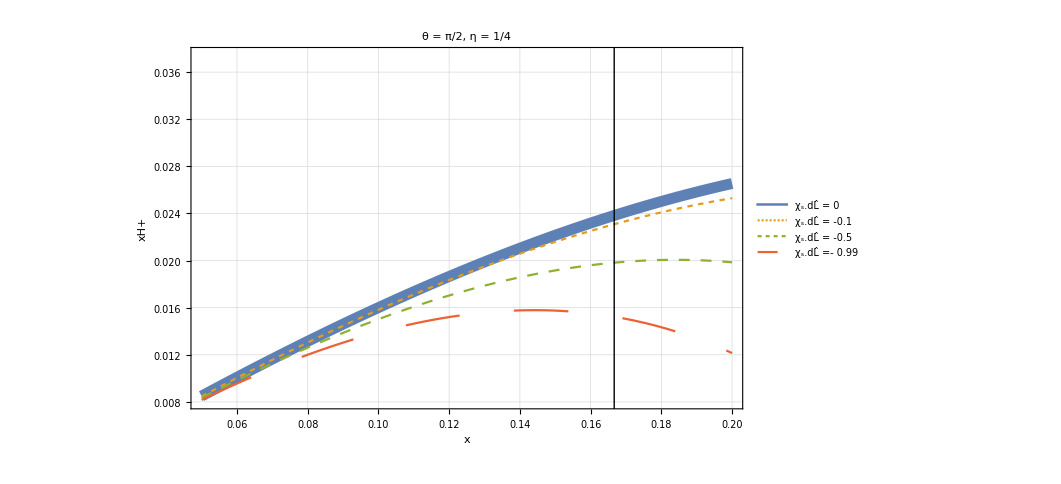

```mathematica
Plot[{Hpmem20Spinz0,Hpmem20Spinzm0p1, Hpmem20Spinzm0p5 ,  Hpmem20Spinzm0p9},{x, 0.05,0.2},Frame->True,PlotStyle-> { Thickness[0.01],Dashing[0.005],Dashing[0.01],  Dashing[0.05]},PlotLegends->Placed[{"χ_s.dL̂ = 0", "χ_s.dL̂ = -0.1","χ_s.dL̂ = -0.5","χ_s.dL̂ =- 0.99"},{0.185,0.70}],PlotLabel->"θ = π/2, η = 1/4",FrameLabel->{Style["x", 35],Style["xH+", 35]}, LabelStyle->Black,BaseStyle->{FontFamily->"TeX", FontSize->23.99}  ,PlotRange->{{0.05, 0.20},{0.008, 0.0375}}, GridLines-> Automatic, Epilog->Line[{{1/6,-100},{1/6, 100}}]]
```

```mathematica
HpmemFavta0PN= x(Subscript[Hnp, memFavata][0])/.{Subscript[χz, a]-> 0 , Subscript[χz, s]-> 0.0,η-> 0.25, γE-> 0.57721,Θ -> π/2}
HpmemFavta1PN= x(Subscript[Hnp, memFavata][0]+ x^(1/2)Subscript[Hnp, memFavata][1/2]+Subscript[Hnp, memFavata][1]x )/.{Subscript[χz, a]-> 0 , Subscript[χz, s]-> 0.0,η-> 0.25, γE-> 0.57721,Θ -> π/2}
HpmemFavta2PN= x(Subscript[Hnp, memFavata][0]+ x^(1/2)Subscript[Hnp, memFavata][1/2]+Subscript[Hnp, memFavata][1]x +x^(3/2)Subscript[Hnp, memFavata][3/2]+ Subscript[Hnp, memFavata][2] x^2 )/.{Subscript[χz, a]-> 0 , Subscript[χz, s]-> 0.0,η-> 0.25, γE-> 0.57721,Θ -> π/2}
HpmemFavta2p5PN= x(Subscript[Hnp, memFavata][0]+ x^(1/2)Subscript[Hnp, memFavata][1/2]+Subscript[Hnp, memFavata][1]x +x^(3/2)Subscript[Hnp, memFavata][3/2]+ Subscript[Hnp, memFavata][2] x^2 + x^(5/2)Subscript[Hnp, memFavata][5/2])/.{Subscript[χz, a]-> 0 , Subscript[χz, s]-> 0.0,η-> 0.25, γE-> 0.57721,Θ -> π/2}
```

(17 x)/96

(17/96-0.118676 x) x

x (17/96-0.118676 x-0.515992 x^2)

x (0.177083-0.118676 x-0.515992 x^2)

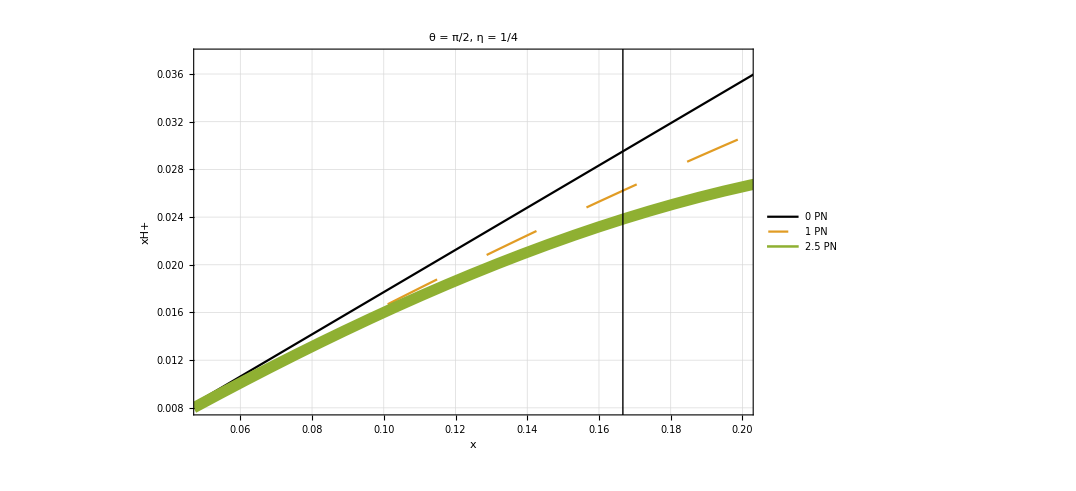

```mathematica
Plot[{HpmemFavta0PN,HpmemFavta1PN,  HpmemFavta2p5PN},{x, 0.005,0.35},Frame->True,PlotStyle-> { Black,Dashing[0.05],  Thickness[0.01]},PlotLegends->Placed[{"0 PN", "1 PN","2.5 PN"},{0.185,0.70}],PlotLabel->"θ = π/2, η = 1/4",FrameLabel->{Style["x", 35],Style["xH+", 35]}, LabelStyle->Black,BaseStyle->{FontFamily->"TeX", FontSize->23.99}  ,PlotRange->{{0.05, 0.2},{0.008, 0.0375}}, GridLines-> Automatic, Epilog->Line[{{1/6,-100},{1/6, 100}}]]
```

```mathematica
HpmemFavta20Theta= (Subscript[Hnp, memFavata][0]+ x^(1/2)Subscript[Hnp, memFavata][1/2]+Subscript[Hnp, memFavata][1]x +x^(3/2)Subscript[Hnp, memFavata][3/2]+ Subscript[Hnp, memFavata][2] x^2 + x^(5/2)Subscript[Hnp, memFavata][5/2])/.{Subscript[χz, a]-> 0 , Subscript[χz, s]-> 0.0,η-> 0.25, γE-> 0.57721,x -> 1/5};
Hpmem20Spinz0Theta =(Subscript[Hnp, memSpin][0]+ x^(1/2)Subscript[Hnp, memSpin][1/2]+Subscript[Hnp, memSpin][1]x +x^(3/2)Subscript[Hnp, memSpin][3/2]+ Subscript[Hnp, memSpin][2] x^2 + x^(5/2)Subscript[Hnp, memSpin][5/2])/.{Subscript[χz, a]-> 0 , Subscript[χz, s]-> 0.0,η-> 0.25, γE-> 0.57721,x -> 1/5};
Hpmem20Spinz0p1Theta =(Subscript[Hnp, memSpin][0]+ x^(1/2)Subscript[Hnp, memSpin][1/2]+Subscript[Hnp, memSpin][1]x +x^(3/2)Subscript[Hnp, memSpin][3/2]+ Subscript[Hnp, memSpin][2] x^2 + x^(5/2)Subscript[Hnp, memSpin][5/2])/.{Subscript[χz, a]-> 0 , Subscript[χz, s]-> 0.1,η-> 0.25, γE-> 0.57721,x -> 1/5};
Hpmem20Spinz0p3Theta =(Subscript[Hnp, memSpin][0]+ x^(1/2)Subscript[Hnp, memSpin][1/2]+Subscript[Hnp, memSpin][1]x +x^(3/2)Subscript[Hnp, memSpin][3/2]+ Subscript[Hnp, memSpin][2] x^2 + x^(5/2)Subscript[Hnp, memSpin][5/2])/.{Subscript[χz, a]-> 0 , Subscript[χz, s]-> 0.3,η-> 0.25, γE-> 0.57721,x -> 1/5};
Hpmem20Spinz0p5Theta =(Subscript[Hnp, memSpin][0]+ x^(1/2)Subscript[Hnp, memSpin][1/2]+Subscript[Hnp, memSpin][1]x +x^(3/2)Subscript[Hnp, memSpin][3/2]+ Subscript[Hnp, memSpin][2] x^2 + x^(5/2)Subscript[Hnp, memSpin][5/2])/.{Subscript[χz, a]-> 0 , Subscript[χz, s]-> 0.5,η-> 0.25, γE-> 0.57721,x -> 1/5};
Hpmem20Spinz0p7Theta =(Subscript[Hnp, memSpin][0]+ x^(1/2)Subscript[Hnp, memSpin][1/2]+Subscript[Hnp, memSpin][1]x +x^(3/2)Subscript[Hnp, memSpin][3/2]+ Subscript[Hnp, memSpin][2] x^2 + x^(5/2)Subscript[Hnp, memSpin][5/2])/.{Subscript[χz, a]-> 0 , Subscript[χz, s]-> 0.7,η-> 0.25, γE-> 0.57721,x -> 1/5};
Hpmem20Spinz0p9Theta =(Subscript[Hnp, memSpin][0]+ x^(1/2)Subscript[Hnp, memSpin][1/2]+Subscript[Hnp, memSpin][1]x +x^(3/2)Subscript[Hnp, memSpin][3/2]+ Subscript[Hnp, memSpin][2] x^2 + x^(5/2)Subscript[Hnp, memSpin][5/2])/.{Subscript[χz, a]-> 0 , Subscript[χz, s]-> 0.99,η-> 0.25, γE-> 0.57721,x -> 1/5};
```

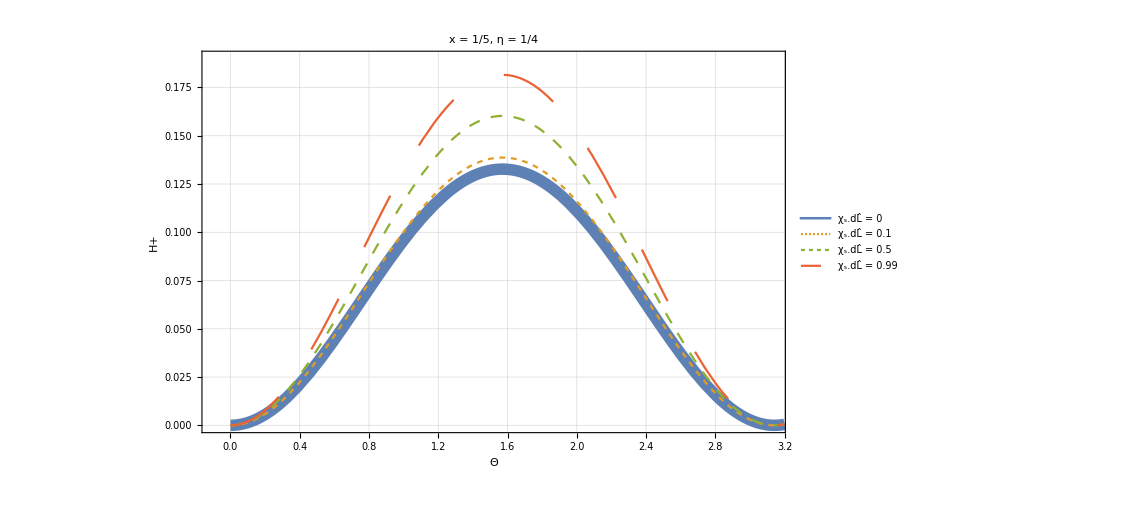

```mathematica
Plot[{Hpmem20Spinz0Theta,Hpmem20Spinz0p1Theta, Hpmem20Spinz0p5Theta ,  Hpmem20Spinz0p9Theta},{Θ, 0.0,3.2},Frame->True,PlotStyle-> { Thickness[0.01],Dashing[0.005],Dashing[0.01],  Dashing[0.05]},PlotLegends->Placed[{"χ_s.dL̂ = 0", "χ_s.dL̂ = 0.1","χ_s.dL̂ = 0.5","χ_s.dL̂ = 0.99"},{0.120,0.70}],PlotLabel->"x = 1/5, η = 1/4",FrameLabel->{Style["Θ", 35],Style["H+", 35]}, LabelStyle->Black , BaseStyle->{FontFamily->"TeX", FontSize->23.5}  ,PlotRange->{{-0.10, 3.14},{0.00, 0.19}}, GridLines-> Automatic]
```

```mathematica
HpmemFavta20Theta= (Subscript[Hnp, memFavata][0]+ x^(1/2)Subscript[Hnp, memFavata][1/2]+Subscript[Hnp, memFavata][1]x +x^(3/2)Subscript[Hnp, memFavata][3/2]+ Subscript[Hnp, memFavata][2] x^2 + x^(5/2)Subscript[Hnp, memFavata][5/2])/.{Subscript[χz, a]-> 0 , Subscript[χz, s]-> 0.0,η-> 0.25, γE-> 0.57721,x -> 1/5};
Hpmem20Spinz0Theta =(Subscript[Hnp, memSpin][0]+ x^(1/2)Subscript[Hnp, memSpin][1/2]+Subscript[Hnp, memSpin][1]x +x^(3/2)Subscript[Hnp, memSpin][3/2]+ Subscript[Hnp, memSpin][2] x^2 + x^(5/2)Subscript[Hnp, memSpin][5/2])/.{Subscript[χz, a]-> 0 , Subscript[χz, s]-> 0.0,η-> 0.25, γE-> 0.57721,x -> 1/5};
Hpmem20Spinzm0p1Theta =(Subscript[Hnp, memSpin][0]+ x^(1/2)Subscript[Hnp, memSpin][1/2]+Subscript[Hnp, memSpin][1]x +x^(3/2)Subscript[Hnp, memSpin][3/2]+ Subscript[Hnp, memSpin][2] x^2 + x^(5/2)Subscript[Hnp, memSpin][5/2])/.{Subscript[χz, a]-> 0 , Subscript[χz, s]->- 0.1,η-> 0.25, γE-> 0.57721,x -> 1/5};
Hpmem20Spinzm0p3Theta =(Subscript[Hnp, memSpin][0]+ x^(1/2)Subscript[Hnp, memSpin][1/2]+Subscript[Hnp, memSpin][1]x +x^(3/2)Subscript[Hnp, memSpin][3/2]+ Subscript[Hnp, memSpin][2] x^2 + x^(5/2)Subscript[Hnp, memSpin][5/2])/.{Subscript[χz, a]-> 0 , Subscript[χz, s]-> -0.3,η-> 0.25, γE-> 0.57721,x -> 1/5};
Hpmem20Spinzm0p5Theta =(Subscript[Hnp, memSpin][0]+ x^(1/2)Subscript[Hnp, memSpin][1/2]+Subscript[Hnp, memSpin][1]x +x^(3/2)Subscript[Hnp, memSpin][3/2]+ Subscript[Hnp, memSpin][2] x^2 + x^(5/2)Subscript[Hnp, memSpin][5/2])/.{Subscript[χz, a]-> 0 , Subscript[χz, s]-> -0.5,η-> 0.25, γE-> 0.57721,x -> 1/5};
Hpmem20Spinzm0p7Theta =(Subscript[Hnp, memSpin][0]+ x^(1/2)Subscript[Hnp, memSpin][1/2]+Subscript[Hnp, memSpin][1]x +x^(3/2)Subscript[Hnp, memSpin][3/2]+ Subscript[Hnp, memSpin][2] x^2 + x^(5/2)Subscript[Hnp, memSpin][5/2])/.{Subscript[χz, a]-> 0 , Subscript[χz, s]-> -0.7,η-> 0.25, γE-> 0.57721,x -> 1/5};
Hpmem20Spinzm0p9Theta =(Subscript[Hnp, memSpin][0]+ x^(1/2)Subscript[Hnp, memSpin][1/2]+Subscript[Hnp, memSpin][1]x +x^(3/2)Subscript[Hnp, memSpin][3/2]+ Subscript[Hnp, memSpin][2] x^2 + x^(5/2)Subscript[Hnp, memSpin][5/2])/.{Subscript[χz, a]-> 0 , Subscript[χz, s]-> -0.99,η-> 0.25, γE-> 0.57721,x -> 1/5};
```

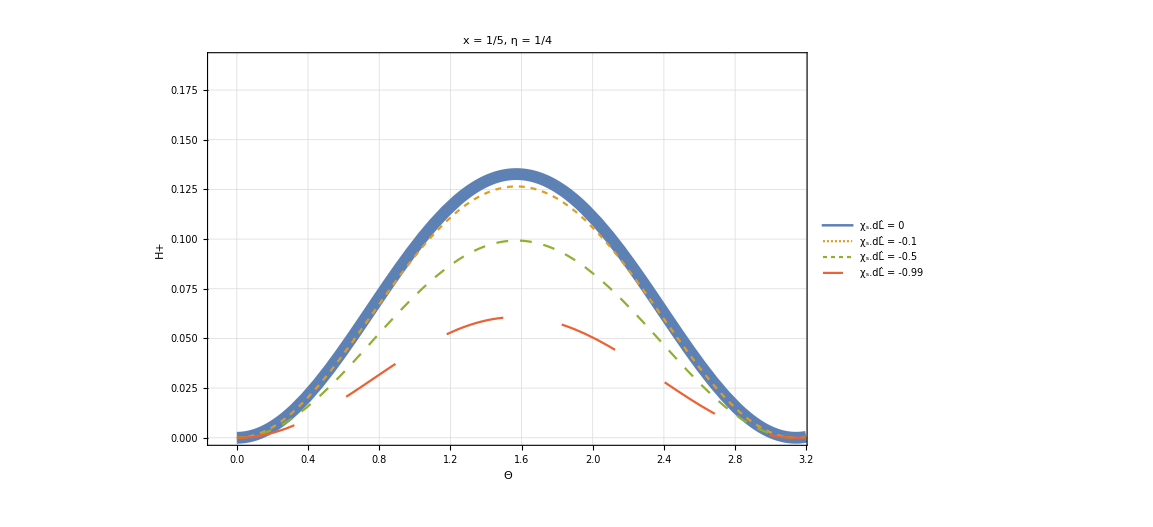

```mathematica
Plot[{Hpmem20Spinz0Theta,Hpmem20Spinzm0p1Theta, Hpmem20Spinzm0p5Theta ,  Hpmem20Spinzm0p9Theta},{Θ, 0.0,3.2},Frame->True,PlotStyle-> { Thickness[0.01],Dashing[0.005],Dashing[0.01],  Dashing[0.05]},PlotLegends->Placed[{"χ_s.dL̂ = 0", "χ_s.dL̂ = -0.1","χ_s.dL̂ = -0.5","χ_s.dL̂ = -0.99"},{0.120,0.77}],PlotLabel->"x = 1/5, η = 1/4",FrameLabel->{Style["Θ", 35],Style["H+", 35]}, LabelStyle->Black , BaseStyle->{FontFamily->"TeX", FontSize->23.5},PlotRange->{{-0.10, 3.14},{0.00, 0.19}} , GridLines-> Automatic]
```

```mathematica
(*Subscript[Hnp, memSpin][0];
Subscript[Hnp, memSpin][1];
Collect[Subscript[Hnp, memSpin][3/2],{Sin[Θ]^2,Subscript[χz, a],Subscript[χz, s],η}];
Collect[Subscript[Hnp, memSpin][2],{Sin[Θ]^2,Subscript[χz, a],Subscript[χz, s],η}];
Collect[Subscript[Hnp, memSpin][5/2],{Sin[Θ]^2,Subscript[χz, a],Subscript[χz, s],η}];
Collect[Subscript[Hnp, memSpin][3],{Sin[Θ]^2,Subscript[χz, a],Subscript[χz, s],η}];*)
```

```mathematica
xdot= 1/(5 M)64 x^5 η (1+x (-743/336-(11 η)/4)+x^(3/2) (4 π-(113 δ Subscript[χz, a])/12+(-113/12+(19 η)/3) Subscript[χz, s])+x^(5/2) (-(4159 π)/672-(189 π η)/8+δ (-31319/1008+(1159 η)/24) Subscript[χz, a]+(-31319/1008+(22975 η)/252-(79 η^2)/3) Subscript[χz, s])+x^2 (34103/18144+(13661 η)/2016+(59 η^2)/18+(719/96-30 η) Subscript[χz, a]^2+(-233/96+10 η) Subscript[χz, a]^2+81/8 δ Subscript[χz, a] Subscript[χz, s]+(-233/96-(7 η)/24) Subscript[χz, s]^2+(719/96+η/24) Subscript[χz, s]^2)+x^3 (16447322263/139708800+(16 π^2)/3-(1712 γE)/105+(-56198689/217728+(451 π^2)/48) η+(541 η^2)/896-(5605 η^3)/2592-856/105 Log[16 x]-80/3 π δ Subscript[χz, a]+(-145/448+(21985 η)/4032-(89 η^2)/6) Subscript[χz, a]^2+(575/448+(565 δ^2)/9-(65815 η)/4032+(89 η^2)/2) Subscript[χz, a]^2+δ (-145/224+(2143 η)/288) Subscript[χz, a] Subscript[χz, s]+(-(80 π)/3+(40 π η)/3+δ (258295/2016-(9203 η)/96) Subscript[χz, a]) Subscript[χz, s]+(-145/448+(1891 η)/576-(7 η^2)/144) Subscript[χz, s]^2+(258295/4032-(48773 η)/576+(3041 η^2)/144) Subscript[χz, s]^2))/.{M -> 1, Subscript[χz, a]-> 0 , η-> 0.25, γE-> 0.57721 };
```

```mathematica
xdots0 =xdot/.{Subscript[χz, s]-> 0.0,x-> ys0[t]};
xdots0p8 =xdot/.{Subscript[χz, s]-> 0.8,x-> ys0p8[t]};
xdotsm0p8 =xdot/.{Subscript[χz, s]-> -0.8,x-> ysm0p8[t]};
```

```mathematica
s0=NDSolve[{ys0'[t]==xdots0, ys0[0]==1},ys0, {t, -13000,0}]
s0p8=NDSolve[{ys0p8'[t]==xdots0p8 , ys0p8[0]==1},ys0p8, {t, -13000,0}]
sm0p8=NDSolve[{ysm0p8'[t]==xdotsm0p8, ysm0p8[0]==1},ysm0p8, {t, -13000,0}]
```

{{ys0→InterpolatingFunction[…]}}

{{ys0p8→InterpolatingFunction[…]}}

{{ysm0p8→InterpolatingFunction[…]}}

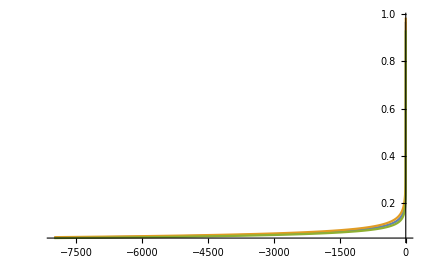

```mathematica
Plot[{Evaluate[ys0[t]/.s0],Evaluate[ys0p8[t]/.s0p8],Evaluate[ysm0p8[t]/.sm0p8]}, {t, -8000,0}, PlotRange->All]
```

```mathematica
Hpmem20Spinzm0p8 =x(Subscript[Hnp, memSpin][0]+ x^(1/2)Subscript[Hnp, memSpin][1/2]+Subscript[Hnp, memSpin][1]x +x^(3/2)Subscript[Hnp, memSpin][3/2]+ Subscript[Hnp, memSpin][2] x^2 + x^(5/2)Subscript[Hnp, memSpin][5/2])/.{Subscript[χz, a]-> 0 , Subscript[χz, s]-> -0.8,η-> 0.25, γE-> 0.57721,Θ -> π/2};
Hpmem20Spinz0p8 =x(Subscript[Hnp, memSpin][0]+ x^(1/2)Subscript[Hnp, memSpin][1/2]+Subscript[Hnp, memSpin][1]x +x^(3/2)Subscript[Hnp, memSpin][3/2]+ Subscript[Hnp, memSpin][2] x^2 + x^(5/2)Subscript[Hnp, memSpin][5/2])/.{Subscript[χz, a]-> 0 , Subscript[χz, s]-> 0.8,η-> 0.25, γE-> 0.57721,Θ -> π/2};
```

```mathematica
FtSpinz0[t_] := (HpmemFavta20/2)/.x-> ys0[t]/.s0
FtSpinz0p8[t_] := (Hpmem20Spinz0p8/2)/.x-> ys0p8[t]/.s0p8
FtSpinzm0p8[t_] := (Hpmem20Spinzm0p8/2)/.x-> ysm0p8[t]/.sm0p8
```

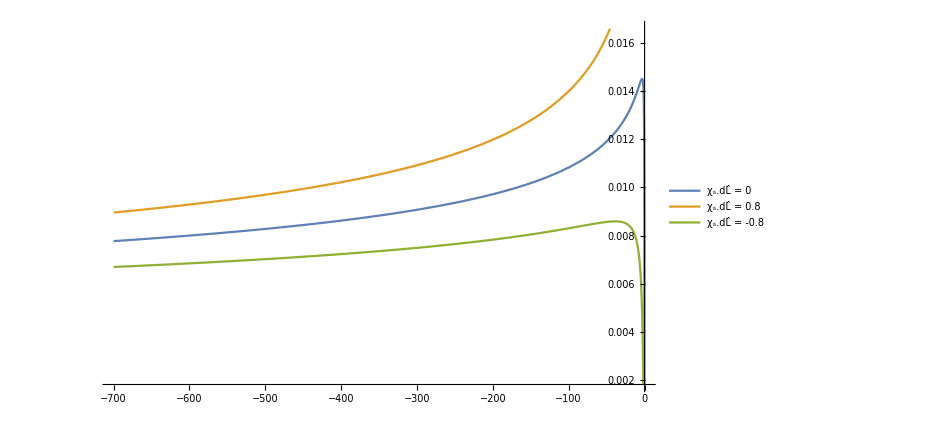

```mathematica
Plot[{FtSpinz0[t], FtSpinz0p8[t], FtSpinzm0p8[t]}, {t, -700,0},PlotLegends->Placed[{"χ_s.dL̂ = 0", "χ_s.dL̂ = 0.8","χ_s.dL̂ = -0.8"},{0.120,0.77}]]
```

```mathematica
NRdataSm0p8 = Import["/home/aschoudhary/data/SXSdata/Spinning_binary_with_SpinAntialigned_27Dec/Memory_data/rMPsi4_Sz1_m0p80_Sz2_m0p80_q1p5dataN4Clean_hMemNR.dat"];
```

```mathematica
NRdataS0p8 = Import["/home/aschoudhary/data/SXSdata/Spinning_binary_with_SpinAligned_27Dec/Memory_data/rMPsi4_Sz1_0p80_Sz2_0p80_q1p5dataN4Clean_hMemNR.dat"];
```

```mathematica
hmemNRSm0p8 = Transpose[{NRdataSm0p8[[All,1]],(17 NRdataSm0p8[[All,2]]+FtSpinzm0p8[NRdataSm0p8[[All,1]][[1]]][[1]])}];
hmemNRS0p8 = Transpose[{NRdataS0p8[[All,1]],(17 NRdataS0p8[[All,2]]+FtSpinz0p8[NRdataS0p8[[All,1]][[1]]][[1]])}];
```

```mathematica
dataFtSpinzm0p8=Transpose[{NRdataSm0p8[[All,1]], FtSpinzm0p8[NRdataSm0p8[[All,1]]][[1]]}];
dataFtSpinz0p8=Transpose[{NRdataS0p8[[All,1]], FtSpinz0p8[NRdataS0p8[[All,1]]][[1]]}];
```

InterpolatingFunction::dmval: Input value {0.627647} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.22765} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.82765} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {0.0903078} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.447308} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.804308} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
ListPlot[{hmemNRSm0p8, dataFtSpinzm0p8, hmemNRS0p8, dataFtSpinz0p8},PlotRange->{{-1000.05,50.0},{0.003, 0.063}}, PlotLegends->Placed[{"χ_s.dL̂ = -0.8 NR", "χ_s.dL̂ = -0.8 PN","χ_s.dL̂ = 0.8 NR","χ_s.dL̂ = 0.8 PN"},{0.120,0.77}], PlotStyle->PointSize[Medium]]
```

-Graphics-

```mathematica
ListPlot[{hmemNRSm0p8, dataFtSpinzm0p8, hmemNRS0p8, dataFtSpinz0p8}, PlotLegends->Placed[{"χ_s.dL̂ = -0.8 NR", "χ_s.dL̂ = -0.8 PN","χ_s.dL̂ = 0.8 NR","χ_s.dL̂ = 0.8 PN"},{0.120,0.77}], PlotStyle->PointSize[Medium],PlotRange->Automatic]
```

-Graphics-

## Memory from BOB model

```mathematica
(*Computing the final spin of the blackholes*)
```

```mathematica
p0 = 0.04826; p1=0.01559; p2 = 0.00485; s4 = -0.1229; s5 = 0.4537; t0 = -2.8904; t2 = -3.5171; t3 = 2.5763; q=1; eta = 1/4; theta = π/2; 
pct= 0.99; tcut = 200; tmin = -20; tmax = 50;
```

```mathematica
Mf[α1_, α2_]:= 1- p0 - p1 (α1+ α2) - p2(α1+ α2)^2
αb[α1_, α2_]:= (q^2 α1+ α2)/(q^2+1)
```

```mathematica
Alpha[α1_, α2_]:= αb[α1, α2] + s4 eta  αb[α1, α2]^2 + s5 eta^2 αb[α1, α2]  + t0 eta αb[α1, α2]  + 2 √3 eta +  t2 eta^2 + t3 eta^3
```

```mathematica
(*ISCO calcualtion*)
```

```mathematica
Z1[af_]:= 1 + (1-af^2)^(1/3)((1+af)^(1/3) + (1-af)^(1/3))
Z2[af_, Z1_]:= √(3 af^2 + Z1^2)
RISCO[Z1_, Z2_]:= 3 + Z2 - √((3-Z1)(3+ Z1 + 2 Z2))
OMISCO[RISCO_, af_]:= 1/(RISCO^(3/2)+ af )
OMQNM[α1_, α2_]:= (1- 0.63 (1-αb[α1, α2])^0.3)/(2Mf[α1, α2])
```

```mathematica
(*BOB memory calculation*)
```

```mathematica
Y20[θ_]:=1/4 √(15/(2 π))Sin[θ]^2
Q[af_] := 2 (1-af)^-0.45
```

```mathematica
TAO[α1_, α2_]:= 2 Q[αb[α1, α2]]Mf[α1, α2]/(1- 0.63 (1-αb[α1, α2])^0.3)
```

```mathematica
Ap[α1_, α2_] := 1.068(1-Mf[α1, α2])^0.8918
OMREF[α1_, α2_]:= OMISCO[RISCO[Z1[αb[α1, α2]], Z2[αb[α1, α2], Z1[αb[α1, α2]]]], αb[α1, α2]]
```

```mathematica
OMP[α1_, α2_]:= ((OMQNM[α1, α2]^4 + OMREF[α1, α2]^4)/2)^(1/4)
OMM[α1_, α2_]:= ((OMQNM[α1, α2]^4 - OMREF[α1, α2]^4)/2)^(1/4)
```

```mathematica
(*Slight consusion over sign*)
KAPPAM[α1_, α2_]:= ((OMP[α1, α2]^4 + OMM[α1, α2]^4))^(1/4)
KAPPAP[α1_, α2_]:= ((OMP[α1, α2]^4 - OMM[α1, α2]^4))^(1/4)
(*BOB Memory*)
OM[t_, α1_, α2_]:= (OMP[α1, α2]^4 + OMM[α1, α2]^4 Tanh[t/TAO[α1, α2]])^(1/4)
```

```mathematica
MEMBOB[t_, α1_, α2_]:= (Sin[theta]^2)(17 + (Cos[theta])^2)Ap[α1, α2]^2 TAO[α1, α2]OM[t, α1, α2]^2/OMM[α1, α2]^4
```

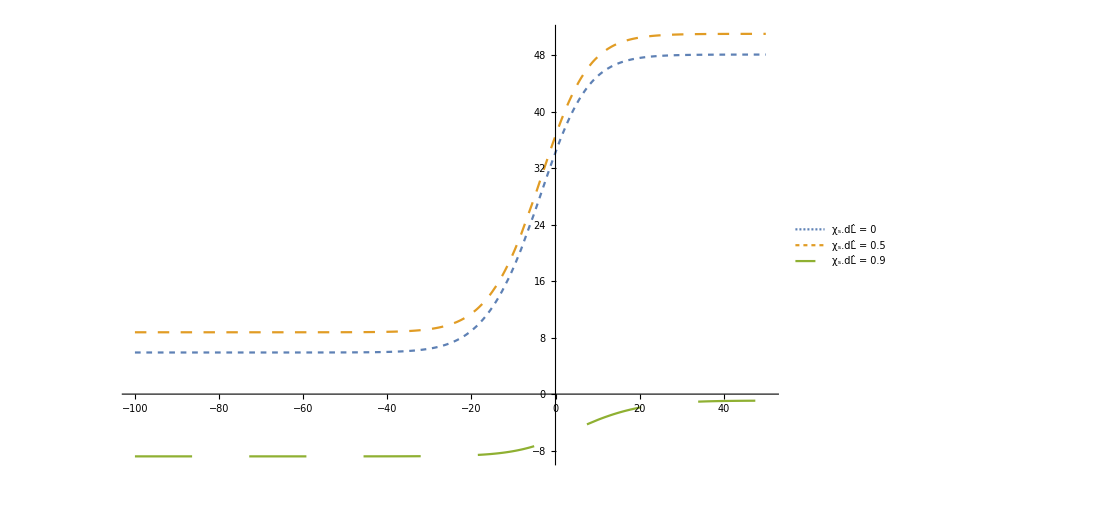

```mathematica
Plot[{MEMBOB[t, 0, 0], MEMBOB[t, 0.5, 0.5], MEMBOB[t, -0.9, -0.9]}, {t, -100, 50}, PlotStyle-> {Dashing[0.005],Dashing[0.01],  Dashing[0.05]},PlotLegends->Placed[{"χ_s.dL̂ = 0", "χ_s.dL̂ = 0.5","χ_s.dL̂ = 0.9"},{0.120,0.77}]]
```

```mathematica
BOBmemScale[scale_]:= Plot[MEMBOB[t, scale, scale]-MEMBOB[-100, scale, scale], {t, -100, 50}, PlotRange->{{-100, 50},{-10.0, 45.0}}]
```

```mathematica
Manipulate[BOBmemScale[n], {n, -0.9, 0.9}]
```